```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
CCompilers[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
Get["MergerTransport/Merger2DProton.m"]
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(binTable[[i,1,1]]+binTable[[i,1,2]])/2,(binTable[[i,2,1]]+binTable[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
bin2DGen2[xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY},binLengthX=Round[(xEnd-xStart)/binNoX,1/10^6.];binLengthY=Round[(yEnd-yStart)/binNoY,1/10^6.];binsX=Table[{xStart+(i-1) binLengthX,xStart+i binLengthX},{i,binNoX}];binsY=Table[{yStart+(i-1) binLengthY,yStart+i binLengthY},{i,binNoY}];binList=Flatten[Table[{binsX⟦i⟧,binsY⟦j⟧},{i,Length[binsX]},{j,Length[binsY]}],1];Return[binList];]
```

## 0 spectrum

### algorithm to sort files according to last binnumber

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_179-264.txt}

```mathematica
RefSpectrum=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(binTable[[i,1,1]]+binTable[[i,1,2]])/2,(binTable[[i,2,1]]+binTable[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

### show single core timing

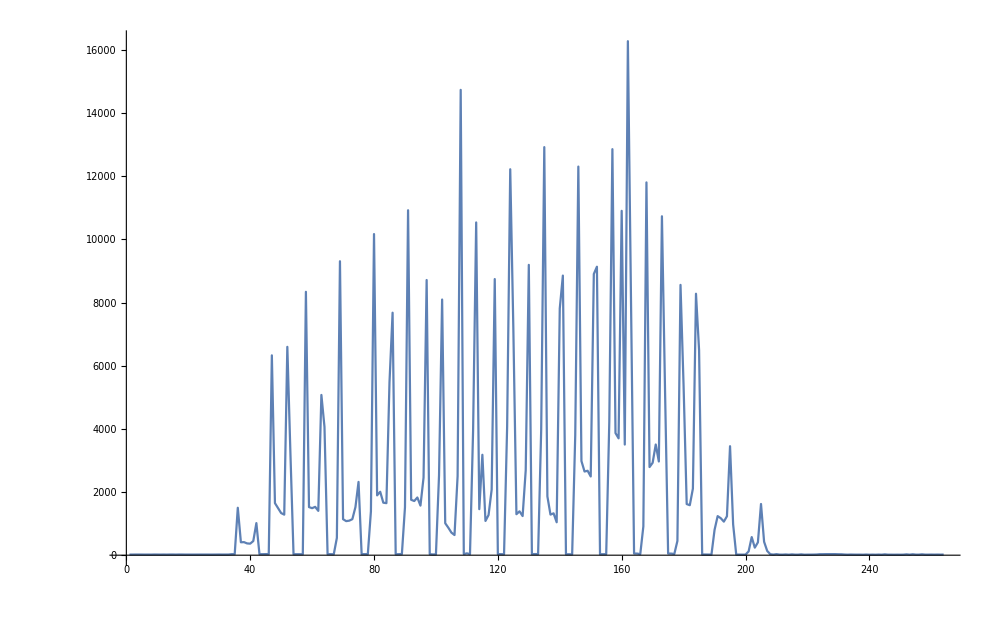

```mathematica
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000]
```

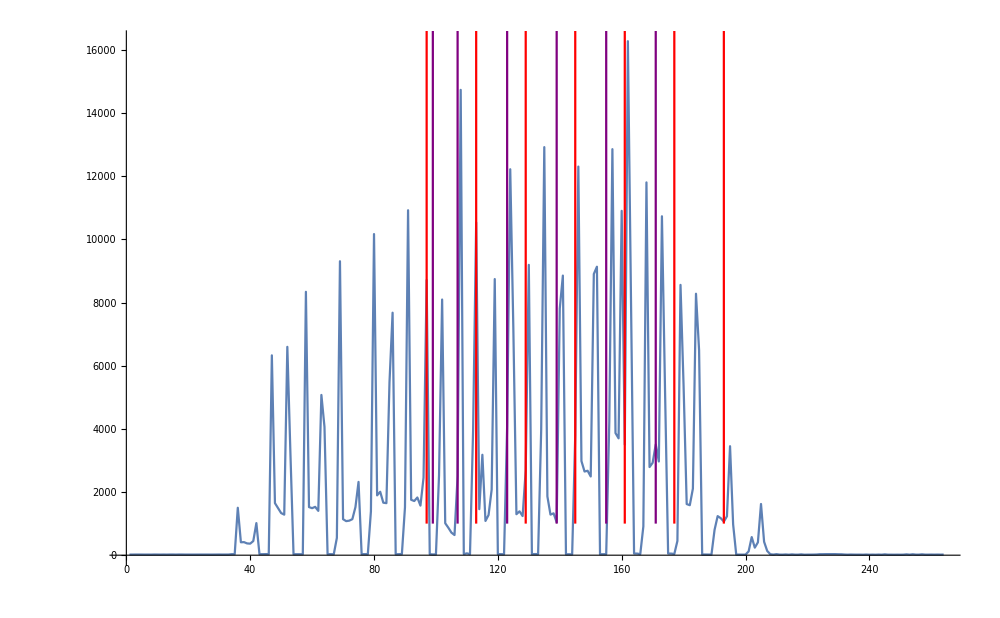

```mathematica
Show[
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000],
ParametricPlot[{{97,1000*d},{113,1000*d},{129,1000*d},{145,1000*d},{161,1000*d},{177,1000*d},{193,1000*d}},{d,1,253},PlotStyle->Red],
ParametricPlot[{{99,1000*d},{107,1000*d},{123,1000*d},{139,1000*d},{155,1000*d},{171,1000*d}},{d,1,253},PlotStyle->Purple]
]
```

## get Bin data

```mathematica
(xStart-xEnd)/24
```

-0.001875

```mathematica
158/220.
```

0.718182

```mathematica
158+62
```

220

```mathematica
xyBins[[1]]
```

{{0.025,0.02625},{-0.02,-0.015909}}

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto={{-0.06999999999999999,-0.06499999999999999,-0.05999999999999999,-0.05499999999999999,-0.04999999999999999,-0.04499999999999999,-0.039999999999999994,-0.03499999999999999,-0.029999999999999992,-0.024999999999999994,-0.01999999999999999,-0.014999999999999993,-0.009999999999999995,-0.0049999999999999906,1.3877787807814457*^-17,0.0050000000000000044,0.010000000000000009,0.015000000000000013,0.020000000000000004,0.02500000000000001,0.030000000000000013,0.035,0.04000000000000001,0.045},{-1.0540019999999999,-1.049002,-1.0440019999999999,-1.039002,-1.0340019999999999,-1.029002,-1.0240019999999999,-1.019002,-1.0140019999999998,-1.009002,-1.0040019999999998,-0.9990019999999998,-0.9940019999999998,-0.9890019999999999,-0.9840019999999998,-0.9790019999999999,-0.9740019999999999,-0.9690019999999999,-0.9640019999999999,-0.9590019999999999,-0.9540019999999999,-0.9490019999999999,-0.9440019999999999},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=0.757116
```

0.757116

```mathematica
xyBins[[1,1]]
```

{0.025,0.02625}

```mathematica
Clear[BinCenters]
```

### Get XY Bins with Ybins halfed

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
xStart=-0.06999999999999999;
xEnd=0.045;
yStart=1.0540019999999999-R;
yEnd=0.9440019999999999-R;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
XYBinBoundariesYHalf[[1]]
```

{{-0.07,-0.065},{0.286884,0.296884}}

```mathematica
XYBinCentersYHalf[[1]]
```

{0.0209375,-0.026818}

## check spectrum

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

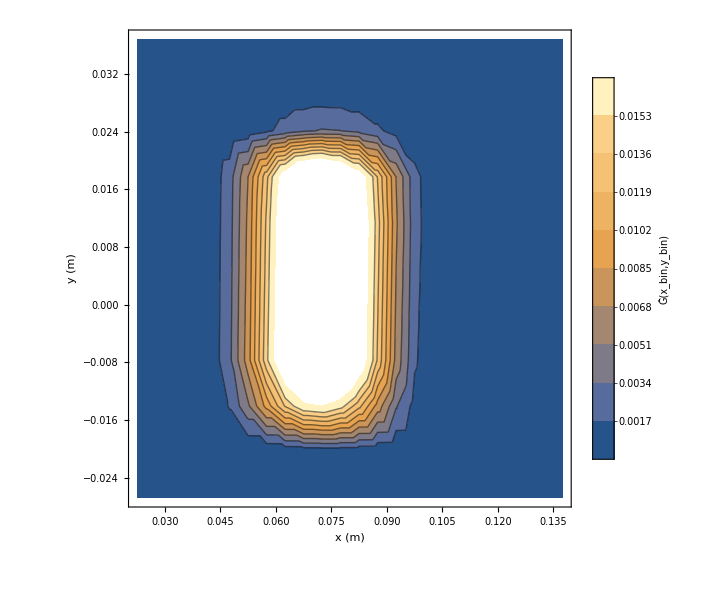

```mathematica
TransferContourPlot=ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/Transfer3D.png",Transfer3DPlot,ImageResolution->450];
Export["~/Dropbox/PhD/PhDLatex/Figures/TransferContour.png",TransferContourPlot,ImageResolution->450];*)
```

```mathematica
0.01*0.035
```

0.00035

```mathematica
0.02*0.05
```

0.001

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a1050/"];
```

```mathematica
d0SubFileNamesa1050P=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_da0_a1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_da0_a1050_179-264.txt}

```mathematica
d0Spectruma1050P=Flatten[Table[Import[d0SubFileNamesa1050P[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050P]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050P[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d1050PSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050P[[All,2]]/Total[d0Spectruma1050P[[All,2]]]}]];
```

# dalpha, k=97.07

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1050/"];
```

```mathematica
dAlphaSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dAlpha_a-1050_179-264.txt}

```mathematica
dAlphaSpectruma0=Flatten[Table[Import[dAlphaSubFileNamesa0[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1040/"];
```

```mathematica
dAlphaSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1040_179-264.txt}

```mathematica
dAlphaSpectruma1040=Flatten[Table[Import[dAlphaSubFileNamesa1040[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1040]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1045/"];
```

```mathematica
dAlphaSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dAlpha_a-1045_179-264.txt}

```mathematica
dAlphaSpectruma1045=Flatten[Table[Import[dAlphaSubFileNamesa1045[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1045]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1055/"];
```

```mathematica
dAlphaSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dAlpha_a-1055_179-264.txt}

```mathematica
dAlphaSpectruma1055=Flatten[Table[Import[dAlphaSubFileNamesa1055[[i]],"Table"],{i,1,Length[dAlphaSubFileNamesa1055]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dAlpha/a-1060/"];
```

```mathematica
dAlphaSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dAlpha_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectruma1060=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesa1060,1];
```

```mathematica
dAlphaSpectruma1060[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000114515,0.000184805,0.000179744,0.000174875,0.000170191,0.000165646,0.000010631,0.,0.,0.,0.,0.00208322,0.00335448,0.00326392,0.00317675,0.00309282,0.00299578,0.000207217,0.,0.,0.,0.,0.00929392,0.0149753,0.0145837,0.0142061,0.0138419,0.0132834,0.00105432,0.,0.,0.,7.85747×10^-6,0.0241814,0.0390404,0.0380869,0.0371627,0.0362673,0.0344372,0.00311712,0.,0.,0.,0.0000994742,0.0461065,0.0749538,0.073444,0.0719523,0.0704979,0.0663773,0.00696375,0.,0.,0.,0.000359707,0.0695109,0.114023,0.112425,0.110812,0.109204,0.102377,0.0118254,0.,0.,0.,0.000644083,0.086333,0.142981,0.141995,0.140934,0.139836,0.131063,0.016007,0.,0.,0.,0.000818567,0.0897408,0.149729,0.1496,0.149415,0.149195,0.139876,0.0179104,0.,0.,0.,0.000872587,0.0811859,0.136282,0.136895,0.137409,0.137896,0.129115,0.0173718,0.,0.,0.,0.000845437,0.0628334,0.106529,0.10785,0.109074,0.110264,0.103298,0.0146209,0.,0.,0.,0.000667292,0.0393762,0.06762,0.0693104,0.0709273,0.0725289,0.068283,0.0101124,0.,0.,0.,0.000346991,0.0180153,0.0314942,0.0329486,0.0343894,0.035846,0.0341913,0.00540924,0.,0.,0.,0.0000759947,0.00552551,0.00980404,0.0104646,0.0111522,0.0118759,0.0114018,0.0019883,0.,0.,0.,2.96194×10^-6,0.00121318,0.00217354,0.00237672,0.00259275,0.00282247,0.00277463,0.000475478,0.,0.,0.,0.,0.000116968,0.000221071,0.000258751,0.000300942,0.000348035,0.000369349,0.0000579729,0.,0.,0.,0.,8.80772×10^-7,2.11344×10^-6,3.21047×10^-6,4.59463×10^-6,6.53823×10^-6,8.64622×10^-6,1.15482×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,xStart,xEnd},{y,yStart,yEnd},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0200032,-0.029995} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
dBRxBSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

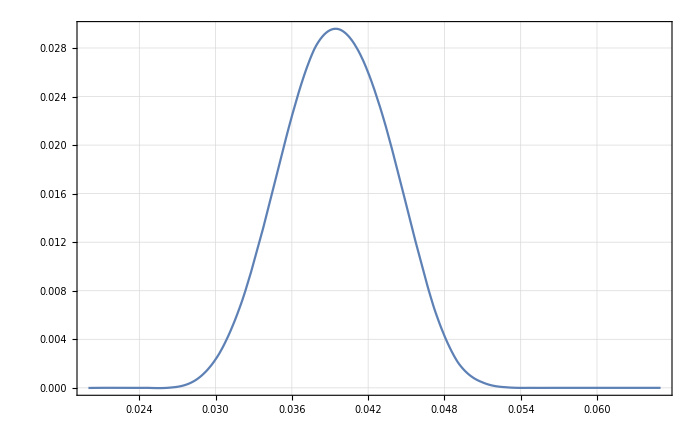

```mathematica
Plot[RefSpectrumInter[x,0.],{x,xStart,xEnd},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

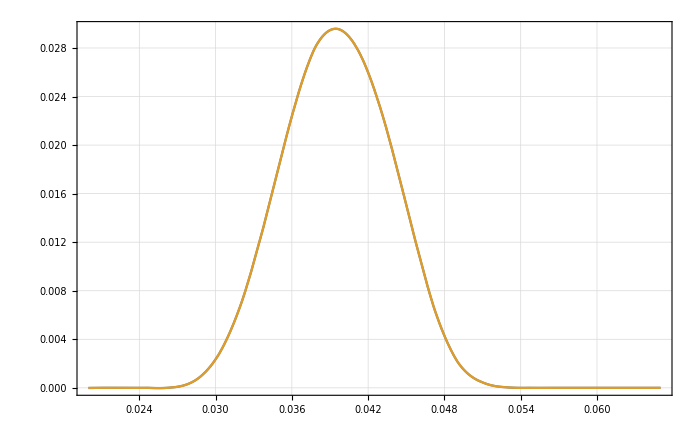

```mathematica
Plot[{RefSpectrumInter[x,0.],dBRxBSpectrumb0Inter[x,0.]},{x,xStart,xEnd},PlotRange->All]
```

```mathematica
dBRxBSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]]}]];
dBRxBSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]]}]];
dBRxBSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]]}]];
dBRxBSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0200009,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

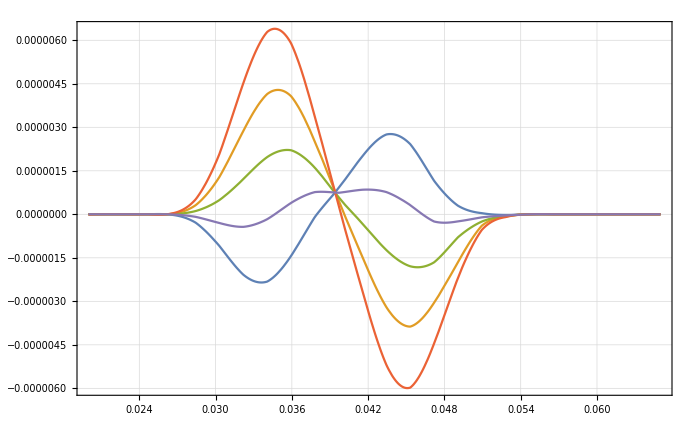

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectrumbm15Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumbm75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb0Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb15Inter[x,0.]
}
,{x,xStart,xEnd},PlotRange->All]
```

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectruma1040[[All,2]]/Total[dAlphaSpectruma1040[[All,2]]],dAlphaSpectruma1045[[All,2]]/Total[dAlphaSpectruma1045[[All,2]]],dAlphaSpectruma0[[All,2]]/Total[dAlphaSpectruma0[[All,2]]],dAlphaSpectruma1055[[All,2]]/Total[dAlphaSpectruma1055[[All,2]]],dAlphaSpectruma1060[[All,2]]/Total[dAlphaSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
dAlphaSpectruma1040[[All,2]]//Length
```

362

```mathematica
dAlphaSpectruma1055[[All,2]]//Length
```

264

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

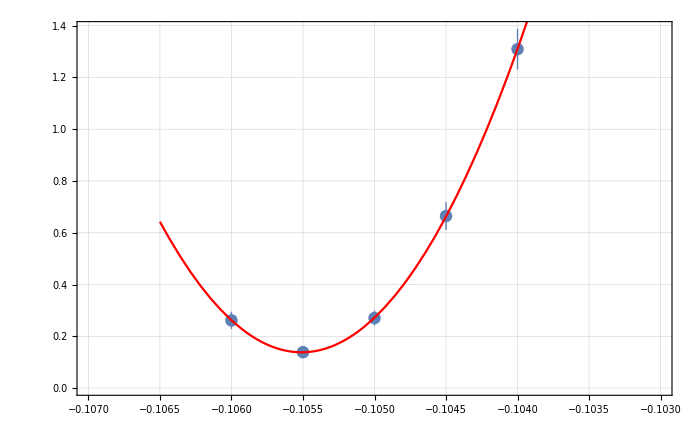
{{{1.30928×10^-9,6.64616×10^-10,2.70495×10^-10,1.38769×10^-10,2.61511×10^-10},{7.86811×10^-11,5.31884×10^-11,2.90487×10^-11,1.67193×10^-11,3.31935×10^-11}},a0 =  | -0.10551
FittedModel[1.38332×10^-10+0.000514142 (0.10551+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.10551 | 0.0000414574 | -2545.01 | 1.5439×10^-7
scale | 0.000514142 | 0.000043962 | 11.6952 | 0.00723196
yoffset | 1.38332×10^-10 | 1.41633×10^-11 | 9.76692 | 0.010321 | 
 | DF | SS | MS
Model | 3 | 650.7 | 216.9
Error | 2 | 0.00474935 | 0.00237467
Uncorrected Total | 5 | 650.705 | 
Corrected Total | 4 | 286.56 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
(-0.1055096205659537+0.105)/-0.105
```

0.00485353

```mathematica
0.004853529199559075*1/(5*10^-5)
```

97.0706

```mathematica
0.1*10^-3*97.07
```

0.009707

```mathematica
-0.105+(0.105*0.01)
```

-0.10395

```mathematica
-0.1042255483567612
```

```mathematica
AlphaInvest[[2,1,1,2]]
```

-0.10551

```mathematica
(AlphaInvest[[2,1,1,2]]+0.105)/(-0.105)/(5*10^-5)
```

97.0706

```mathematica
0.004853529199559075/(5*10^-5)
```

97.0706

# drF, k=4.43

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1050/"];
```

```mathematica
drFSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drF_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_drF_a-1050_179-264.txt}

```mathematica
drFSpectruma0=Flatten[Table[Import[drFSubFileNamesa0[[i]],"Table"],{i,1,Length[drFSubFileNamesa0]}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1040/"];
```

```mathematica
drFSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1040_179-264.txt}

```mathematica
drFSpectruma1040=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1040,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1045/"];
```

```mathematica
drFSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drF_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drF_a-1045_179-264.txt}

```mathematica
drFSpectruma1045=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1045,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1055/"];
```

```mathematica
drFSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_drF_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_drF_a-1055_179-264.txt}

```mathematica
drFSpectruma1055=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

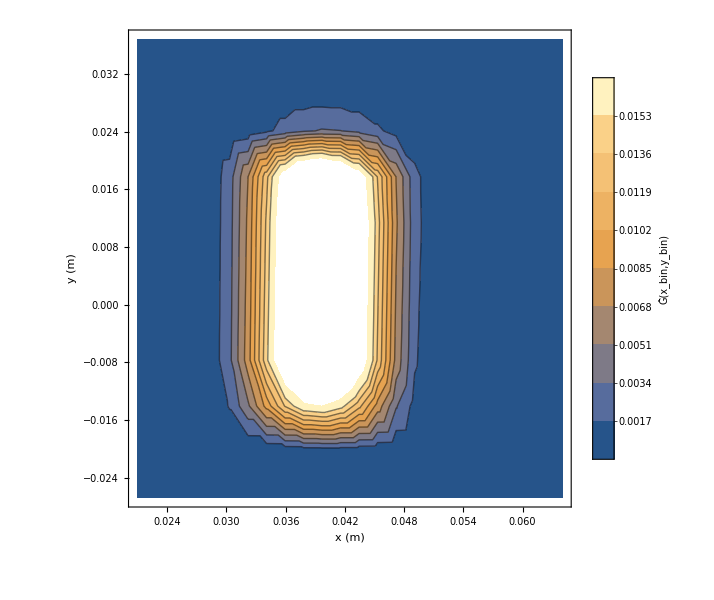

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drF/a-1060/"];
```

```mathematica
drFSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drF_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drF_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drFSpectruma1060=Flatten[Import[#,"Table"]&/@drFSubFileNamesa1060,1];
```

```mathematica
drFSpectruma1055[[All,2]]//Length
```

264

```mathematica
drFSpectruma1060[[All,2]]//Length
```

256

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1060[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,«11»,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,«214»},{«1»},{«1»}} cannot be transposed.

ListPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

ListPlot3D[Transpose[{{0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.025625,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.026875,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.028125,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.029375,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.030625,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.031875,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.033125,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.034375,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.035625,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.036875,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.038125,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.039375,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.040625,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.041875,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.043125,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.044375,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.045625,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.046875,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.048125,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.049375,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.050625,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.051875,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.053125,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375,0.054375},{-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225,-0.0177275,-0.0131825,-0.0086375,-0.0040925,0.0004525,0.0049975,0.0095425,0.0140875,0.0186325,0.0231775,0.0277225},{0.,4.47425×10^-7,6.02744×10^-7,5.91973×10^-7,5.81468×10^-7,5.71224×10^-7,5.61233×10^-7,5.51489×10^-7,5.41986×10^-7,5.32718×10^-7,4.75389×10^-8,0.,0.0000879969,0.000119268,0.000117147,0.000115078,0.000113059,0.000111091,0.00010917,0.000107297,0.00010543,0.0000104977,0.,0.000701745,0.000952878,0.00093608,0.000919691,0.000903701,0.000888099,0.000872877,0.000858025,0.000839179,0.0000834952,3.5836×10^-6,0.00239433,0.00325997,0.00320344,0.00314825,0.00309437,0.00304178,0.00299043,0.00294031,0.00284975,0.000327453,0.000037155,0.00559804,0.00767238,0.00754283,0.00741622,0.0072925,0.00717161,0.00705348,0.00693807,0.00664837,0.000848306,0.000165113,0.0105384,0.0145972,0.0143612,0.0141301,0.0139039,0.0136825,0.0134658,0.0132537,0.0125429,0.00178018,0.000466438,0.0171219,0.0240336,0.0236801,0.0233297,0.022985,0.0226459,0.0223126,0.021985,0.0205558,0.00321438,0.00096978,0.0246906,0.0351399,0.0347259,0.0342925,0.0338625,0.0334367,0.0330126,0.0325974,0.0301499,0.00514795,0.00159149,0.0322596,0.0464223,0.0460451,0.0455901,0.0451366,0.0446842,0.0442341,0.0437851,0.0401522,0.0544281,0.0540196,0.0492595,0.00942923,0.00266363,0.0428271,0.0626197,0.0626168,0.0623765,0.0621288,0.0618731,0.0616107,0.0613375,0.05573,0.011033,0.00295451,0.0436845,0.0643068,0.0645062,0.0644428,0.06436,0.0642704,0.064177,0.0640722,0.0580227,0.0118582,0.00307535,0.0419021,0.0620969,0.0624748,0.062525,0.0625699,0.0626116,0.062647,0.0626745,0.0564962,0.0119396,0.00302753,0.0378254,0.056474,0.0569931,0.0571759,0.0573524,0.0575234,0.057676,0.0578325,0.0519097,0.0113495,0.00278236,0.0317647,0.0478165,0.0484712,0.0487879,0.0490987,0.0494035,0.049702,0.0499907,0.0446863,0.010074,0.00232516,0.0244053,0.0370302,0.0377635,0.0381813,0.0385945,0.0390033,0.0394075,0.0398029,0.0354729,0.00833864,0.00171419,0.0167922,0.0256606,0.0263695,0.0268248,0.0272801,0.0277306,0.0281806,0.0286239,0.0254997,0.00619068,0.00108409,0.0098629,0.015269,0.015852,0.0162725,0.0166946,0.0171238,0.0175441,0.0179669,0.0160051,0.00404876,0.000562323,0.00473851,0.00745261,0.00782324,0.00811736,0.00841886,0.00872724,0.00904185,0.00936082,0.00832003,0.00225943,0.000226292,0.00197739,0.00313934,0.00331034,0.00345557,0.00360644,0.00376261,0.00392418,0.0040914,0.00361137,0.00103357,0.0000710994,0.000718059,0.00114017,0.00121167,0.00127949,0.00135001,0.00142319,0.00149911,0.00157783,0.00141378,0.000393956,0.0000121256,0.000189393,0.000301593,0.000326884,0.000353033,0.000380663,0.000409764,0.000440381,0.000472558,0.000439617,0.00011556,4.52877×10^-7,0.0000258848,0.0000418482,0.0000476277,0.0000539891,0.0000609723,0.000068562,0.0000768318,0.0000858192,0.0000850529,0.0000185858,0.,6.46386×10^-7,1.16186×10^-6,1.71743×10^-6,2.60735×10^-6,2.55523×10^-6,3.22825×10^-6,4.01108×10^-6,5.00119×10^-6,5.74377×10^-6,1.0528×10^-6}}],PlotRange→All]

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.0250021,-0.0199964} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
drFSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]]}]];
```

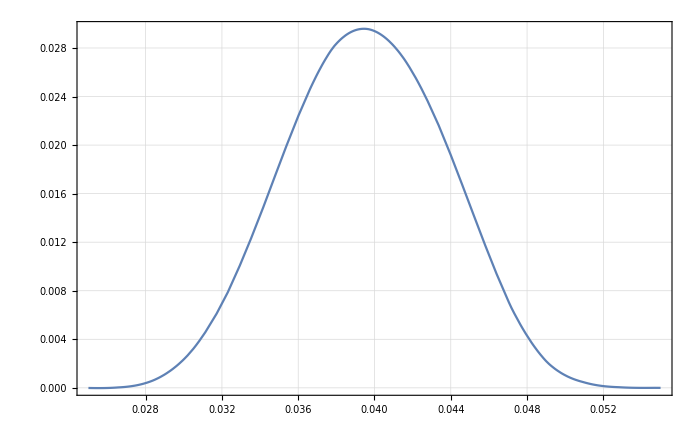

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

```mathematica
drFSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]]}]];
drFSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]]}]];
drFSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]]}]];
```

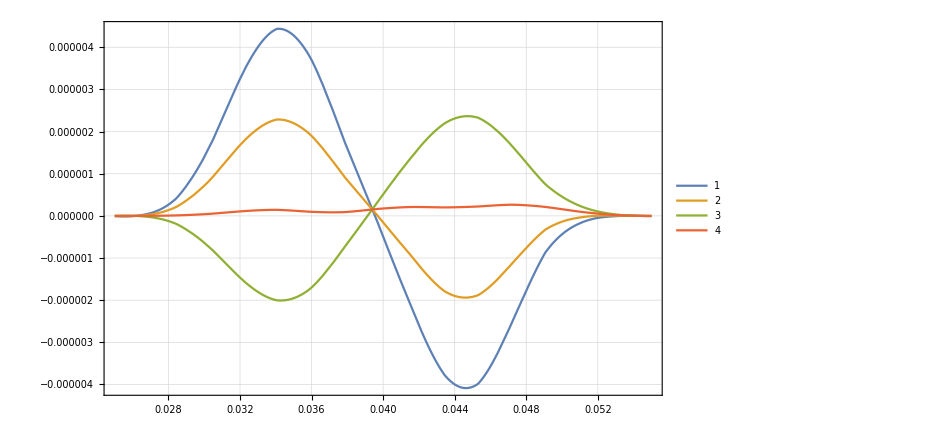

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drFSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drFSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
rFDataList={drFSpectruma1040[[All,2]]/Total[drFSpectruma1040[[All,2]]],drFSpectruma1045[[All,2]]/Total[drFSpectruma1045[[All,2]]],drFSpectruma0[[All,2]]/Total[drFSpectruma0[[All,2]]],drFSpectruma1055[[All,2]]/Total[drFSpectruma1055[[All,2]]],drFSpectruma1060[[All,2]]/Total[drFSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

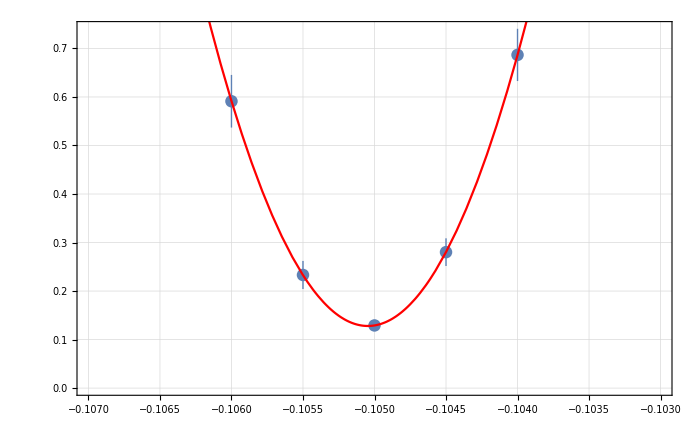
{{{6.86703×10^-10,2.80175×10^-10,1.29136×10^-10,2.33128×10^-10,5.91184×10^-10},{5.38263×10^-11,2.85119×10^-11,1.12789×10^-11,2.89544×10^-11,5.42352×10^-11}},a0 =  | -0.105047
FittedModel[1.28043×10^-10+0.000509836 (0.105047+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105047 | 0.0000275451 | -3813.62 | 6.87583×10^-8
scale | 0.000509836 | 0.0000382191 | 13.3398 | 0.0055726
yoffset | 1.28043×10^-10 | 1.06022×10^-11 | 12.077 | 0.00678645 | 
 | DF | SS | MS
Model | 3 | 574.056 | 191.352
Error | 2 | 0.000169658 | 0.0000848291
Uncorrected Total | 5 | 574.056 | 
Corrected Total | 4 | 181.206 |  | ,-Graphics-}

```mathematica
rFInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rFDataList,bList, 4]
```

```mathematica
(rFInvest[[2,1,1,2]]+0.105)/-0.105
```

0.000442949

```mathematica
0.000442948920583481/(10^-4)
```

4.42949

# drA, k=157.04

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_drA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1040/"];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1040/Cluster_Try"];
```

```mathematica
drASubFileNamesa1040Cluster=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_179-264.txt}

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040Cluster=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040Cluster,1];
```

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

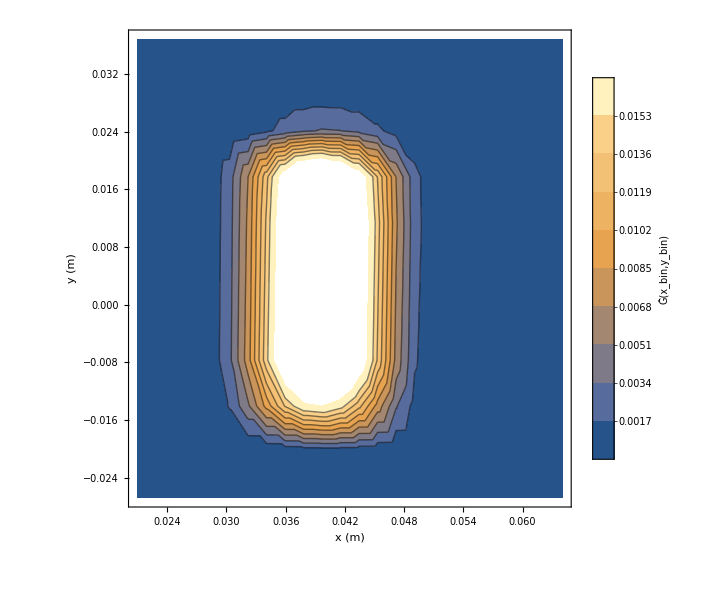

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
drASpectruma1040InterCluster=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040Cluster[[All,2]]/Total[drASpectruma1040Cluster[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

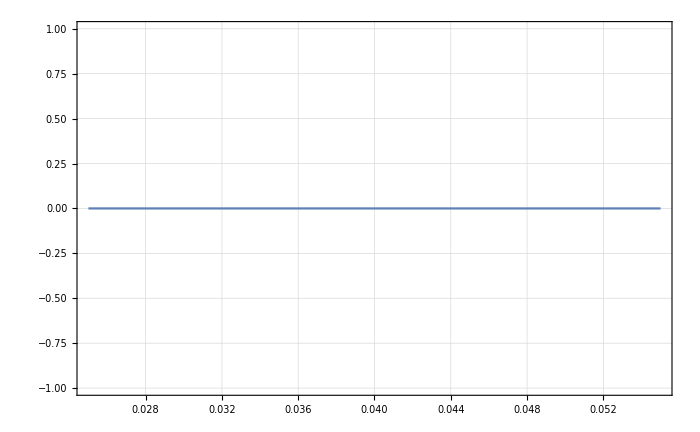

```mathematica
Plot[drASpectruma1040Inter[x,0.]-drASpectruma1040InterCluster[x,0.],{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
1.97*10^-3
```

0.00197

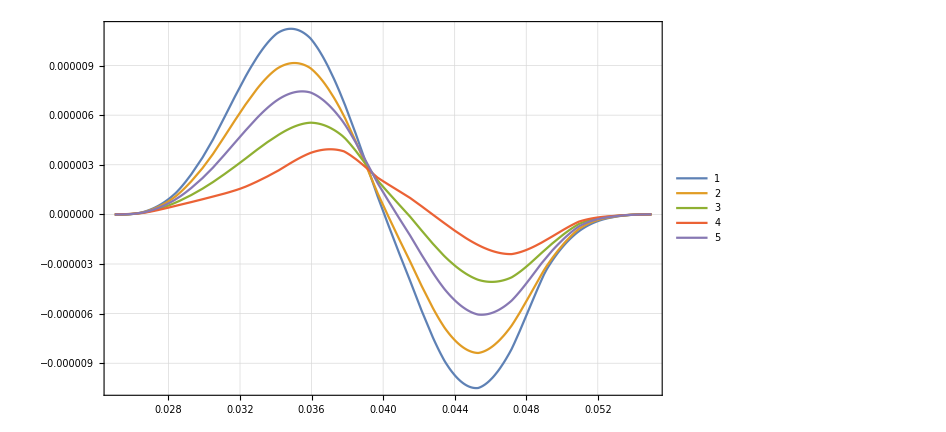

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

### a=-1065

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1065/"];
```

```mathematica
drASubFileNamesa1065=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1065_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1065_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1065=Flatten[Import[#,"Table"]&/@drASubFileNamesa1065,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1065[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1070

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1070/"];
```

```mathematica
drASubFileNamesa1070=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1070_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1070_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1070=Flatten[Import[#,"Table"]&/@drASubFileNamesa1070,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1070[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1075

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drA/a-1075/"];
```

```mathematica
drASubFileNamesa1075=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drA_a-1075_1-49.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_50-98.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_99-106.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_107-122.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_123-138.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_139-154.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_155-178.txt,TransferResult_08-09-20_SC_opt_C_drA_a-1075_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1075=Flatten[Import[#,"Table"]&/@drASubFileNamesa1075,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1075[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]],drASpectruma1065[[All,2]]/Total[drASpectruma1065[[All,2]]],drASpectruma1070[[All,2]]/Total[drASpectruma1070[[All,2]]],drASpectruma1075[[All,2]]/Total[drASpectruma1075[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060,-0.1065,-0.1070,-0.1075}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1065,-0.107,-0.1075}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

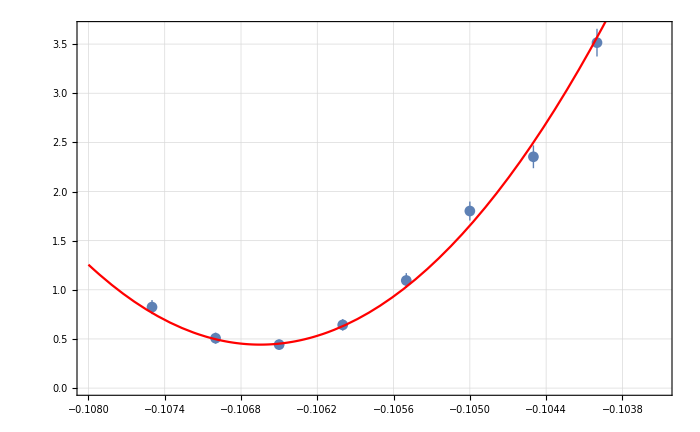
{{{3.51471×10^-9,2.35326×10^-9,1.80157×10^-9,1.09474×10^-9,6.43061×10^-10,4.42288×10^-10,5.07741×10^-10,8.24147×10^-10},{1.40892×10^-10,1.16125×10^-10,9.64692×10^-11,7.53158×10^-11,5.8544×10^-11,5.08038×10^-11,5.64233×10^-11,7.15789×10^-11}},a0 =  | -0.106649
FittedModel[4.42288×10^-10+0.000445521 (0.106649+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106649 | 0.0000513687 | -2076.14 | 4.92061×10^-16
scale | 0.000445521 | 0.0000263228 | 16.9253 | 0.000013168
yoffset | 4.42288×10^-10 | 2.94575×10^-11 | 15.0145 | 0.0000237319 | 
 | DF | SS | MS
Model | 3 | 1997.37 | 665.79
Error | 5 | 5.62228 | 1.12446
Uncorrected Total | 8 | 2002.99 | 
Corrected Total | 7 | 744.691 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rADataList,bList, 4]
```

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

157.014

```mathematica
((-0.10664865012298552+0.105)/-0.105)/(10^-4)
```

157.014

# dB, k=69.93

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1050/"];
```

```mathematica
dBSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1050_179-264.txt}

```mathematica
dBSpectruma0=Flatten[Table[Import[dBSubFileNamesa0[[i]],"Table"],{i,1,Length[dBSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1040/"];
```

```mathematica
dBSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1040_179-264.txt}

```mathematica
dBSpectruma1040=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1045/"];
```

```mathematica
dBSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dB_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1045_179-264.txt}

```mathematica
dBSpectruma1045=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1055/"];
```

```mathematica
dBSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dB_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dB_a-1055_179-264.txt}

```mathematica
dBSpectruma1055=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

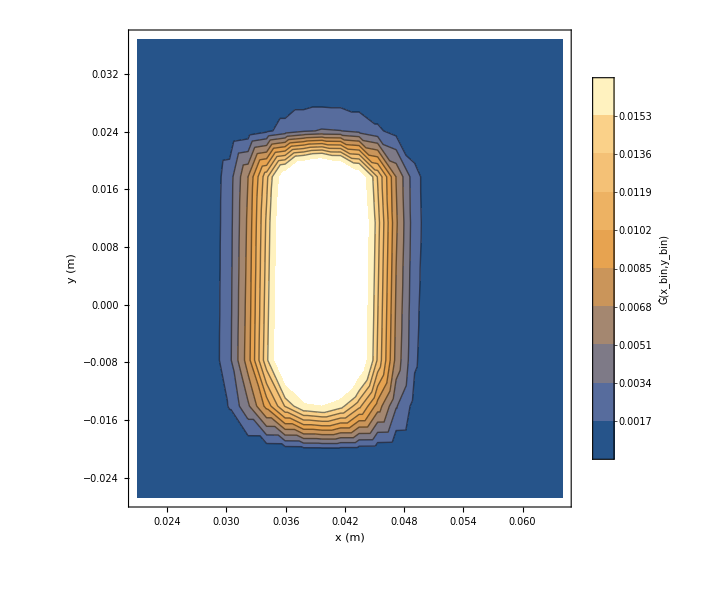

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dB/a-1060/"];
```

```mathematica
dBSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dB_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dB_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dBSpectruma1060=Flatten[Import[#,"Table"]&/@dBSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]]}]];
dBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]]}]];
dBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]]}]];
dBSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]}]];
```

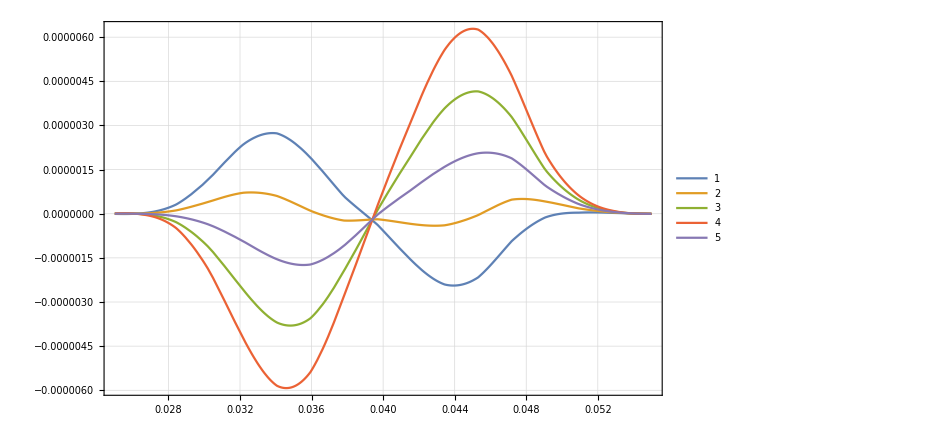

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dBSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
BDataList={dBSpectruma1040[[All,2]]/Total[dBSpectruma1040[[All,2]]],dBSpectruma1045[[All,2]]/Total[dBSpectruma1045[[All,2]]],dBSpectruma0[[All,2]]/Total[dBSpectruma0[[All,2]]],dBSpectruma1055[[All,2]]/Total[dBSpectruma1055[[All,2]]],dBSpectruma1060[[All,2]]/Total[dBSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

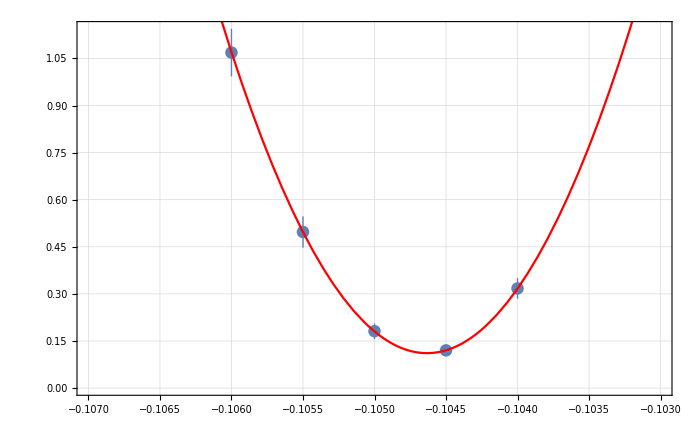
{{{3.17415×10^-10,1.20191×10^-10,1.81208×10^-10,4.97177×10^-10,1.06859×10^-9},{3.27248×10^-11,1.16634×10^-11,2.47023×10^-11,4.97713×10^-11,7.57612×10^-11}},a0 =  | -0.104633
FittedModel[1.11361×10^-10+0.000512848 (0.104633+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104633 | 0.00003187 | -3283.12 | 9.27742×10^-8
scale | 0.000512848 | 0.0000411871 | 12.4517 | 0.00638805
yoffset | 1.11361×10^-10 | 1.1474×10^-11 | 9.70545 | 0.0104501 | 
 | DF | SS | MS
Model | 3 | 552.813 | 184.271
Error | 2 | 0.00192816 | 0.000964081
Uncorrected Total | 5 | 552.815 | 
Corrected Total | 4 | 222.042 |  | ,-Graphics-}

```mathematica
BInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
.106*6.930
```

0.73458

```mathematica
.75*.1
```

0.075

```mathematica
.15*69.93
```

10.4895

```mathematica
.15*69.93
```

10.4895

```mathematica
(BInvest[[2,1,1,2]]+0.105)/-0.105
```

-0.00349668

```mathematica
-0.003496680950444102/(5*10^-5)
```

-69.9336

```mathematica
.1*97.07
```

9.707

```mathematica
Sqrt[10.489500000000001^2+9.707^2]
```

14.2918

```mathematica
14*10^-3.
```

0.014

```mathematica
%*100
```

1.4

```mathematica
18*4
```

72

```mathematica
1/7.83
```

0.127714

# drRxB, k=43.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1050/"];
```

```mathematica
drRxBSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1050_179-264.txt}

```mathematica
drRxBSpectruma0=Flatten[Table[Import[drRxBSubFileNamesa0[[i]],"Table"],{i,1,Length[drRxBSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1040/"];
```

```mathematica
drRxBSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1040_179-264.txt}

```mathematica
drRxBSpectruma1040=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1045/"];
```

```mathematica
drRxBSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_drRxB_a-1045_179-264.txt}

```mathematica
drRxBSpectruma1045=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1055/"];
```

```mathematica
drRxBSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_drRxB_a-1055_179-264.txt}

```mathematica
drRxBSpectruma1055=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

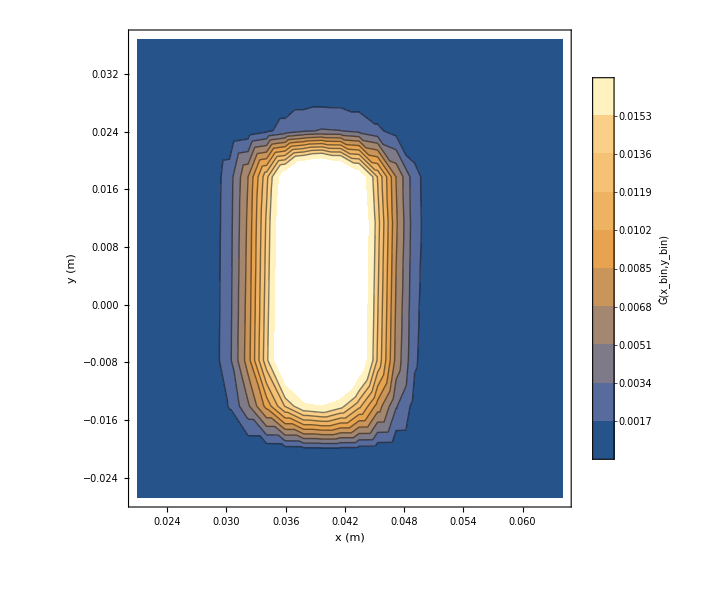

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drRxB/a-1060/"];
```

```mathematica
drRxBSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_drRxB_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drRxBSpectruma1060=Flatten[Import[#,"Table"]&/@drRxBSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drRxBSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
drRxBSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1040[[All,2]]/Total[drRxBSpectruma1040[[All,2]]]}]];
drRxBSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1045[[All,2]]/Total[drRxBSpectruma1045[[All,2]]]}]];
drRxBSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]]}]];
drRxBSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drRxBSpectruma1060[[All,2]]/Total[drRxBSpectruma1060[[All,2]]]}]];
```

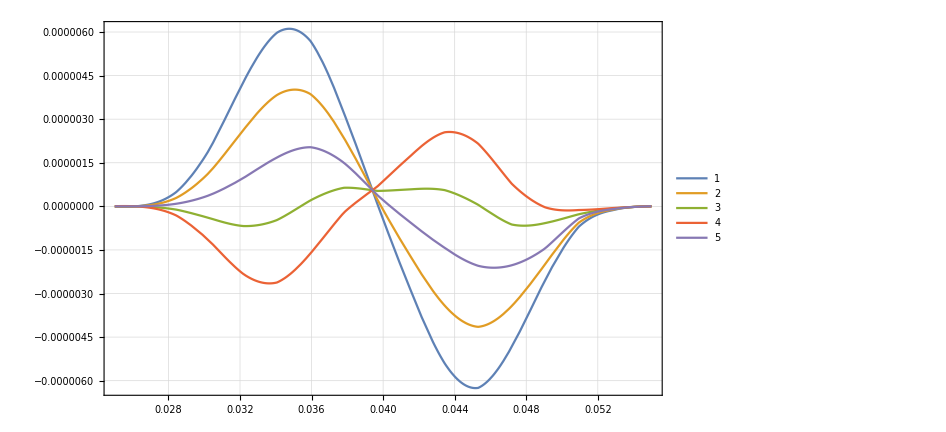

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drRxBSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drRxBSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
rRxBDataList={drRxBSpectruma1040[[All,2]]/Total[drRxBSpectruma1040[[All,2]]],drRxBSpectruma1045[[All,2]]/Total[drRxBSpectruma1045[[All,2]]],drRxBSpectruma0[[All,2]]/Total[drRxBSpectruma0[[All,2]]],drRxBSpectruma1055[[All,2]]/Total[drRxBSpectruma1055[[All,2]]],drRxBSpectruma1060[[All,2]]/Total[drRxBSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

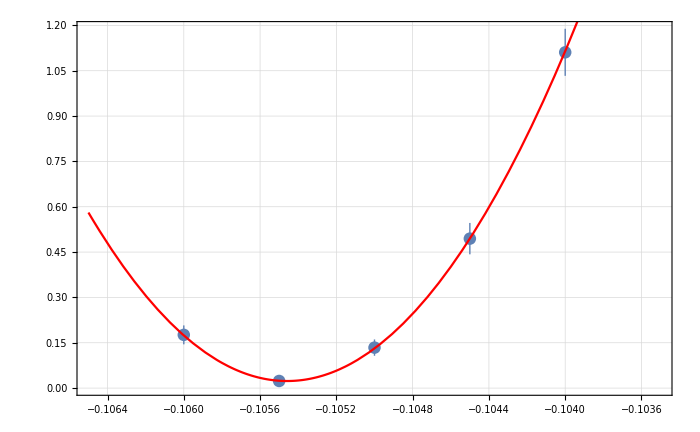
{{{1.11093×10^-9,4.94473×10^-10,1.33884×10^-10,2.35734×10^-11,1.76109×10^-10},{7.78298×10^-11,5.18879×10^-11,2.69823×10^-11,1.22177×10^-11,3.12751×10^-11}},a0 =  | -0.105458
FittedModel[2.34228×10^-11+0.000513376 (0.105458+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105458 | 0.000036153 | -2916.99 | 1.17525×10^-7
scale | 0.000513376 | 0.0000412367 | 12.4495 | 0.00639024
yoffset | 2.34228×10^-11 | 1.12144×10^-11 | 2.08863 | 0.171959 | 
 | DF | SS | MS
Model | 3 | 354.587 | 118.196
Error | 2 | 0.020374 | 0.010187
Uncorrected Total | 5 | 354.607 | 
Corrected Total | 4 | 272.567 |  | ,-Graphics-}

```mathematica
rRxBInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rRxBDataList,bList, 4]
```

```mathematica
((rRxBInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

43.6187

```mathematica
((rRxBInvest[[2,1,1,2]]+0.105)/-0.105)*100
```

0.436187

# dG1, k=0.135

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1050/"];
```

```mathematica
dG1SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1050_179-264.txt}

```mathematica
dG1Spectruma0=Flatten[Table[Import[dG1SubFileNamesa0[[i]],"Table"],{i,1,Length[dG1SubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1040/"];
```

```mathematica
dG1SubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG1_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG1_a-1040_179-264.txt}

```mathematica
dG1Spectruma1040=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1045/"];
```

```mathematica
dG1SubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1045_179-264.txt}

```mathematica
dG1Spectruma1045=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1055/"];
```

```mathematica
dG1SubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1055_179-264.txt}

```mathematica
dG1Spectruma1055=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

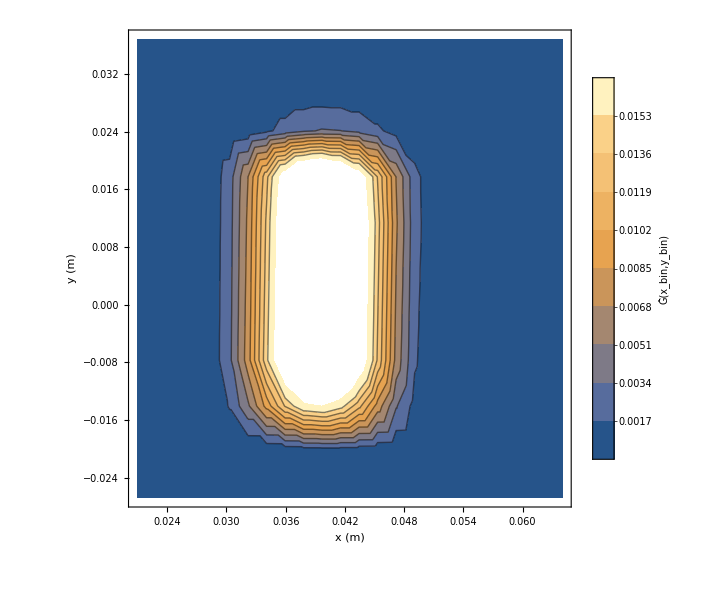

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG1/a-1060/"];
```

```mathematica
dG1SubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG1_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG1_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dG1Spectruma1060=Flatten[Import[#,"Table"]&/@dG1SubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dG1Spectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dG1Spectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1040[[All,2]]/Total[dG1Spectruma1040[[All,2]]]}]];
dG1Spectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1045[[All,2]]/Total[dG1Spectruma1045[[All,2]]]}]];
dG1Spectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]]}]];
dG1Spectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1060[[All,2]]/Total[dG1Spectruma1060[[All,2]]]}]];
```

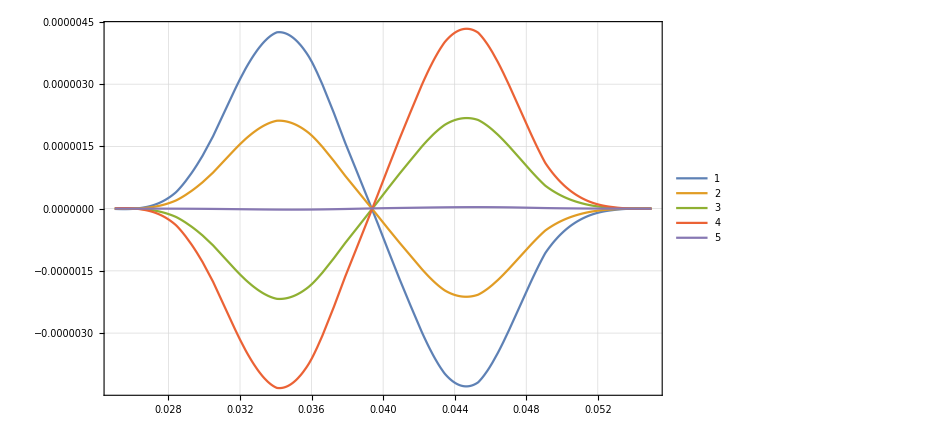

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dG1Spectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dG1Spectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
BDataList={dG1Spectruma1040[[All,2]]/Total[dG1Spectruma1040[[All,2]]],dG1Spectruma1045[[All,2]]/Total[dG1Spectruma1045[[All,2]]],dG1Spectruma0[[All,2]]/Total[dG1Spectruma0[[All,2]]],dG1Spectruma1055[[All,2]]/Total[dG1Spectruma1055[[All,2]]],dG1Spectruma1060[[All,2]]/Total[dG1Spectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

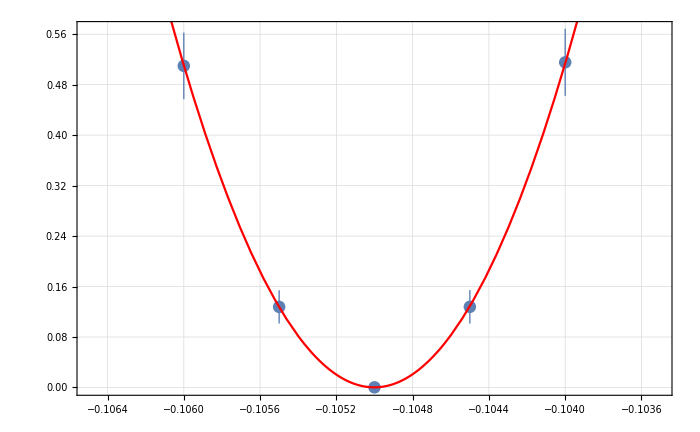
{{{5.15438×10^-10,1.2786×10^-10,2.17303×10^-13,1.2776×10^-10,5.09835×10^-10},{5.31564×10^-11,2.65551×10^-11,1.19504×10^-12,2.63586×10^-11,5.27491×10^-11}},a0 =  | -0.105001
FittedModel[2.15056×10^-13+0.000512007 (0.105001+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105001 | 0.0000258456 | -4062.65 | 6.05873×10^-8
scale | 0.000512007 | 0.0000335399 | 15.2656 | 0.00426372
yoffset | 2.15056×10^-13 | 1.19452×10^-12 | 0.180036 | 0.873715 | 
 | DF | SS | MS
Model | 3 | 234.149 | 78.0496
Error | 2 | 0.00318623 | 0.00159312
Uncorrected Total | 5 | 234.152 | 
Corrected Total | 4 | 233.044 |  | ,-Graphics-}

```mathematica
BInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
((BInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

0.134947

# dG2, k=0.069

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1050/"];
```

```mathematica
dG2SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dG2_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1050_179-264.txt}

```mathematica
dG2Spectruma0=Flatten[Table[Import[dG2SubFileNamesa0[[i]],"Table"],{i,1,Length[dG2SubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1040/"];
```

```mathematica
dG2SubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dG2_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_C_dG2_a-1040_179-264.txt}

```mathematica
dG2Spectruma1040=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1045/"];
```

```mathematica
dG2SubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dG2_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dG2_a-1045_179-264.txt}

```mathematica
dG2Spectruma1045=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1055/"];
```

```mathematica
dG2SubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG2_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1055_179-264.txt}

```mathematica
dG2Spectruma1055=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«11»,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«20» «1»} cannot be transposed.

ListContourPlot::arrayerr: Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«12»,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«20» «1»}] must be a valid array.

ListContourPlot[Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0303125,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0321875,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0340625,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0359375,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0378125,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0396875,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0415625,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0434375,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0453125,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0471875,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0490625,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0509375,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0528125,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0546875,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0565625,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0584375,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0603125,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0621875,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625,0.0640625},{-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822,-0.026818,-0.020454,-0.01409,-0.007726,-0.001362,0.005002,0.011366,0.01773,0.024094,0.030458,0.036822},0.197555 Symbol[]}],BaseStyle→25,ImageSize→600,InterpolationOrder→1,Contours→9,FrameLabel→{{y (m),None},{x (m),None}},PlotLegends→BarLegend[Automatic,LabelStyle→25,LegendLabel→Ĝ(x_bin,y_bin)]]

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dG2/a-1060/"];
```

```mathematica
dG2SubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dG2_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dG2_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dG2Spectruma1060=Flatten[Import[#,"Table"]&/@dG2SubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dG2Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dG2Spectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG1Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]]}]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«11»,0.0246875,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«19» «1»} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0209375,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,0.0228125,«12»,0.0246875,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0265625,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,0.0284375,«214»},«1»,«19» «1»}] does not contain a list of data and coordinates.

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dG2Spectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1040[[All,2]]/Total[dG2Spectruma1040[[All,2]]]}]];
dG2Spectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1045[[All,2]]/Total[dG2Spectruma1045[[All,2]]]}]];
dG2Spectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]]}]];
dG2Spectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dG2Spectruma1060[[All,2]]/Total[dG2Spectruma1060[[All,2]]]}]];
```

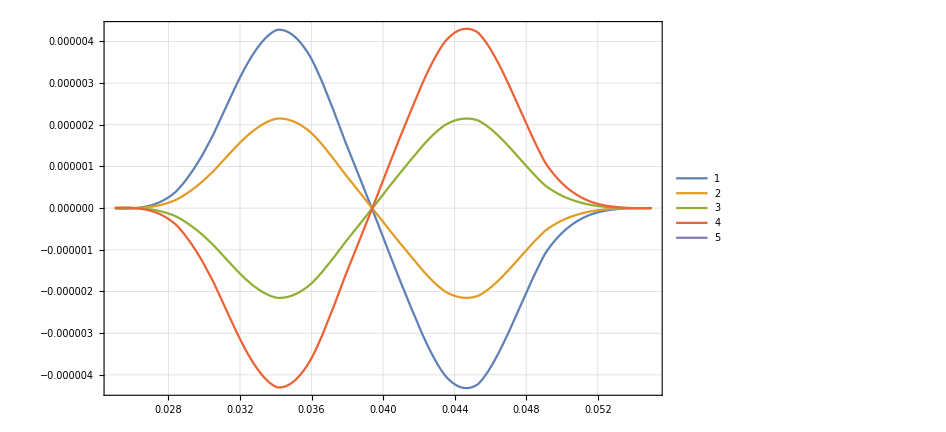

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dG2Spectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dG2Spectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
BDataList={dG2Spectruma1040[[All,2]]/Total[dG2Spectruma1040[[All,2]]],dG2Spectruma1045[[All,2]]/Total[dG2Spectruma1045[[All,2]]],dG2Spectruma0[[All,2]]/Total[dG2Spectruma0[[All,2]]],dG2Spectruma1055[[All,2]]/Total[dG2Spectruma1055[[All,2]]],dG2Spectruma1060[[All,2]]/Total[dG2Spectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

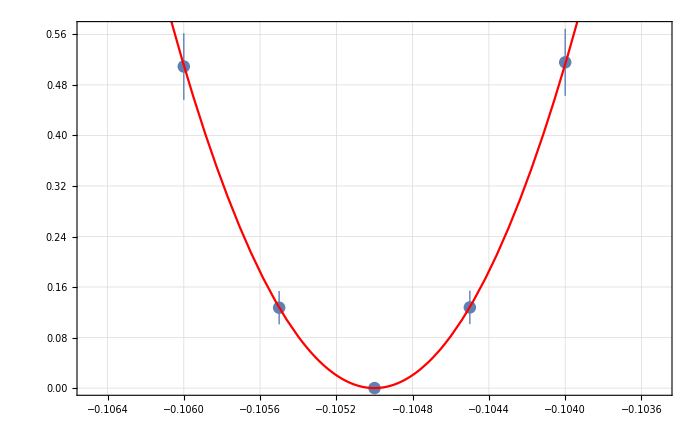
{{{5.15775×10^-10,1.27743×10^-10,2.5683×10^-17,1.27295×10^-10,5.09157×10^-10},{5.30913×10^-11,2.64645×10^-11,1.03735×10^-14,2.63815×10^-11,5.27903×10^-11}},a0 =  | -0.105001
FittedModel[5.79854×10^-24+0.000511976 (0.105001+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105001 | 0.0000258279 | -4065.4 | 6.05054×10^-8
scale | 0.000511976 | 0.0000334707 | 15.2963 | 0.00424674
yoffset | 5.79854×10^-24 | 2.17491×10^-14 | 2.66611×10^-10 | 1. | 
 | DF | SS | MS
Model | 3 | 233.979 | 77.9929
Error | 2 | 0.00612162 | 0.00306081
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
g2Invest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],BDataList,bList, 4]
```

```mathematica
((-0.10500072280654503+0.105)/-0.105)/(10^-4)
```

0.0688387

```mathematica
((g2Invest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

0.0688387

# drd, k=187.97

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_drD_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_drD_a-1050_179-264.txt}

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1035/"];
```

```mathematica
drDSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1035_179-264.txt}

```mathematica
drDSpectruma1035=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1030/"];
```

```mathematica
drDSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drD_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1030_179-264.txt}

```mathematica
drDSpectruma1030=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1020/"];
```

```mathematica
drDSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1019_179-264.txt}

```mathematica
drDSpectruma1020=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_drD_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_drD_a-1040_179-264.txt}

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1045_179-264.txt}

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1055_179-264.txt}

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

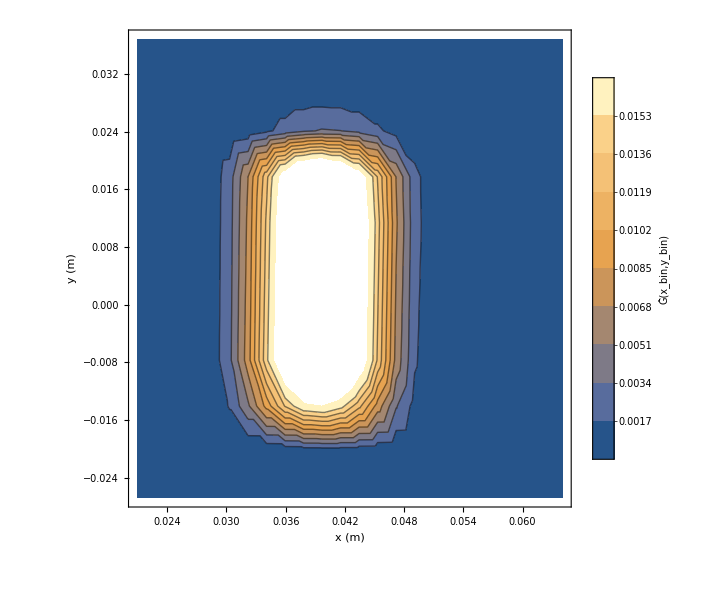

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_drD_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_drD_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

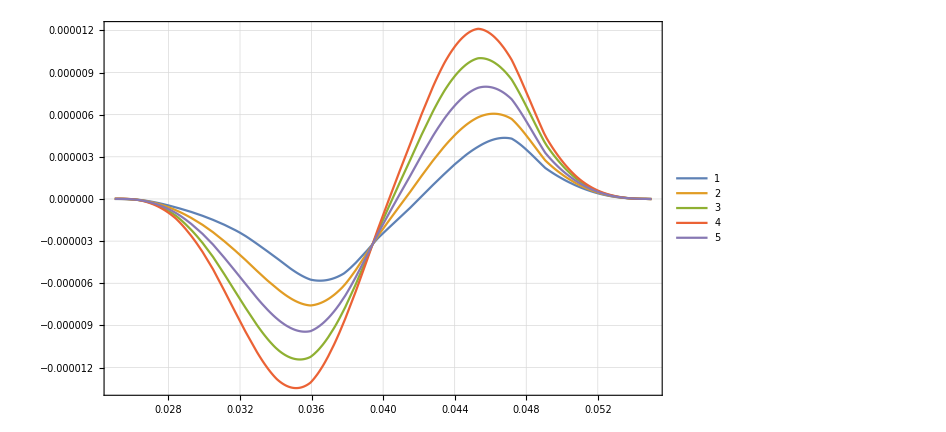

```mathematica
Plot[{
RefSpectrumInter[x,0.]-drDSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
rDDataList={drDSpectruma1020[[All,2]]/Total[drDSpectruma1020[[All,2]]],drDSpectruma1030[[All,2]]/Total[drDSpectruma1030[[All,2]]],drDSpectruma1035[[All,2]]/Total[drDSpectruma1035[[All,2]]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.102,-0.103,-0.1035,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

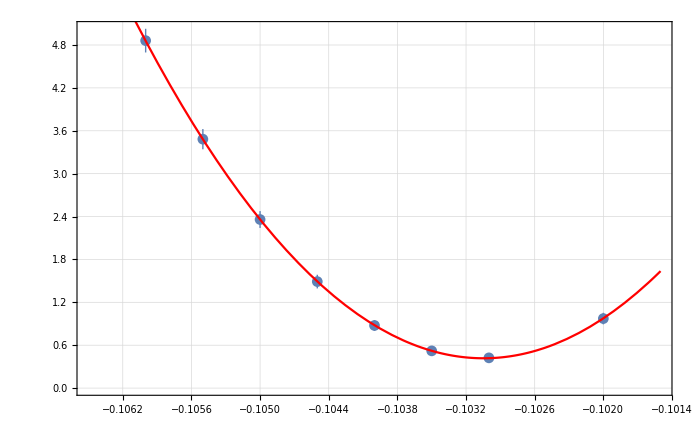
{{{9.72613×10^-10,4.23104×10^-10,5.2079×10^-10,8.75997×10^-10,1.49013×10^-9,2.35856×10^-9,3.4825×10^-9,4.86114×10^-9},{8.05613×10^-11,5.84884×10^-11,6.24937×10^-11,7.60636×10^-11,9.5516×10^-11,1.17637×10^-10,1.41231×10^-10,1.65669×10^-10}},a0 =  | -0.103047
FittedModel[4.17262×10^-10+0.000509271 (0.103047+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103047 | 0.0000439952 | -2342.24 | 2.69246×10^-16
scale | 0.000509271 | 0.0000227131 | 22.4219 | 3.27895×10^-6
yoffset | 4.17262×10^-10 | 3.55904×10^-11 | 11.724 | 0.0000793702 | 
 | DF | SS | MS
Model | 3 | 2514.53 | 838.177
Error | 5 | 0.0114451 | 0.00228902
Uncorrected Total | 8 | 2514.54 | 
Corrected Total | 7 | 1161.97 |  | ,-Graphics-}

```mathematica
rDInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],rDDataList,bList, 4]
```

```mathematica
(-0.10304725773676074+0.105)/-0.105
```

-0.0185975

```mathematica
-0.018597545364183402/10^-4
```

-185.975

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-185.975

# dXAShift, k=57.14/1.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1050/"];
```

```mathematica
dXAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_179-264.txt}

```mathematica
dXAShiftSpectruma0=Flatten[Table[Import[dXAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1020/"];
```

```mathematica
dXAShiftSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1019_179-264.txt}

```mathematica
dXAShiftSpectruma1020=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1030/"];
```

```mathematica
dXAShiftSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1030_179-264.txt}

```mathematica
dXAShiftSpectruma1030=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1035/"];
```

```mathematica
dXAShiftSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1035_179-264.txt}

```mathematica
dXAShiftSpectruma1035=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1040/"];
```

```mathematica
dXAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_179-264.txt}

```mathematica
dXAShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1045/"];
```

```mathematica
dXAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_179-264.txt}

```mathematica
dXAShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1055/"];
```

```mathematica
dXAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_179-264.txt}

```mathematica
dXAShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

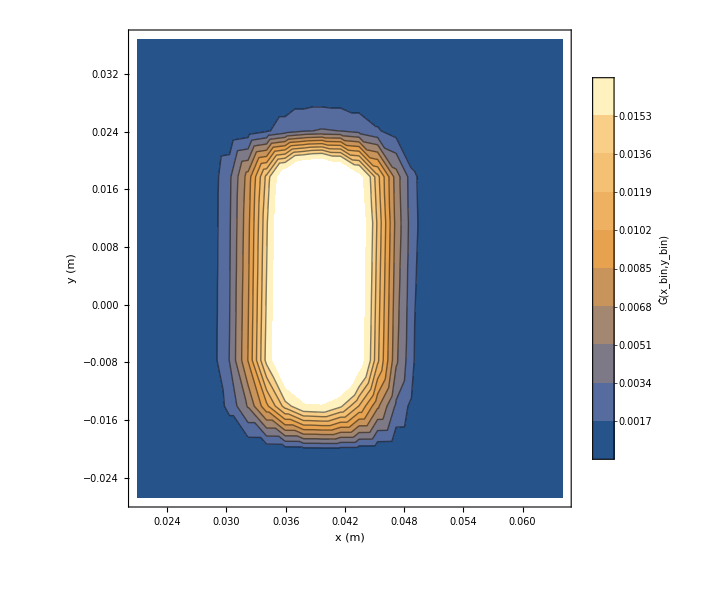

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1060/"];
```

```mathematica
dXAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXAShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dXAShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]}]];
dXAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]}]];
dXAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}]];
dXAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}]];
```

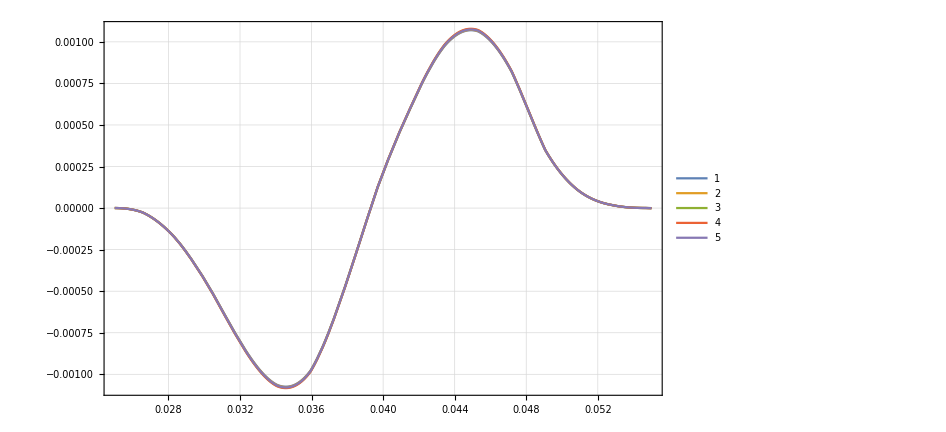

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXAShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXAShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList,XAShiftInvest]
```

```mathematica
XAShiftDataList={dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

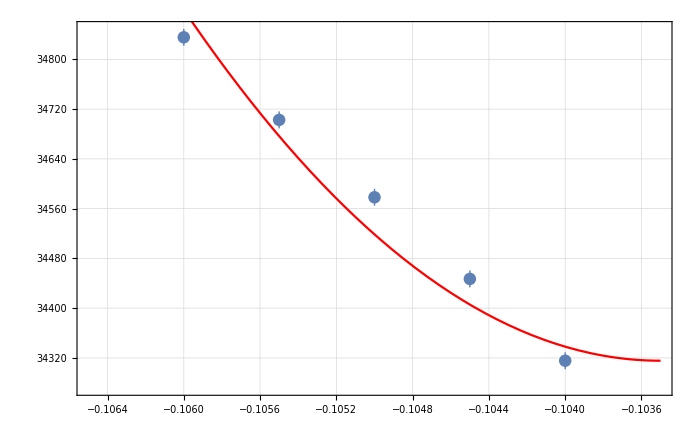
{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.1035
FittedModel[0.0000343155+0.0902549 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000247235 | -418.63 | 5.70605×10^-6
scale | 0.0902549 | 0.0146073 | 6.17876 | 0.0252075
yoffset | 0.0000343155 | 2.92413×10^-8 | 1173.53 | 7.26125×10^-7 | 
 | DF | SS | MS
Model | 3 | 3.20164×10^7 | 1.06721×10^7
Error | 2 | 45.011 | 22.5055
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
XAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

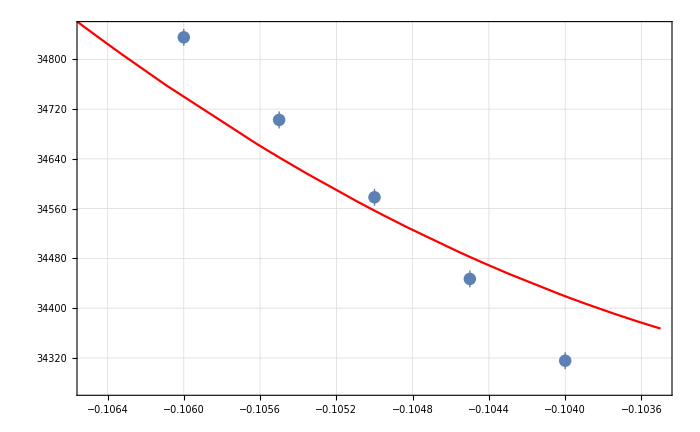
{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.101429
FittedModel[0.000034271+0.022403 (0.101429+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101429 | 0.00233567 | -43.4259 | 0.000529855
scale | 0.022403 | 0.0146073 | 1.53369 | 0.264839
yoffset | 0.000034271 | 1.816×10^-7 | 188.717 | 0.0000280776 | 
 | DF | SS | MS
Model | 3 | 3.20163×10^7 | 1.06721×10^7
Error | 2 | 135.795 | 67.8977
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
XAShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

```mathematica
((XAShiftInvest2[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-136.048

```mathematica
-136.04810567554844*0.00025
```

-0.034012

```mathematica
Export["MergerTransport/NC_opt_drF/b"<>ToString[IntegerPart[a*10000]]<>"/TransferResult_08-09-20_NC_opt_C_BSOn_drF_b"<>ToString[IntegerPart[a*10000]]<>"_"<>ToString[Bins[[1]]]<>"-"<>ToString[Bins[[2]]]<>".txt",BinwYShiftPrec44OriginalBinsb0NewBGrad,"Table"];
```

```mathematica
((XAShiftInvest[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-57.1429

```mathematica
0.0003+0.0003
```

0.0006

```mathematica
0.0006/6
```

0.0001

```mathematica
Table[i,{i,-0.0003,0.0003,0.0006/4}]
```

{-0.0003,-0.00015,0.,0.00015,0.0003}

# dYAShift, k=136.91

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1050/"];
```

```mathematica
dYAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1050_179-264.txt}

```mathematica
dYAShiftSpectruma0=Flatten[Table[Import[dYAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1035

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1035/"];
```

```mathematica
dYAShiftSubFileNamesa1035=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1035_179-264.txt}

```mathematica
dYAShiftSpectruma1035=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1035,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1035[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1030

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1030/"];
```

```mathematica
dYAShiftSubFileNamesa1030=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_1-49.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_50-98.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_99-106.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_107-122.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_123-138.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_139-154.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_155-178.txt,TransferResult_08-09-20_SC_opt_C_dYAShift_a-1030_179-264.txt}

```mathematica
dYAShiftSpectruma1030=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1030,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1030[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1020

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1020/"];
```

```mathematica
dYAShiftSubFileNamesa1020=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1019_179-264.txt}

```mathematica
dYAShiftSpectruma1020=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1020,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1020[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1040/"];
```

```mathematica
dYAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1040_179-264.txt}

```mathematica
dYAShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1045/"];
```

```mathematica
dYAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1045_179-264.txt}

```mathematica
dYAShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1055/"];
```

```mathematica
dYAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAShift_a-1055_179-264.txt}

```mathematica
dYAShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

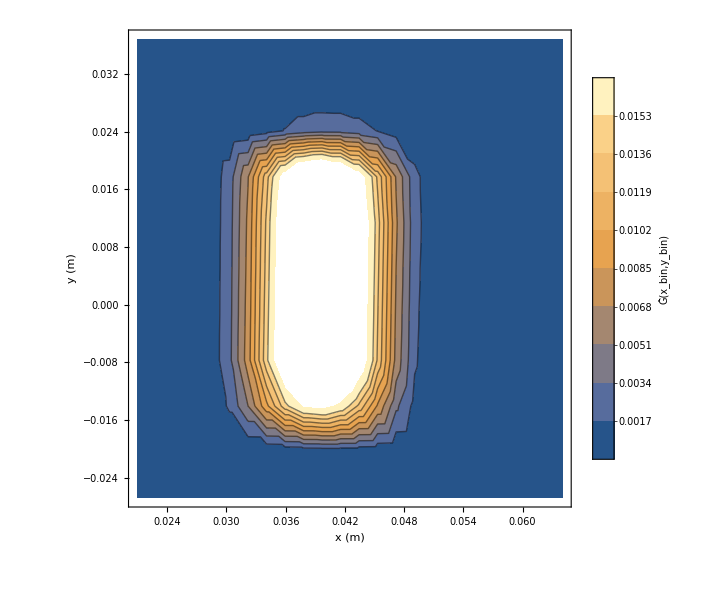

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAShift/a-1060/"];
```

```mathematica
dYAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYAShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYAShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1040[[All,2]]/Total[dYAShiftSpectruma1040[[All,2]]]}]];
dYAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1045[[All,2]]/Total[dYAShiftSpectruma1045[[All,2]]]}]];
dYAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}]];
dYAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1060[[All,2]]/Total[dYAShiftSpectruma1060[[All,2]]]}]];
dYAShiftSpectruma1030Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1030[[All,2]]/Total[dYAShiftSpectruma1030[[All,2]]]}]];
dYAShiftSpectruma1035Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1035[[All,2]]/Total[dYAShiftSpectruma1035[[All,2]]]}]];
dYAShiftSpectruma1020Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAShiftSpectruma1020[[All,2]]/Total[dYAShiftSpectruma1020[[All,2]]]}]];
```

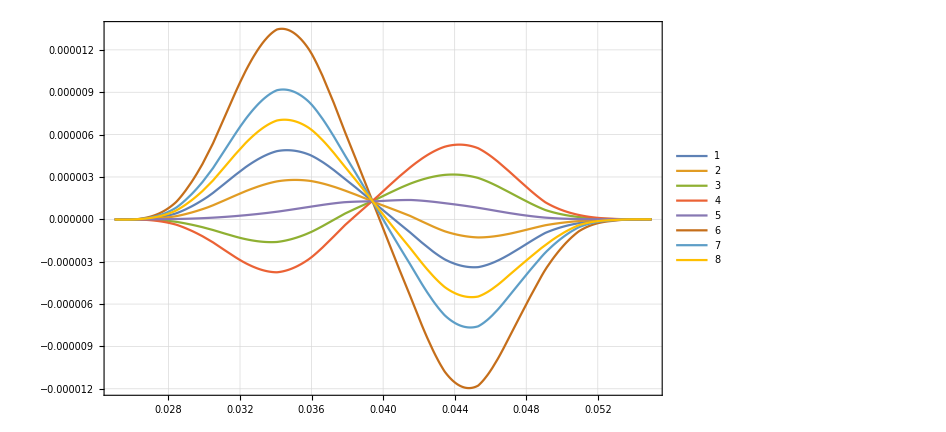

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYAShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma0Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1020Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1030Inter[x,0.],
RefSpectrumInter[x,0.]-dYAShiftSpectruma1035Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList]
```

```mathematica
YAShiftDataList={dYAShiftSpectruma1020[[All,2]]/Total[dYAShiftSpectruma1020[[All,2]]],dYAShiftSpectruma1030[[All,2]]/Total[dYAShiftSpectruma1030[[All,2]]],dYAShiftSpectruma1035[[All,2]]/Total[dYAShiftSpectruma1035[[All,2]]],dYAShiftSpectruma1040[[All,2]]/Total[dYAShiftSpectruma1040[[All,2]]],dYAShiftSpectruma1045[[All,2]]/Total[dYAShiftSpectruma1045[[All,2]]],dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]],dYAShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]],dYAShiftSpectruma1060[[All,2]]/Total[dYAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.102,-0.103,-0.1035,-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.102,-0.103,-0.1035,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

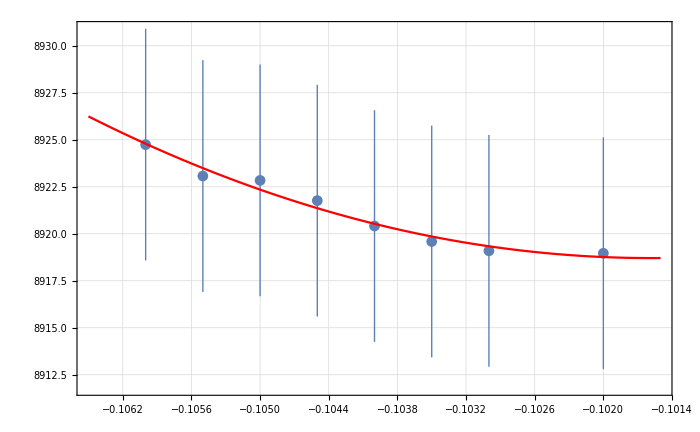
{{{8.91896×10^-6,8.91909×10^-6,8.91959×10^-6,8.92041×10^-6,8.92176×10^-6,8.92284×10^-6,8.92307×10^-6,8.92474×10^-6},{6.16488×10^-9,6.16384×10^-9,6.16347×10^-9,6.16323×10^-9,6.16324×10^-9,6.16321×10^-9,6.16349×10^-9,6.1637×10^-9}},a0 =  | -0.101581
FittedModel[8.91871×10^-6+0.000311423 (0.101581+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101581 | 0.0115715 | -8.77857 | 0.000318144
scale | 0.000311423 | 0.00142201 | 0.219001 | 0.835308
yoffset | 8.91871×10^-6 | 8.1098×10^-9 | 1099.74 | 1.17989×10^-14 | 
 | DF | SS | MS
Model | 3 | 1.676×10^7 | 5.58666×10^6
Error | 5 | 0.0200687 | 0.00401374
Uncorrected Total | 8 | 1.676×10^7 | 
Corrected Total | 7 | 0.83176 |  | ,-Graphics-}

```mathematica
YAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],YAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

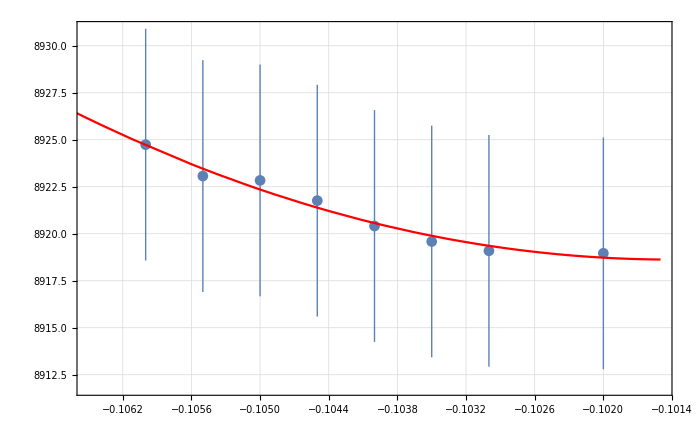
{{{8.91896×10^-6,8.91909×10^-6,8.91959×10^-6,8.92041×10^-6,8.92176×10^-6,8.92284×10^-6,8.92307×10^-6,8.92474×10^-6},{6.16488×10^-9,6.16384×10^-9,6.16347×10^-9,6.16323×10^-9,6.16324×10^-9,6.16321×10^-9,6.16349×10^-9,6.1637×10^-9}},a0 =  | -0.101406
FittedModel[8.91863×10^-6+0.000288483 (0.101406+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101406 | 0.0133294 | -7.60771 | 0.000623477
scale | 0.000288483 | 0.00142201 | 0.20287 | 0.847234
yoffset | 8.91863×10^-6 | 9.29081×10^-9 | 959.94 | 2.32851×10^-14 | 
 | DF | SS | MS
Model | 3 | 1.676×10^7 | 5.58666×10^6
Error | 5 | 0.0202751 | 0.00405502
Uncorrected Total | 8 | 1.676×10^7 | 
Corrected Total | 7 | 0.83176 |  | ,-Graphics-}

```mathematica
YAShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],YAShiftDataList,bList, 4]
```

```mathematica
((-0.10158085291422538+0.105)/-0.105)/(0.00025)
```

-130.253

```mathematica
((-0.10140601633241499+0.105)/-0.105)/(0.00025)
```

-136.914

```mathematica
-130.25322231522367*0.0001
```

-0.0130253

# dXAShift2D, k=1.62

### a=-0.105

#### a=-0.105(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1050/"];
```

```mathematica
dXAShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_179-264.txt}

```mathematica
dXAShiftSpectruma0=Flatten[Table[Import[dXAShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1050m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1050_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1050m15=Flatten[Table[Import[dXAShiftSubFileNamesa1050m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_5/"];
```

```mathematica
dXAShiftSubFileNamesa1050p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_5_179-264.txt}

```mathematica
dXAShiftSpectruma1050p5=Flatten[Table[Import[dXAShiftSubFileNamesa1050p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1050m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1050m5=Flatten[Table[Import[dXAShiftSubFileNamesa1050m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.105(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1050_15/"];
```

```mathematica
dXAShiftSubFileNamesa1050p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1050_15_179-264.txt}

```mathematica
dXAShiftSpectruma1050p15=Flatten[Table[Import[dXAShiftSubFileNamesa1050p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1050p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1050p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.104

#### a=-0.104(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1040/"];
```

```mathematica
dXAShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_179-264.txt}

```mathematica
dXAShiftSpectruma1040=Flatten[Table[Import[dXAShiftSubFileNamesa1040[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1040m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1040_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1040m15=Flatten[Table[Import[dXAShiftSubFileNamesa1040m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1040m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1040_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1040m5=Flatten[Table[Import[dXAShiftSubFileNamesa1040m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_5/"];
```

```mathematica
dXAShiftSubFileNamesa1040p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1040_5_179-264.txt}

```mathematica
dXAShiftSpectruma1040p5=Flatten[Table[Import[dXAShiftSubFileNamesa1040p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.104(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1040_15/"];
```

```mathematica
dXAShiftSubFileNamesa1040p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1040_15_179-264.txt}

```mathematica
dXAShiftSpectruma1040p15=Flatten[Table[Import[dXAShiftSubFileNamesa1040p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1040p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1045

#### a=-0.1045(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1045/"];
```

```mathematica
dXAShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_179-264.txt}

```mathematica
dXAShiftSpectruma1045=Flatten[Table[Import[dXAShiftSubFileNamesa1045[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1045m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1045m15=Flatten[Table[Import[dXAShiftSubFileNamesa1045m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_5/"];
```

```mathematica
dXAShiftSubFileNamesa1045p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1045_5_179-264.txt}

```mathematica
dXAShiftSpectruma1045p5=Flatten[Table[Import[dXAShiftSubFileNamesa1045p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1045m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1045_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1045m5=Flatten[Table[Import[dXAShiftSubFileNamesa1045m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1045(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1045_15/"];
```

```mathematica
dXAShiftSubFileNamesa1045p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1045_15_179-264.txt}

```mathematica
dXAShiftSpectruma1045p15=Flatten[Table[Import[dXAShiftSubFileNamesa1045p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1045p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1055

#### a=-0.1055(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1055/"];
```

```mathematica
dXAShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_179-264.txt}

```mathematica
dXAShiftSpectruma1055=Flatten[Table[Import[dXAShiftSubFileNamesa1055[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1055m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1055m15=Flatten[Table[Import[dXAShiftSubFileNamesa1055m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(-5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1055m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1055_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1055m5=Flatten[Table[Import[dXAShiftSubFileNamesa1055m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055m5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_5/"];
```

```mathematica
dXAShiftSubFileNamesa1055p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_5_179-264.txt}

```mathematica
dXAShiftSpectruma1055p5=Flatten[Table[Import[dXAShiftSubFileNamesa1055p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1055(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1055_15/"];
```

```mathematica
dXAShiftSubFileNamesa1055p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAShift_a-1055_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1055_15_179-264.txt}

```mathematica
dXAShiftSpectruma1055p15=Flatten[Table[Import[dXAShiftSubFileNamesa1055p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1055p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-0.1060

#### a=-0.1060(0)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift/a-1060/"];
```

```mathematica
dXAShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_179-264.txt}

```mathematica
dXAShiftSpectruma1060=Flatten[Table[Import[dXAShiftSubFileNamesa1060[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(-15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_-15/"];
```

```mathematica
dXAShiftSubFileNamesa1060m15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAShift_a-1060_-15_179-264.txt}

```mathematica
dXAShiftSpectruma1060m15=Flatten[Table[Import[dXAShiftSubFileNamesa1060m15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060m15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060m15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_5/"];
```

```mathematica
dXAShiftSubFileNamesa1060p5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_5_179-264.txt}

```mathematica
dXAShiftSpectruma1060p5=Flatten[Table[Import[dXAShiftSubFileNamesa1060p5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060p5]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060p5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(5)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_-5/"];
```

```mathematica
dXAShiftSubFileNamesa1060m5=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXAShift_a-1060_-5_179-264.txt}

```mathematica
dXAShiftSpectruma1060m5=Flatten[Table[Import[dXAShiftSubFileNamesa1060m5[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060m5]}],1];
```

```mathematica
dXAShiftSpectruma1050m5[[All,2]]//Length
```

264

```mathematica
dXAShiftSpectruma1060m5[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060m5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

#### a=-0.1060(15)

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAShift_2D/a-1060_15/"];
```

```mathematica
?FileSorter
```

```mathematica
dXAShiftSubFileNamesa1060p15=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAShift_a-1060_15_179-264.txt}

```mathematica
dXAShiftSpectruma1060p15=Flatten[Table[Import[dXAShiftSubFileNamesa1060p15[[i]],"Table"],{i,1,Length[dXAShiftSubFileNamesa1060p15]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060p15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]}]];
dXAShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]}]];
dXAShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]}]];
dXAShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0250006,0.23} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

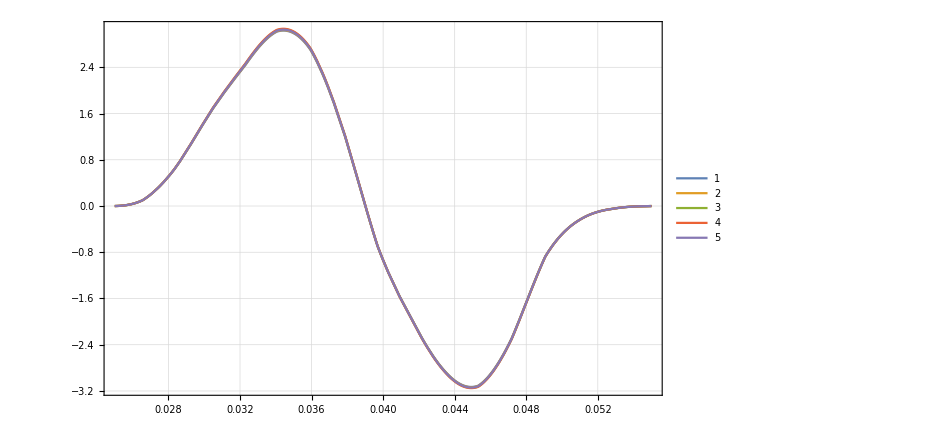

```mathematica
Plot[{
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1040Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1045Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1055Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma1060Inter[x,0.23],
RefSpectrumInter[x,0.23]-dXAShiftSpectruma0Inter[x,0.23]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[BDataList,XAShiftInvest]
```

```mathematica
XAShiftDataList={dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList2D={{-.104 ,-.1045,-.105,-.1055,-0.1060},{-0.00015,-0.00005,0.00005,0.00015,0.00025}}
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015,0.00025}}

```mathematica
bList2D2={{-.104 ,-.1045,-.105,-.1055,-0.1060},{-0.00015,-0.00005,0.00005,0.00015}}
```

{{-0.104,-0.1045,-0.105,-0.1055,-0.106},{-0.00015,-0.00005,0.00005,0.00015}}

```mathematica
XAShiftDataList2D2={{dXAShiftSpectruma1040m15[[All,2]]/Total[dXAShiftSpectruma1040m15[[All,2]]],dXAShiftSpectruma1040m5[[All,2]]/Total[dXAShiftSpectruma1040m5[[All,2]]],dXAShiftSpectruma1040p5[[All,2]]/Total[dXAShiftSpectruma1040p5[[All,2]]],dXAShiftSpectruma1040p15[[All,2]]/Total[dXAShiftSpectruma1040p15[[All,2]]]},{dXAShiftSpectruma1045m15[[All,2]]/Total[dXAShiftSpectruma1045m15[[All,2]]],dXAShiftSpectruma1045m5[[All,2]]/Total[dXAShiftSpectruma1045m5[[All,2]]],dXAShiftSpectruma1045p5[[All,2]]/Total[dXAShiftSpectruma1045p5[[All,2]]],dXAShiftSpectruma1045p15[[All,2]]/Total[dXAShiftSpectruma1045p15[[All,2]]]},{dXAShiftSpectruma1050m15[[All,2]]/Total[dXAShiftSpectruma1050m15[[All,2]]],dXAShiftSpectruma1050m5[[All,2]]/Total[dXAShiftSpectruma1050m5[[All,2]]],dXAShiftSpectruma1050p5[[All,2]]/Total[dXAShiftSpectruma1050p5[[All,2]]],dXAShiftSpectruma1050p15[[All,2]]/Total[dXAShiftSpectruma1050p15[[All,2]]]},{dXAShiftSpectruma1055m15[[All,2]]/Total[dXAShiftSpectruma1055m15[[All,2]]],dXAShiftSpectruma1055m5[[All,2]]/Total[dXAShiftSpectruma1055m5[[All,2]]],dXAShiftSpectruma1055p5[[All,2]]/Total[dXAShiftSpectruma1055p5[[All,2]]],dXAShiftSpectruma1055p15[[All,2]]/Total[dXAShiftSpectruma1055p15[[All,2]]]},{dXAShiftSpectruma1060m15[[All,2]]/Total[dXAShiftSpectruma1060m15[[All,2]]],dXAShiftSpectruma1060m5[[All,2]]/Total[dXAShiftSpectruma1060m5[[All,2]]],dXAShiftSpectruma1060p5[[All,2]]/Total[dXAShiftSpectruma1060p5[[All,2]]],dXAShiftSpectruma1060p15[[All,2]]/Total[dXAShiftSpectruma1060p15[[All,2]]]}
};
```

```mathematica
XAShiftDataList2D={{dXAShiftSpectruma1040m15[[All,2]]/Total[dXAShiftSpectruma1040m15[[All,2]]],dXAShiftSpectruma1040m5[[All,2]]/Total[dXAShiftSpectruma1040m5[[All,2]]],dXAShiftSpectruma1040p5[[All,2]]/Total[dXAShiftSpectruma1040p5[[All,2]]],dXAShiftSpectruma1040p15[[All,2]]/Total[dXAShiftSpectruma1040p15[[All,2]]],dXAShiftSpectruma1040[[All,2]]/Total[dXAShiftSpectruma1040[[All,2]]]},{dXAShiftSpectruma1045m15[[All,2]]/Total[dXAShiftSpectruma1045m15[[All,2]]],dXAShiftSpectruma1045m5[[All,2]]/Total[dXAShiftSpectruma1045m5[[All,2]]],dXAShiftSpectruma1045p5[[All,2]]/Total[dXAShiftSpectruma1045p5[[All,2]]],dXAShiftSpectruma1045p15[[All,2]]/Total[dXAShiftSpectruma1045p15[[All,2]]],dXAShiftSpectruma1045[[All,2]]/Total[dXAShiftSpectruma1045[[All,2]]]},{dXAShiftSpectruma1050m15[[All,2]]/Total[dXAShiftSpectruma1050m15[[All,2]]],dXAShiftSpectruma1050m5[[All,2]]/Total[dXAShiftSpectruma1050m5[[All,2]]],dXAShiftSpectruma1050p5[[All,2]]/Total[dXAShiftSpectruma1050p5[[All,2]]],dXAShiftSpectruma1050p15[[All,2]]/Total[dXAShiftSpectruma1050p15[[All,2]]],dXAShiftSpectruma0[[All,2]]/Total[dXAShiftSpectruma0[[All,2]]]},{dXAShiftSpectruma1055m15[[All,2]]/Total[dXAShiftSpectruma1055m15[[All,2]]],dXAShiftSpectruma1055m5[[All,2]]/Total[dXAShiftSpectruma1055m5[[All,2]]],dXAShiftSpectruma1055p5[[All,2]]/Total[dXAShiftSpectruma1055p5[[All,2]]],dXAShiftSpectruma1055p15[[All,2]]/Total[dXAShiftSpectruma1055p15[[All,2]]],dXAShiftSpectruma1055[[All,2]]/Total[dXAShiftSpectruma1055[[All,2]]]},{dXAShiftSpectruma1060m15[[All,2]]/Total[dXAShiftSpectruma1060m15[[All,2]]],dXAShiftSpectruma1060m5[[All,2]]/Total[dXAShiftSpectruma1060m5[[All,2]]],dXAShiftSpectruma1060p5[[All,2]]/Total[dXAShiftSpectruma1060p5[[All,2]]],dXAShiftSpectruma1060p15[[All,2]]/Total[dXAShiftSpectruma1060p15[[All,2]]],dXAShiftSpectruma1060[[All,2]]/Total[dXAShiftSpectruma1060[[All,2]]]}
};
```

```mathematica
RefNorm=RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]];
```

```mathematica
Length[RefNorm]
```

264

```mathematica
Dimensions[XAShiftDataList2D]
```

{5,5,264}

```mathematica
Length[XAShiftDataList2D[[1,1]]]
```

264

```mathematica
Length[bList2D[[2]]]
```

5

```mathematica
Table[XAShiftDataList2D⟦b,par⟧//Length,{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}]
```

{{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264},{264,264,264,264,264}}

```mathematica
Chi2List2D2=Table[Total[(RefNorm-XAShiftDataList2D2⟦b,par⟧)^2],{b,Length[bList2D2[[1]]]},{par,Length[bList2D2[[2]]]}];
```

```mathematica
Chi2List2D=Table[Total[(RefNorm-XAShiftDataList2D⟦b,par⟧)^2],{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}];
```

```mathematica
Chi2List2D
```

{{0.0000126211,1.43994×10^-6,1.33175×10^-6,0.0000122879,0.0000343155},{0.0000125412,1.41195×10^-6,1.3578×10^-6,0.0000123668,0.000034447},{0.0000124614,1.38544×10^-6,1.38414×10^-6,0.0000124466,0.0000345783},{0.000012382,1.3591×10^-6,1.41072×10^-6,0.000012526,0.0000347027},{0.0000123005,1.33293×10^-6,1.43759×10^-6,0.0000126057,0.0000348354}}

```mathematica
plotChi2List2D=Table[{bList2D[[1,b]],bList2D[[2,par]],Total[(RefNorm-XAShiftDataList2D⟦b,par⟧)^2]},{b,Length[bList2D[[1]]]},{par,Length[bList2D[[2]]]}];
```

```mathematica
plotChi2List2D2=Table[{bList2D2[[1,b]],bList2D2[[2,par]],Total[(RefNorm-XAShiftDataList2D2⟦b,par⟧)^2]},{b,Length[bList2D2[[1]]]},{par,Length[bList2D2[[2]]]}];
```

```mathematica
dChi2List=Table[10^-4 √Total[(RefNorm-XAShiftDataList2D⟦b,para⟧)^2 (RefNorm^2+XAShiftDataList2D⟦b,para⟧^2)],{b,Length[bList2D[[1]]]},{para,Length[bList2D[[2]]]}];
```

```mathematica
dChi2List2=Table[10^-4 √Total[(RefNorm-XAShiftDataList2D2⟦b,para⟧)^2 (RefNorm^2+XAShiftDataList2D2⟦b,para⟧^2)],{b,Length[bList2D2[[1]]]},{para,Length[bList2D2[[2]]]}];
```

```mathematica
fitfunc[a_,a0_,par_,par0_,ascale_,pscale_,offset_]:=offset+(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
fitfunc2[x_,x0_,y_,y0_,f_,g_,k_]:=k+f*(x-x0)^2+g*(y-y0)^2
```

```mathematica
0<-0.105<0
```

False

```mathematica
fit2=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.107<a00<-0.101,-Max[bList2D2[[2]]]<par0<Max[bList2D2[[2]]],-100<ascale<100,-1<pscale<1,0.<offset≤Min[Chi2List2D2]},{{a00,-0.105},{offset,Min[Chi2List2D2]},{ascale,5},{pscale,5/10^4},{par0,Min[bList2D2[[2]]]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.+0.0001 (0.106174+a)^2+553.548 (-1.87294×10^-8+par)^2]

```mathematica
fit=NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[bList2D[[2]]]<par0<Max[bList2D[[2]]],-2<ascale<1,-1<pscale<1,0.<offset≤Min[Chi2List2D]},{{a00,-0.105},{par0,Min[bList2D[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.+0.253737 (0.105042+a)^2+544.554 (4.10497×10^-7+par)^2]

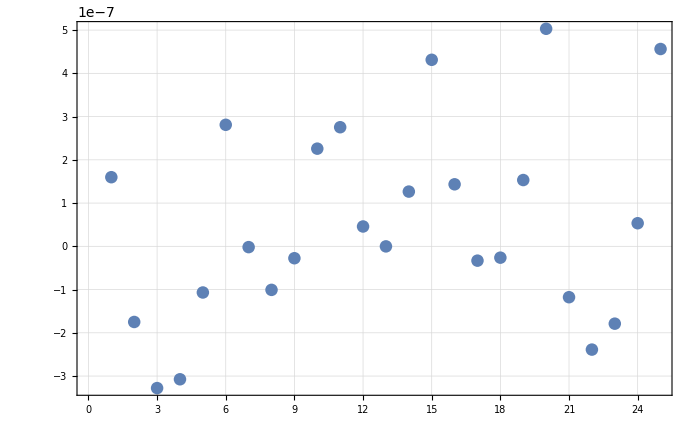

```mathematica
ListPlot[fit["FitResiduals"]]
```

```mathematica
(-0.10499501973815213+0.105)/-0.105
```

-0.0000474311

```mathematica
-0.18972426087102806*0.0001
```

-0.0000189724

```mathematica
(-0.10504249683354637+0.105)/-0.105
```

0.000404732

```mathematica
0.00040473174806070276/0.00025
```

1.61893

```mathematica
0.00040473174806070276/0.00025*0.0001
```

0.000161893

```mathematica
a00/.fit["BestFitParameters"]
```

-0.105042

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105042 | 2.28751×10^-6 | -45920. | 1.03817×10^-81
par0 | -4.10497×10^-7 | 1.07627×10^-8 | -38.1409 | 3.7314×10^-20
ascale | -1.98522 | 0.00759741 | -261.302 | 8.17032×10^-37
pscale | 0.0428528 | 3.52509×10^-6 | 12156.5 | 3.63175×10^-70
offset | 0. | 1.35196×10^-9 | 0. | 1.

```mathematica
Show[ListPlot3D[Flatten[plotChi2List2D,1],PlotStyle->Blue],Plot3D[fit[a,par],{a,-0.104,-.106},{par,-0.00015,0.00025},PlotStyle->Red]]
```

-Graphics3D-

```mathematica
XAShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],XAShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.0000343155,0.000034447,0.0000345783,0.0000347027,0.0000348354},{1.36128×10^-8,1.3639×10^-8,1.36652×10^-8,1.36875×10^-8,1.3714×10^-8}},a0 =  | -0.1035
FittedModel[0.0000343155+0.0902549 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000247235 | -418.63 | 5.70605×10^-6
scale | 0.0902549 | 0.0146073 | 6.17876 | 0.0252075
yoffset | 0.0000343155 | 2.92413×10^-8 | 1173.53 | 7.26125×10^-7 | 
 | DF | SS | MS
Model | 3 | 3.20164×10^7 | 1.06721×10^7
Error | 2 | 45.011 | 22.5055
Uncorrected Total | 5 | 3.20165×10^7 | 
Corrected Total | 4 | 899.025 |  | ,-Graphics-}

```mathematica
z=
```

```mathematica
((XAShiftInvest2[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-136.048

```mathematica
-136.04810567554844*0.00025
```

-0.034012

```mathematica
((XAShiftInvest[[2,1,1,2]]+0.105)/-0.105)/(0.00025)
```

-57.1429

```mathematica
0.0003+0.0003
```

0.0006

```mathematica
0.0006/6
```

0.0001

```mathematica
Table[i,{i,-0.0003,0.0003,0.0006/4}]
```

{-0.0003,-0.00015,0.,0.00015,0.0003}

# dYRxBShift, k=0.000029

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1050/"];
```

```mathematica
dYrxbShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1050_179-264.txt}

```mathematica
dYrxbShiftSpectruma0=Flatten[Table[Import[dYrxbShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYrxbShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1040/"];
```

```mathematica
dYrxbShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1040_179-264.txt}

```mathematica
dYrxbShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1045/"];
```

```mathematica
dYrxbShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1045_179-264.txt}

```mathematica
dYrxbShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1055/"];
```

```mathematica
dYrxbShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYrxbshift_a-1055_179-264.txt}

```mathematica
dYrxbShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

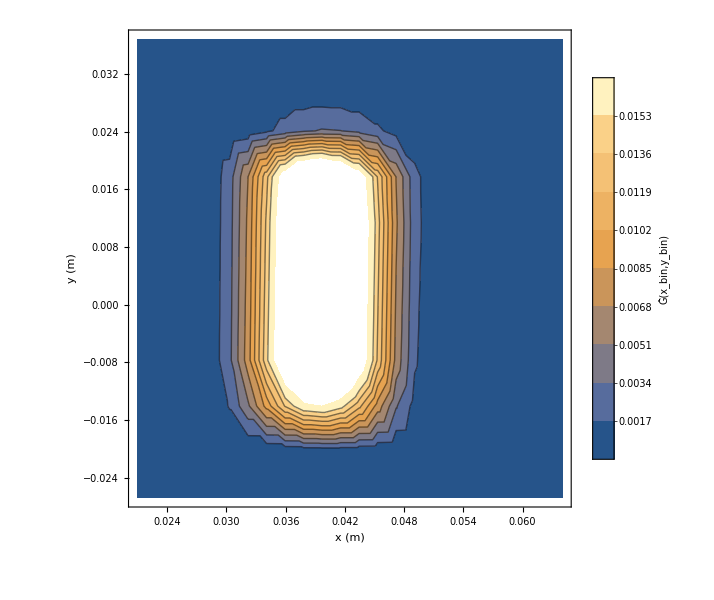

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYrxbshift/a-1060/"];
```

```mathematica
dYrxbShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYrxbshift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYrxbShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYrxbShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYrxbShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma0[[All,2]]/Total[dYrxbShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYrxbShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1040[[All,2]]/Total[dYrxbShiftSpectruma1040[[All,2]]]}]];
dYrxbShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1045[[All,2]]/Total[dYrxbShiftSpectruma1045[[All,2]]]}]];
dYrxbShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYrxbShiftSpectruma1055[[All,2]]]}]];
dYrxbShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYrxbShiftSpectruma1060[[All,2]]/Total[dYrxbShiftSpectruma1060[[All,2]]]}]];
```

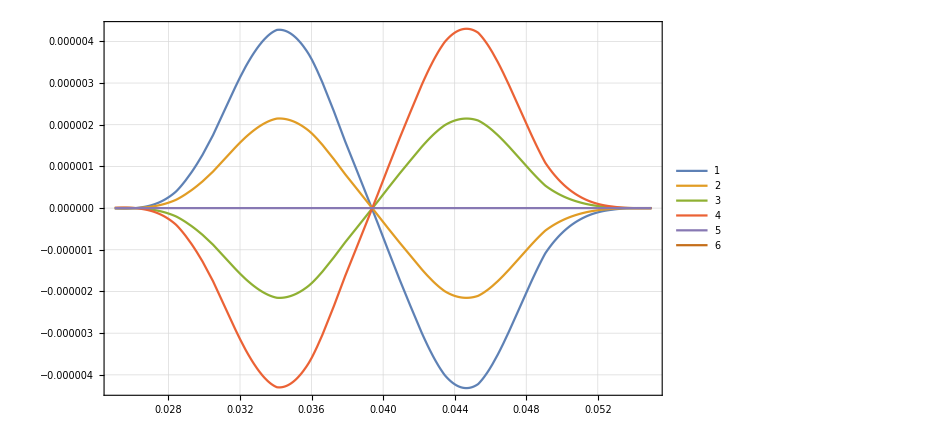

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYrxbShiftSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYrxbShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYrxbShiftDataList={dYrxbShiftSpectruma1040[[All,2]]/Total[dYrxbShiftSpectruma1040[[All,2]]],dYrxbShiftSpectruma1045[[All,2]]/Total[dYrxbShiftSpectruma1045[[All,2]]],dYrxbShiftSpectruma0[[All,2]]/Total[dYrxbShiftSpectruma0[[All,2]]],dYrxbShiftSpectruma1055[[All,2]]/Total[dYrxbShiftSpectruma1055[[All,2]]],dYrxbShiftSpectruma1060[[All,2]]/Total[dYrxbShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
RefNorm=Total[RefSpectrum[[All,2]]];
```

```mathematica
RefNormed=RefSpectrum[[All,2]]/RefNorm;
```

```mathematica
Sigma=(If[#1==0,10000,10^-4 #1]&)/@RefNormed;
```

```mathematica
TransferDataListNormed=(#1/Total[#1]&)/@dYrxbShiftDataList;
```

```mathematica
Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[bList]}];dChi2List=Table[10^-4 √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[bList]}];errorplotdata=Transpose[{bList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.106<b0<-0.104&&-100<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[5.68265×10^-34+0.000511307 (0.105+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 9.90204×10^-37 | -1.06039×10^35 | 0.
scale | 0.000511307 | 8.34241×10^-45 | 6.12901×10^40 | 0.
yoffset | 5.68265×10^-34 | 1.11487×10^-22 | 5.09714×10^-12 | 1.

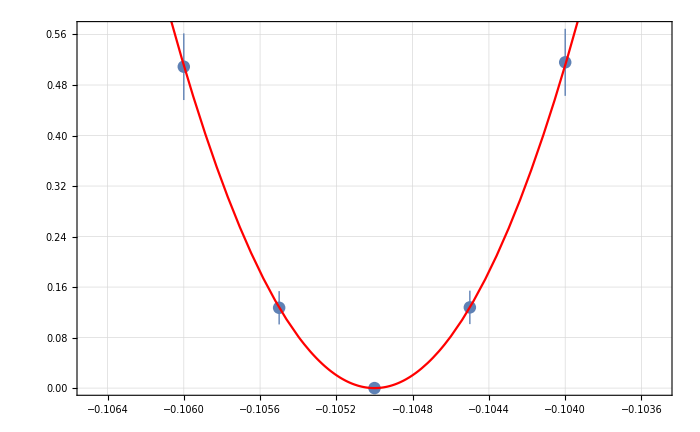

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{-0.1065,-0.1035},Automatic}],Plot[10^9 fitresult[b],{b,-0.1065,-0.1035},PlotStyle->Red]]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

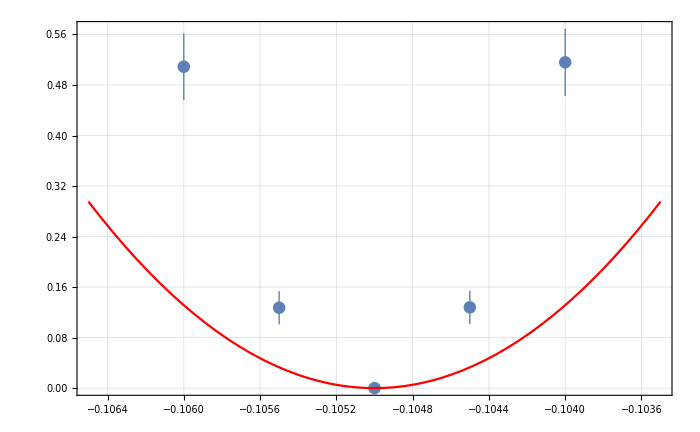
{{{5.1594×10^-10,1.27824×10^-10,1.0522×10^-33,1.27214×10^-10,5.08995×10^-10},{5.30987×10^-11,2.64719×10^-11,1.11487×10^-22,2.63741×10^-11,5.27829×10^-11}},a0 =  | -0.105
FittedModel[1.37355×10^-34+0.000131292 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 4.08459×10^-36 | -2.57064×10^34 | 0.
scale | 0.000131292 | 2.18009×10^-42 | 6.02231×10^37 | 0.
yoffset | 1.37355×10^-34 | 1.11487×10^-22 | 1.23203×10^-12 | 1. | 
 | DF | SS | MS
Model | 3 | 104.616 | 34.8719
Error | 2 | 129.37 | 64.6848
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
dYrxbShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYrxbShiftDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

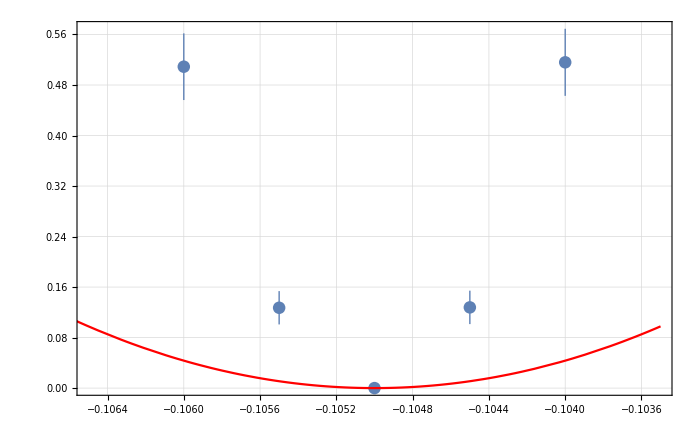
{{{5.1594×10^-10,1.27824×10^-10,1.0522×10^-33,1.27214×10^-10,5.08995×10^-10},{5.30987×10^-11,2.64719×10^-11,1.11487×10^-22,2.63741×10^-11,5.27829×10^-11}},a0 =  | -0.105
FittedModel[1.0522×10^-33+0.000043454 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 7.42653×10^-36 | -1.41385×10^34 | 0.
scale | 0.000043454 | 6.53648×10^-41 | 6.64791×10^35 | 0.
yoffset | 1.0522×10^-33 | 1.11487×10^-22 | 9.4379×10^-12 | 1. | 
 | DF | SS | MS
Model | 3 | 37.98 | 12.66
Error | 2 | 196.005 | 98.0027
Uncorrected Total | 5 | 233.985 | 
Corrected Total | 4 | 233.985 |  | ,-Graphics-}

```mathematica
dYrxbShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYrxbShiftDataList,bList, 4]
```

```mathematica
0.00025
```

```mathematica
((-0.10500000076570207+0.105)/-0.105)/(0.00025)
```

0.0000291696

```mathematica
((-0.10500000000865034+0.105)/-0.105)/(0.00025)
```

3.29537×10^-7

# dNk2x, k=11.22

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1050/"];
```

```mathematica
dNk2xSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1050_179-264.txt}

```mathematica
dNk2xSpectruma0=Flatten[Table[Import[dNk2xSubFileNamesa0[[i]],"Table"],{i,1,Length[dNk2xSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1040/"];
```

```mathematica
dNk2xSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1040_179-264.txt}

```mathematica
dNk2xSpectruma1040=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1045/"];
```

```mathematica
dNk2xSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1045_179-264.txt}

```mathematica
dNk2xSpectruma1045=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1055/"];
```

```mathematica
dNk2xSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dNk2x_a-1055_179-264.txt}

```mathematica
dNk2xSpectruma1055=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

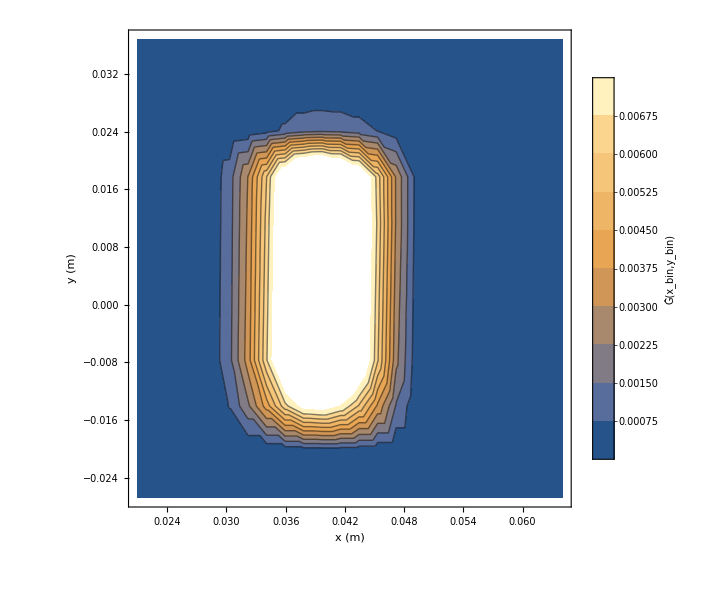

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dNk2x/a-1060/"];
```

```mathematica
dNk2xSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dNk2x_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dNk2xSpectruma1060=Flatten[Import[#,"Table"]&/@dNk2xSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dNk2xSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma0[[All,2]]/Total[dNk2xSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dNk2xSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1040[[All,2]]/Total[dNk2xSpectruma1040[[All,2]]]}]];
dNk2xSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1045[[All,2]]/Total[dNk2xSpectruma1045[[All,2]]]}]];
dNk2xSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1055[[All,2]]/Total[dNk2xSpectruma1055[[All,2]]]}]];
dNk2xSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dNk2xSpectruma1060[[All,2]]/Total[dNk2xSpectruma1060[[All,2]]]}]];
```

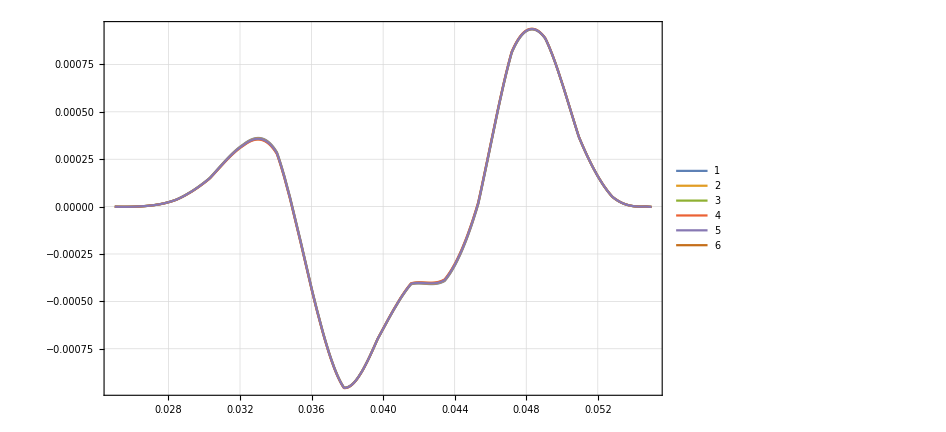

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dNk2xSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dNk2xSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dNk2xDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dNk2xDataList={dNk2xSpectruma1040[[All,2]]/Total[dNk2xSpectruma1040[[All,2]]],dNk2xSpectruma1045[[All,2]]/Total[dNk2xSpectruma1045[[All,2]]],dNk2xSpectruma0[[All,2]]/Total[dNk2xSpectruma0[[All,2]]],dNk2xSpectruma1055[[All,2]]/Total[dNk2xSpectruma1055[[All,2]]],dNk2xSpectruma1060[[All,2]]/Total[dNk2xSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

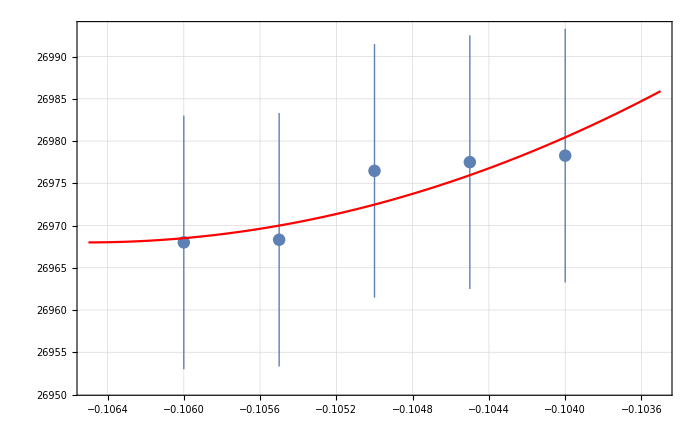
{{{0.0000269783,0.0000269775,0.0000269765,0.0000269683,0.000026968},{1.50142×10^-8,1.50119×10^-8,1.50109×10^-8,1.50085×10^-8,1.50077×10^-8}},a0 =  | -0.1065
FittedModel[0.000026968+0.00198904 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.0123342 | -8.6345 | 0.013149
scale | 0.00198904 | 0.0160472 | 0.123949 | 0.91269
yoffset | 0.000026968 | 3.21907×10^-8 | 837.759 | 1.42482×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.61455×10^7 | 5.38185×10^6
Error | 2 | 0.115597 | 0.0577983
Uncorrected Total | 5 | 1.61455×10^7 | 
Corrected Total | 4 | 0.463708 |  | ,-Graphics-}

```mathematica
dNk2xInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dNk2xDataList,bList, 4]
```

```mathematica
(-0.1065+0.105)/-0.105/0.005
```

2.85714

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

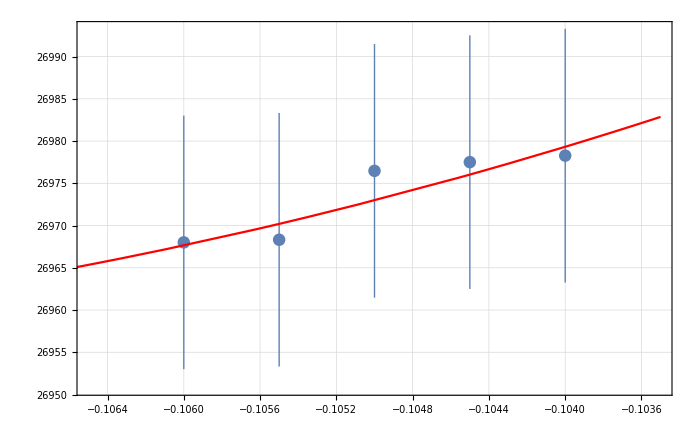
{{{0.0000269783,0.0000269775,0.0000269765,0.0000269683,0.000026968},{1.50142×10^-8,1.50119×10^-8,1.50109×10^-8,1.50085×10^-8,1.50077×10^-8}},a0 =  | -0.110893
FittedModel[0.0000269558+0.000495243 (0.110893+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.110893 | 0.191195 | -0.58 | 0.62055
scale | 0.000495243 | 0.0160472 | 0.0308616 | 0.978183
yoffset | 0.0000269558 | 5.5217×10^-7 | 48.8179 | 0.000419343 | 
 | DF | SS | MS
Model | 3 | 1.61455×10^7 | 5.38185×10^6
Error | 2 | 0.0845484 | 0.0422742
Uncorrected Total | 5 | 1.61455×10^7 | 
Corrected Total | 4 | 0.463708 |  | ,-Graphics-}

```mathematica
dNk2xInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dNk2xDataList,bList, 4]
```

```mathematica
0.00025
```

```mathematica
((-0.11089324097917469+0.105)/-0.105)/(0.005)
```

11.2252

```mathematica
0.2/1000
```

0.0002

# dXAoff, k=177.55/71.43

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1050/"];
```

```mathematica
dXAoffSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1050_179-264.txt}

```mathematica
dXAoffSpectruma0=Flatten[Table[Import[dXAoffSubFileNamesa0[[i]],"Table"],{i,1,Length[dXAoffSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1040/"];
```

```mathematica
dXAoffSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1040_179-264.txt}

```mathematica
dXAoffSpectruma1040=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1045/"];
```

```mathematica
dXAoffSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1045_179-264.txt}

```mathematica
dXAoffSpectruma1045=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1055/"];
```

```mathematica
dXAoffSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1055_179-264.txt}

```mathematica
dXAoffSpectruma1055=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

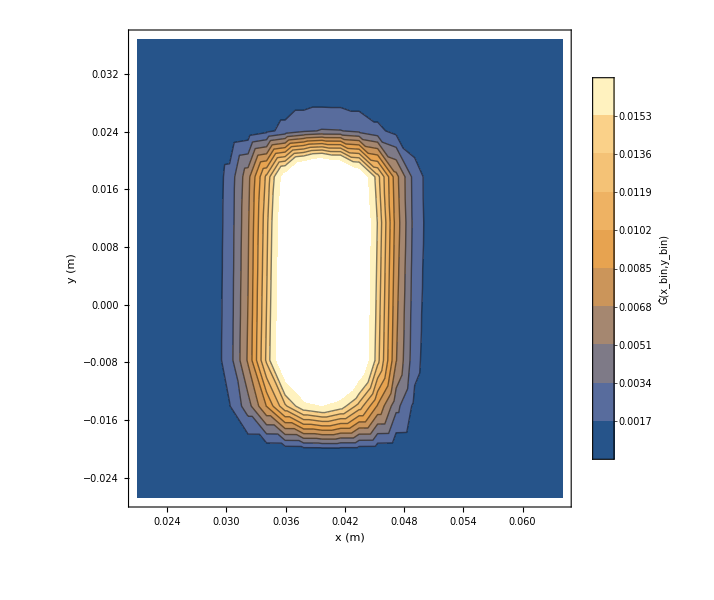

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1060/"];
```

```mathematica
dXAoffSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXAoff_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXAoffSpectruma1060=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXAoffSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma0[[All,2]]/Total[dXAoffSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXAoffSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1040[[All,2]]/Total[dXAoffSpectruma1040[[All,2]]]}]];
dXAoffSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1045[[All,2]]/Total[dXAoffSpectruma1045[[All,2]]]}]];
dXAoffSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]]}]];
dXAoffSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1060[[All,2]]/Total[dXAoffSpectruma1060[[All,2]]]}]];
```

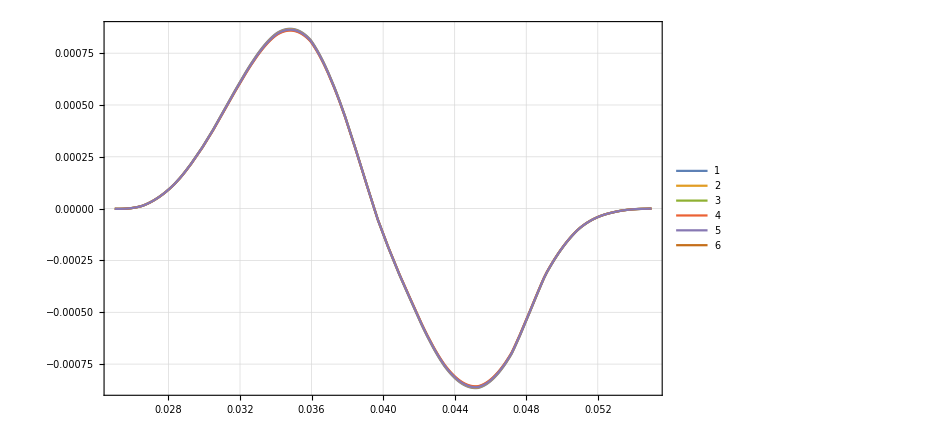

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXAoffSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXAoffSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

### a=-1065

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1065/"];
```

```mathematica
dXAoffSubFileNamesa1065=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_1-49.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_50-98.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_99-106.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_107-122.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_123-138.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_139-154.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_155-178.txt,TransferResult_08-09-20_SC_opt_C_dXAoff_a-1065_179-264.txt}

```mathematica
dXAoffSpectruma1065=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1065,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1065[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1070

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXAoff/a-1070/"];
```

```mathematica
dXAoffSubFileNamesa1070=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXAoff_a-1070_179-264.txt}

```mathematica
dXAoffSpectruma1070=Flatten[Import[#,"Table"]&/@dXAoffSubFileNamesa1070,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXAoffSpectruma1070[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dXAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dXAoffDataList={dXAoffSpectruma1040[[All,2]]/Total[dXAoffSpectruma1040[[All,2]]],dXAoffSpectruma1045[[All,2]]/Total[dXAoffSpectruma1045[[All,2]]],dXAoffSpectruma0[[All,2]]/Total[dXAoffSpectruma0[[All,2]]],dXAoffSpectruma1055[[All,2]]/Total[dXAoffSpectruma1055[[All,2]]],dXAoffSpectruma1060[[All,2]]/Total[dXAoffSpectruma1060[[All,2]]],dXAoffSpectruma1065[[All,2]]/Total[dXAoffSpectruma1065[[All,2]]],dXAoffSpectruma1070[[All,2]]/Total[dXAoffSpectruma1070[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060,-0.1065,-0.1070}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106,-0.1065,-0.107}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

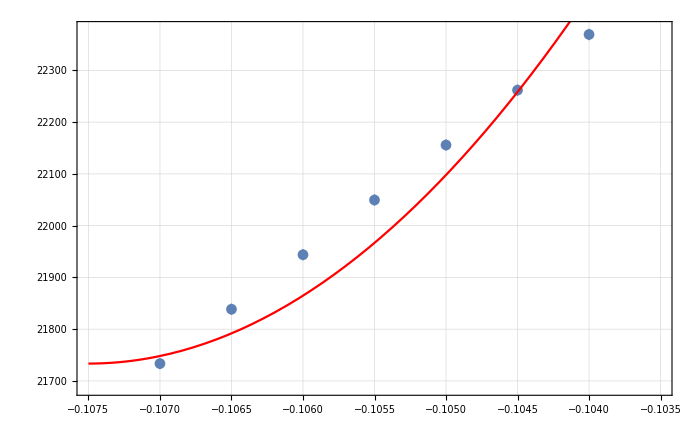
{{{0.0000223693,0.0000222618,0.0000221558,0.0000220495,0.0000219438,0.0000218385,0.0000217335},{1.09942×10^-8,1.09676×10^-8,1.09413×10^-8,1.09149×10^-8,1.08884×10^-8,1.08621×10^-8,1.08358×10^-8}},a0 =  | -0.1075
FittedModel[0.0000217335+0.0582959 (0.1075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1075 | 0.000166925 | -644. | 3.48819×10^-11
scale | 0.0582959 | 0.00476361 | 12.2378 | 0.000256009
yoffset | 0.0000217335 | 1.69321×10^-8 | 1283.57 | 2.2104×10^-12 | 
 | DF | SS | MS
Model | 3 | 2.85677×10^7 | 9.52256×10^6
Error | 4 | 209.514 | 52.3785
Uncorrected Total | 7 | 2.85679×10^7 | 
Corrected Total | 6 | 2636.97 |  | ,-Graphics-}

```mathematica
dXAoffInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dXAoffDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

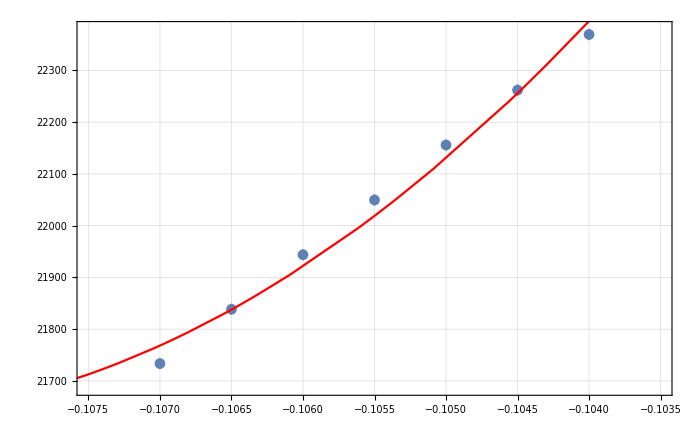
{{{0.0000223693,0.0000222618,0.0000221558,0.0000220495,0.0000219438,0.0000218385,0.0000217335},{1.09942×10^-8,1.09676×10^-8,1.09413×10^-8,1.09149×10^-8,1.08884×10^-8,1.08621×10^-8,1.08358×10^-8}},a0 =  | -0.109236
FittedModel[0.0000216285+0.0279742 (0.109236+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.109236 | 0.000639775 | -170.741 | 7.05833×10^-9
scale | 0.0279742 | 0.00476361 | 5.87247 | 0.00420002
yoffset | 0.0000216285 | 6.36072×10^-8 | 340.032 | 4.48793×10^-10 | 
 | DF | SS | MS
Model | 3 | 2.85679×10^7 | 9.52262×10^6
Error | 4 | 33.7287 | 8.43217
Uncorrected Total | 7 | 2.85679×10^7 | 
Corrected Total | 6 | 2636.97 |  | ,-Graphics-}

```mathematica
dXAoffInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dXAoffDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10872865859233186+0.105)/-0.105)/(0.0002)
```

177.555

```mathematica
((-0.10923565206790305+0.105)/-0.105)/(0.0002)
```

201.698

# dYAoff, k=37

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1050/"];
```

```mathematica
dYAoffSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYAoff_a-1050_179-264.txt}

```mathematica
dYAoffSpectruma0=Flatten[Table[Import[dYAoffSubFileNamesa0[[i]],"Table"],{i,1,Length[dYAoffSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1040/"];
```

```mathematica
dYAoffSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1040_179-264.txt}

```mathematica
dYAoffSpectruma1040=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1045/"];
```

```mathematica
dYAoffSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1045_179-264.txt}

```mathematica
dYAoffSpectruma1045=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1055/"];
```

```mathematica
dYAoffSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYAoff_a-1055_179-264.txt}

```mathematica
dYAoffSpectruma1055=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

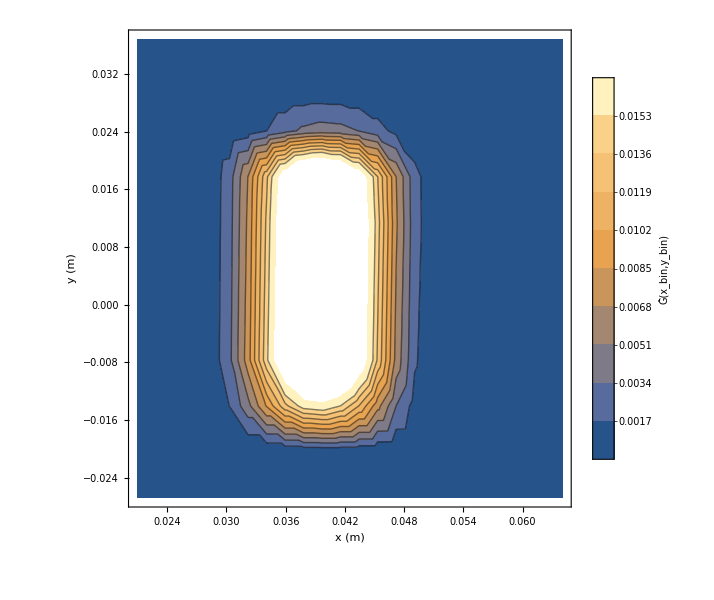

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]/Total[dYAShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYAoff/a-1060/"];
```

```mathematica
dYAoffSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYAoff_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYAoffSpectruma1060=Flatten[Import[#,"Table"]&/@dYAoffSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYAShiftSpectruma0[[All,2]]/Total[dYAShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYAoffSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma0[[All,2]]/Total[dYAoffSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYAoffSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1040[[All,2]]/Total[dYAoffSpectruma1040[[All,2]]]}]];
dYAoffSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1045[[All,2]]/Total[dYAoffSpectruma1045[[All,2]]]}]];
dYAoffSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1055[[All,2]]/Total[dYAoffSpectruma1055[[All,2]]]}]];
dYAoffSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYAoffSpectruma1060[[All,2]]/Total[dYAoffSpectruma1060[[All,2]]]}]];
```

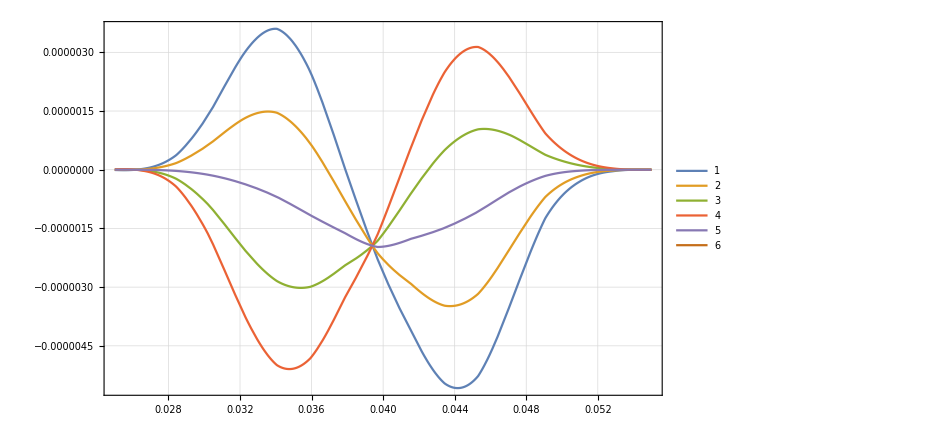

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYAoffSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYAoffSpectruma0Inter[x,0.],
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYAoffDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYAoffDataList={dYAoffSpectruma1040[[All,2]]/Total[dYAoffSpectruma1040[[All,2]]],dYAoffSpectruma1045[[All,2]]/Total[dYAoffSpectruma1045[[All,2]]],dYAoffSpectruma0[[All,2]]/Total[dYAoffSpectruma0[[All,2]]],dYAoffSpectruma1055[[All,2]]/Total[dYAoffSpectruma1055[[All,2]]],dYAoffSpectruma1060[[All,2]]/Total[dYAoffSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

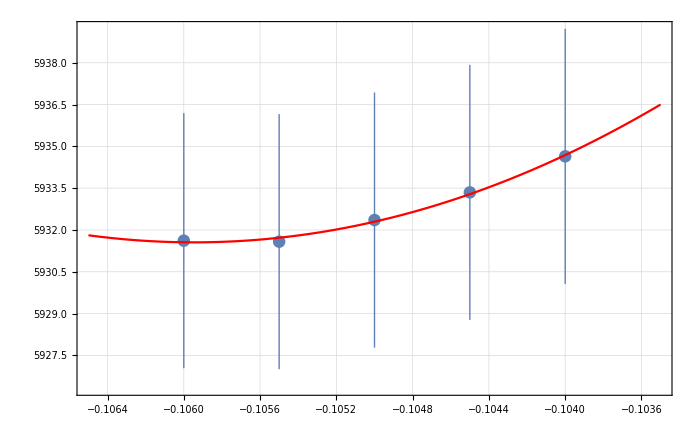
{{{5.93464×10^-6,5.93335×10^-6,5.93236×10^-6,5.93158×10^-6,5.93162×10^-6},{4.5762×10^-9,4.5759×10^-9,4.57577×10^-9,4.57577×10^-9,4.57606×10^-9}},a0 =  | -0.105946
FittedModel[5.93156×10^-6+0.000826198 (0.105946+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105946 | 0.00587116 | -18.0452 | 0.00305689
scale | 0.000826198 | 0.00489193 | 0.16889 | 0.881419
yoffset | 5.93156×10^-6 | 3.92918×10^-9 | 1509.62 | 4.38801×10^-7 | 
 | DF | SS | MS
Model | 3 | 8.40457×10^6 | 2.80152×10^6
Error | 2 | 0.00154951 | 0.000774754
Uncorrected Total | 5 | 8.40457×10^6 | 
Corrected Total | 4 | 0.321784 |  | ,-Graphics-}

```mathematica
dYAoffInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYAoffDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

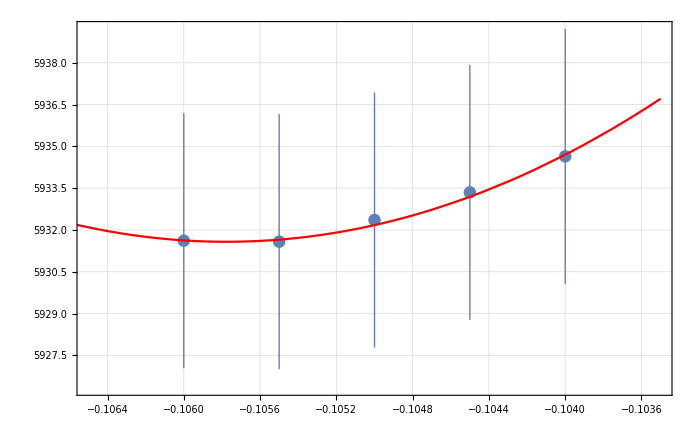
{{{5.93464×10^-6,5.93335×10^-6,5.93236×10^-6,5.93158×10^-6,5.93162×10^-6},{4.5762×10^-9,4.5759×10^-9,4.57577×10^-9,4.57577×10^-9,4.57606×10^-9}},a0 =  | -0.105777
FittedModel[5.93158×10^-6+0.000989562 (0.105777+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105777 | 0.0041106 | -25.7328 | 0.00150676
scale | 0.000989562 | 0.00489193 | 0.202284 | 0.858404
yoffset | 5.93158×10^-6 | 3.08295×10^-9 | 1923.99 | 2.70143×10^-7 | 
 | DF | SS | MS
Model | 3 | 8.40457×10^6 | 2.80152×10^6
Error | 2 | 0.00318487 | 0.00159243
Uncorrected Total | 5 | 8.40457×10^6 | 
Corrected Total | 4 | 0.321784 |  | ,-Graphics-}

```mathematica
dYAoffInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYAoffDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10577711903993532+0.105)/-0.105)/(0.0002)
```

37.0057

# dXDShift, k=193.6

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1050/"];
```

```mathematica
dXDShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1050_179-264.txt}

```mathematica
dXDShiftSpectruma0=Flatten[Table[Import[dXDShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dXDShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1040/"];
```

```mathematica
dXDShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1040_179-264.txt}

```mathematica
dXDShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1045/"];
```

```mathematica
dXDShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_H_dXDShift_a-1045_179-264.txt}

```mathematica
dXDShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1055/"];
```

```mathematica
dXDShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dXDShift_a-1055_179-264.txt}

```mathematica
dXDShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

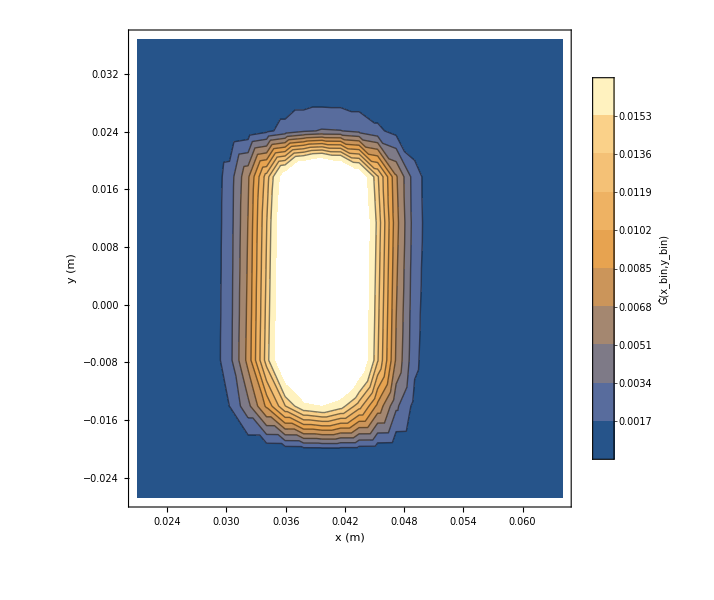

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dXDShift/a-1060/"];
```

```mathematica
dXDShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dXDShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dXDShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dXDShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dXDShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dXDShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1040[[All,2]]/Total[dXDShiftSpectruma1040[[All,2]]]}]];
dXDShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1045[[All,2]]/Total[dXDShiftSpectruma1045[[All,2]]]}]];
dXDShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]]}]];
dXDShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dXDShiftSpectruma1060[[All,2]]/Total[dXDShiftSpectruma1060[[All,2]]]}]];
```

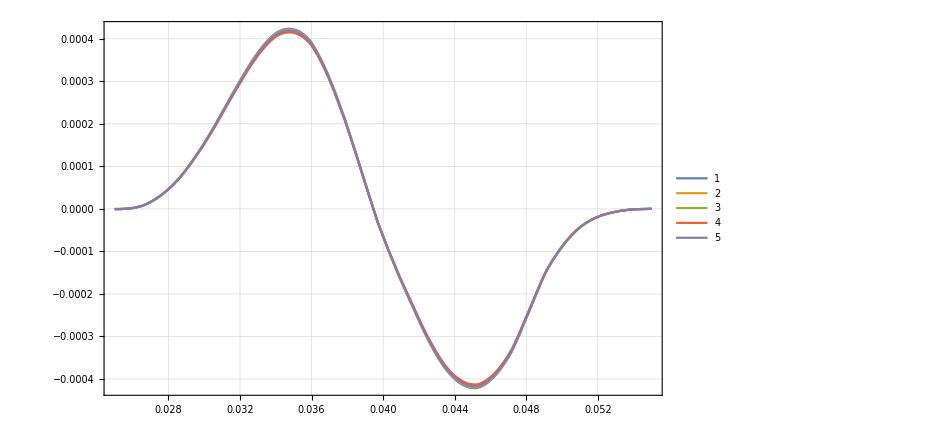

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dXDShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dXDShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dXDShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dXDShiftDataList={dXDShiftSpectruma1040[[All,2]]/Total[dXDShiftSpectruma1040[[All,2]]],dXDShiftSpectruma1045[[All,2]]/Total[dXDShiftSpectruma1045[[All,2]]],dXDShiftSpectruma0[[All,2]]/Total[dXDShiftSpectruma0[[All,2]]],dXDShiftSpectruma1055[[All,2]]/Total[dXDShiftSpectruma1055[[All,2]]],dXDShiftSpectruma1060[[All,2]]/Total[dXDShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

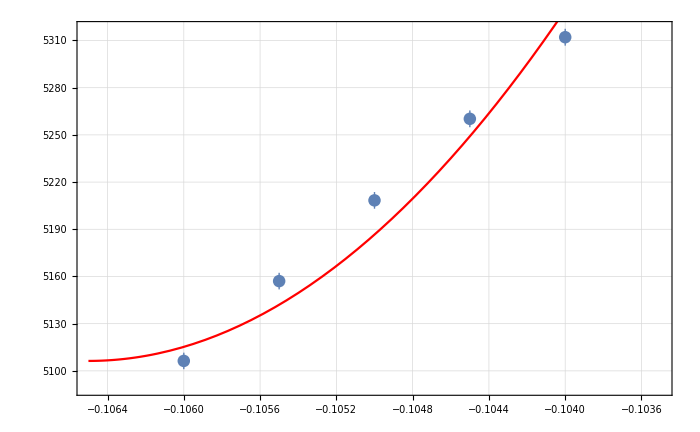
{{{5.31209×10^-6,5.26021×10^-6,5.20838×10^-6,5.15706×10^-6,5.10632×10^-6},{5.35579×10^-9,5.32937×10^-9,5.30264×10^-9,5.27631×10^-9,5.24994×10^-9}},a0 =  | -0.1065
FittedModel[5.10632×10^-6+0.0356891 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.000242302 | -439.533 | 5.17622×10^-6
scale | 0.0356891 | 0.00566881 | 6.2957 | 0.0243133
yoffset | 5.10632×10^-6 | 1.13065×10^-8 | 451.627 | 4.90272×10^-6 | 
 | DF | SS | MS
Model | 3 | 4.82403×10^6 | 1.60801×10^6
Error | 2 | 42.6424 | 21.3212
Uncorrected Total | 5 | 4.82407×10^6 | 
Corrected Total | 4 | 941.957 |  | ,-Graphics-}

```mathematica
dXDShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dXDShiftDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

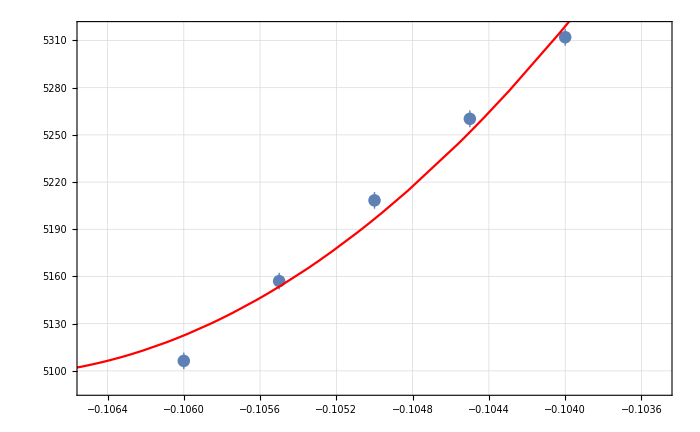
{{{5.31209×10^-6,5.26021×10^-6,5.20838×10^-6,5.15706×10^-6,5.10632×10^-6},{5.35579×10^-9,5.32937×10^-9,5.30264×10^-9,5.27631×10^-9,5.24994×10^-9}},a0 =  | -0.107033
FittedModel[5.09672×10^-6+0.0241705 (0.107033+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.107033 | 0.000480965 | -222.538 | 0.000020192
scale | 0.0241705 | 0.00566881 | 4.26377 | 0.0508474
yoffset | 5.09672×10^-6 | 2.17322×10^-8 | 234.523 | 0.0000181809 | 
 | DF | SS | MS
Model | 3 | 4.82405×10^6 | 1.60802×10^6
Error | 2 | 19.0747 | 9.53736
Uncorrected Total | 5 | 4.82407×10^6 | 
Corrected Total | 4 | 941.957 |  | ,-Graphics-}

```mathematica
dXDShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dXDShiftDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10703276961983176+0.105)/-0.105)/(0.0001)
```

193.597

# dYDShift, k=29.62

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1050/"];
```

```mathematica
dYDShiftSubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1050_179-264.txt}

```mathematica
dYDShiftSpectruma0=Flatten[Table[Import[dYDShiftSubFileNamesa0[[i]],"Table"],{i,1,Length[dYDShiftSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1040/"];
```

```mathematica
dYDShiftSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dYDShift_a-1040_179-264.txt}

```mathematica
dYDShiftSpectruma1040=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1045/"];
```

```mathematica
dYDShiftSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1045_179-264.txt}

```mathematica
dYDShiftSpectruma1045=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1055/"];
```

```mathematica
dYDShiftSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_D_dYDShift_a-1055_179-264.txt}

```mathematica
dYDShiftSpectruma1055=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

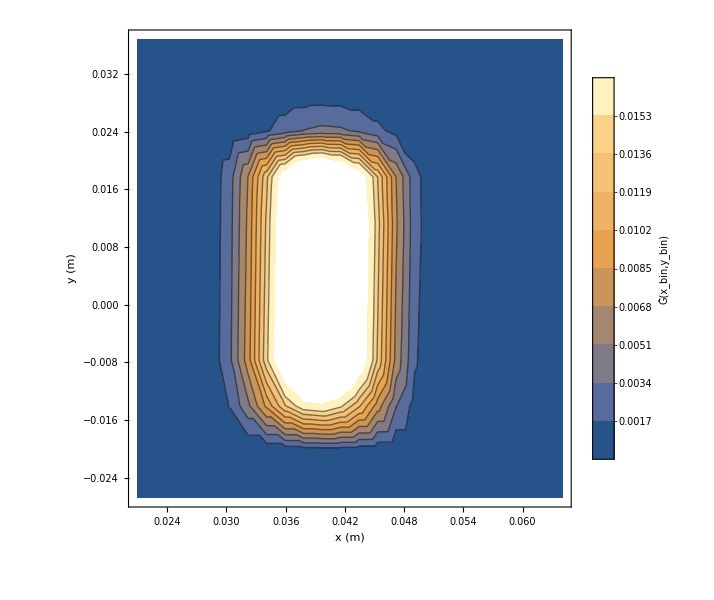

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dYDShift/a-1060/"];
```

```mathematica
dYDShiftSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_G_dYDShift_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dYDShiftSpectruma1060=Flatten[Import[#,"Table"]&/@dYDShiftSubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dYDShiftSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dYDShiftSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1040[[All,2]]/Total[dYDShiftSpectruma1040[[All,2]]]}]];
dYDShiftSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1045[[All,2]]/Total[dYDShiftSpectruma1045[[All,2]]]}]];
dYDShiftSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]]}]];
dYDShiftSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dYDShiftSpectruma1060[[All,2]]/Total[dYDShiftSpectruma1060[[All,2]]]}]];
```

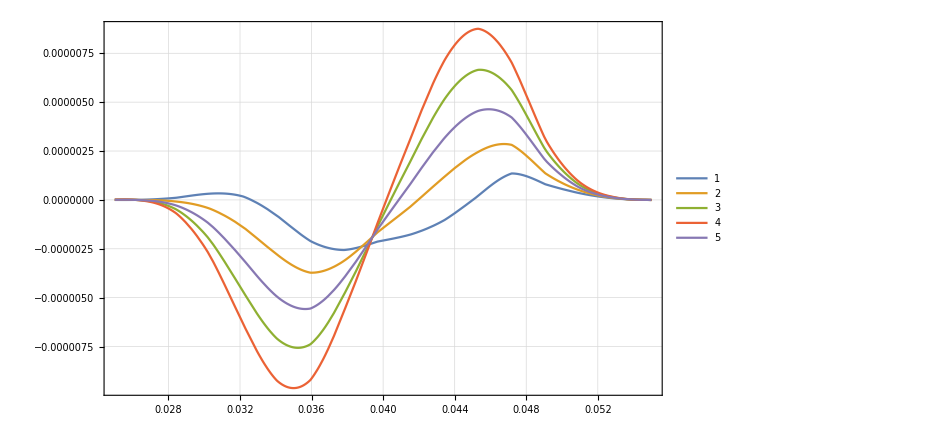

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dYDShiftSpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dYDShiftSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dYDShiftDataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dYDShiftDataList={dYDShiftSpectruma1040[[All,2]]/Total[dYDShiftSpectruma1040[[All,2]]],dYDShiftSpectruma1045[[All,2]]/Total[dYDShiftSpectruma1045[[All,2]]],dYDShiftSpectruma0[[All,2]]/Total[dYDShiftSpectruma0[[All,2]]],dYDShiftSpectruma1055[[All,2]]/Total[dYDShiftSpectruma1055[[All,2]]],dYDShiftSpectruma1060[[All,2]]/Total[dYDShiftSpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

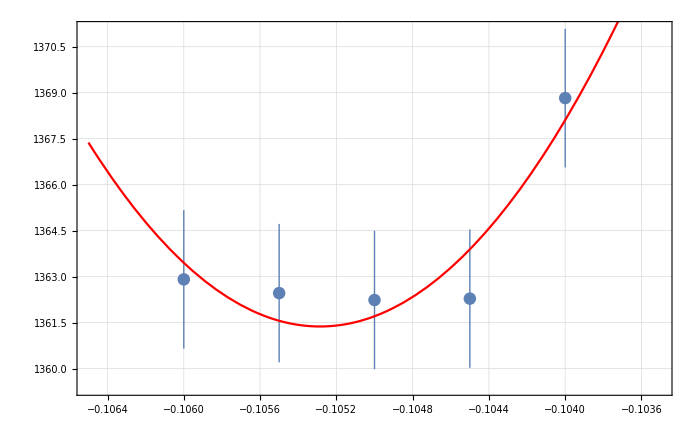
{{{1.36883×10^-6,1.36228×10^-6,1.36224×10^-6,1.36246×10^-6,1.36291×10^-6},{2.26056×10^-9,2.25611×10^-9,2.25655×10^-9,2.2573×10^-9,2.25836×10^-9}},a0 =  | -0.105286
FittedModel[1.36137×10^-6+0.00407102 (0.105286+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105286 | 0.000243972 | -431.549 | 5.36952×10^-6
scale | 0.00407102 | 0.00241416 | 1.68631 | 0.233783
yoffset | 1.36137×10^-6 | 1.48442×10^-9 | 917.108 | 1.18893×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.8242×10^6 | 608068.
Error | 2 | 0.879927 | 0.439963
Uncorrected Total | 5 | 1.8242×10^6 | 
Corrected Total | 4 | 6.37621 |  | ,-Graphics-}

```mathematica
dYDShiftInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dYDShiftDataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

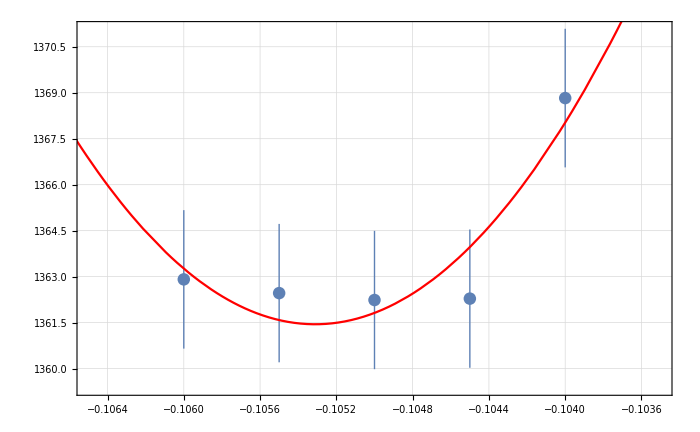
{{{1.36883×10^-6,1.36228×10^-6,1.36224×10^-6,1.36246×10^-6,1.36291×10^-6},{2.26056×10^-9,2.25611×10^-9,2.25655×10^-9,2.2573×10^-9,2.25836×10^-9}},a0 =  | -0.105311
FittedModel[1.36145×10^-6+0.00382789 (0.105311+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105311 | 0.000270657 | -389.094 | 6.60522×10^-6
scale | 0.00382789 | 0.00241416 | 1.5856 | 0.253711
yoffset | 1.36145×10^-6 | 1.47058×10^-9 | 925.788 | 1.16674×10^-6 | 
 | DF | SS | MS
Model | 3 | 1.8242×10^6 | 608068.
Error | 2 | 0.89164 | 0.44582
Uncorrected Total | 5 | 1.8242×10^6 | 
Corrected Total | 4 | 6.37621 |  | ,-Graphics-}

```mathematica
dYDShiftInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dYDShiftDataList,bList, 4]
```

```mathematica
-0.1065
```

```mathematica
0.00025
```

```mathematica
((-0.10531106171262236+0.105)/-0.105)/(0.0001)
```

29.6249

# dXDShift, k=193.6

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1050/"];
```

```mathematica
dxAASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_1-49.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_50-98.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_99-106.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_107-122.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_123-138.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_139-154.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_155-178.txt,TransferResult_08-09-20_SC_opt_C_dxAA_a-1050_179-264.txt}

```mathematica
dxAASpectruma0=Flatten[Table[Import[dxAASubFileNamesa0[[i]],"Table"],{i,1,Length[dxAASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1040/"];
```

```mathematica
dxAASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_1-49.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_50-98.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_99-106.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_107-122.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_123-138.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_139-154.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_155-178.txt,TransferResult_08-09-20_SC_opt_H_dxAA_a-1040_179-264.txt}

```mathematica
dxAASpectruma1040=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1045/"];
```

```mathematica
dxAASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1045_179-264.txt}

```mathematica
dxAASpectruma1045=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1055/"];
```

```mathematica
dxAASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_1-49.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_50-98.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_99-106.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_107-122.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_123-138.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_139-154.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_155-178.txt,TransferResult_08-09-20_SC_opt_G_dxAA_a-1055_179-264.txt}

```mathematica
dxAASpectruma1055=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

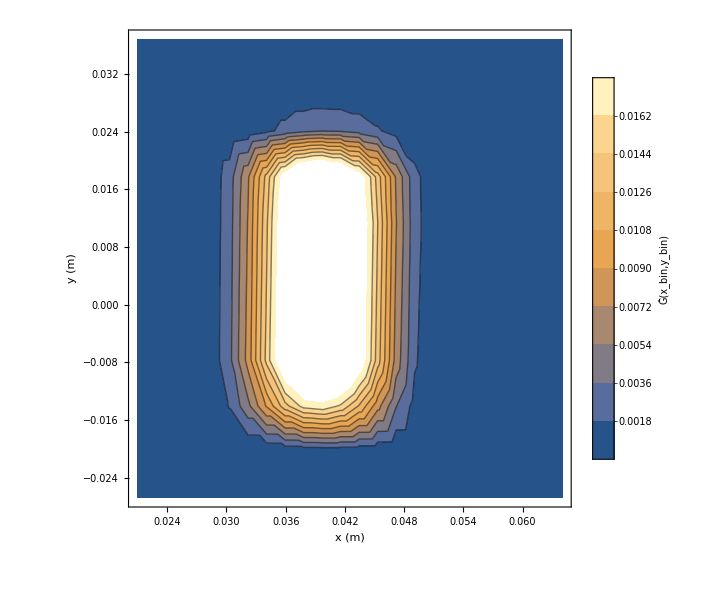

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_dxAA/a-1060/"];
```

```mathematica
dxAASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_1-49.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_50-98.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_99-106.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_107-122.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_123-138.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_139-154.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_155-178.txt,TransferResult_08-09-20_SC_opt_D_dxAA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dxAASpectruma1060=Flatten[Import[#,"Table"]&/@dxAASubFileNamesa1060,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,0.025,0.055},{y,-0.02,0.03},PlotRange->All]
```

-Graphics3D-

```mathematica
dxAASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]]}]];
```

```mathematica
Plot[RefSpectrumInter[x,0.],{x,0.025,0.055},PlotRange->All]
```

-Graphics-

```mathematica
dxAASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]]}]];
dxAASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]]}]];
dxAASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]]}]];
dxAASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]}]];
```

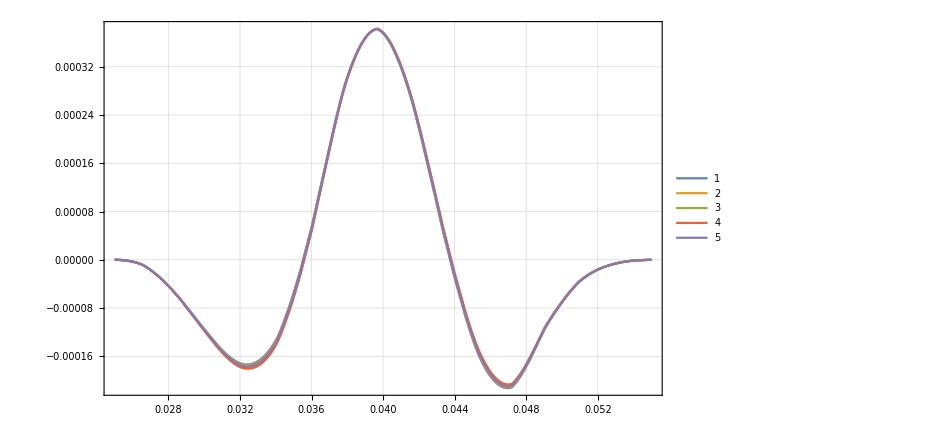

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dxAASpectruma1040Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1045Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1055Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma1060Inter[x,0.],
RefSpectrumInter[x,0.]-dxAASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[BDataList,bList,TransferToRefParableFitForProtons,dxAADataList]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
dxAADataList={dxAASpectruma1040[[All,2]]/Total[dxAASpectruma1040[[All,2]]],dxAASpectruma1045[[All,2]]/Total[dxAASpectruma1045[[All,2]]],dxAASpectruma0[[All,2]]/Total[dxAASpectruma0[[All,2]]],dxAASpectruma1055[[All,2]]/Total[dxAASpectruma1055[[All,2]]],dxAASpectruma1060[[All,2]]/Total[dxAASpectruma1060[[All,2]]]};
```

```mathematica
bList={-.104 ,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

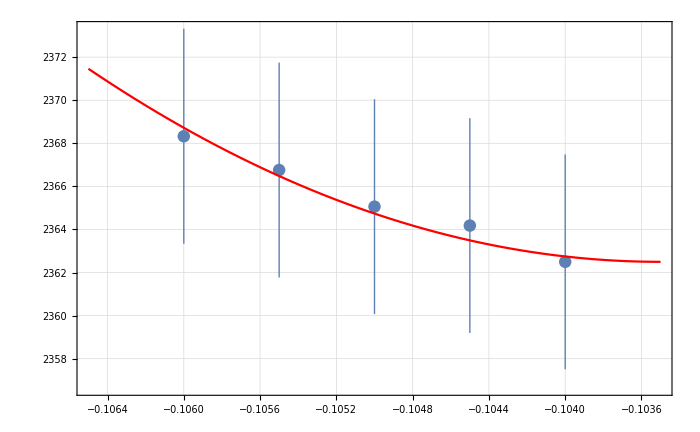
{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.1035
FittedModel[2.3625×10^-6+0.000995836 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.00818383 | -12.6469 | 0.00619416
scale | 0.000995836 | 0.00533118 | 0.186795 | 0.869054
yoffset | 2.3625×10^-6 | 1.06922×10^-8 | 220.954 | 0.0000204824 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0349819 | 0.0174909
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
dxAAInvest=TransferToRefParableFitForProtons[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

```mathematica
((-0.1065+0.105)/-0.105)/(0.0002)
```

71.4286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

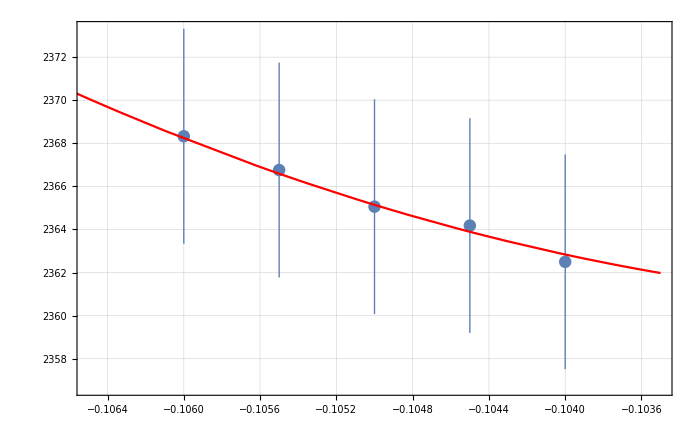
{{{2.3625×10^-6,2.36418×10^-6,2.36506×10^-6,2.36676×10^-6,2.36833×10^-6},{4.98419×10^-9,4.98565×10^-9,4.9865×10^-9,4.98833×10^-9,4.98983×10^-9}},a0 =  | -0.101557
FittedModel[2.3605×10^-6+0.000391815 (0.101557+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.101557 | 0.047012 | -2.16024 | 0.16334
scale | 0.000391815 | 0.00533118 | 0.073495 | 0.948101
yoffset | 2.3605×10^-6 | 6.15185×10^-8 | 38.3705 | 0.000678519 | 
 | DF | SS | MS
Model | 3 | 1.12488×10^6 | 374959.
Error | 2 | 0.0097655 | 0.00488275
Uncorrected Total | 5 | 1.12488×10^6 | 
Corrected Total | 4 | 0.821765 |  | ,-Graphics-}

```mathematica
dxAAInvest2=TransferToRefParableFitForProtonsUnlimited[RefSpectrum[[All,2]],dxAADataList,bList, 4]
```

```mathematica
-0.1065
```

-0.1065

```mathematica
0.00025
```

0.00025

```mathematica
0.2/1000
```

0.0002

```mathematica
((-0.1035+0.105)/-0.105)/(0.0002)
```

-71.4286

```mathematica
((-0.10155733953850894+0.105)/-0.105)/(0.0002)
```

-163.936

# Diff Aperture

## da0 Smaller 1D xAASC=2/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_2mm/a-1050/"];
```

```mathematica
d0SubFileNamesa01D2mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_2mm_a-1050_57-64.txt}

```mathematica
d0Spectruma01D2mm=Flatten[Table[Import[d0SubFileNamesa01D2mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D2mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

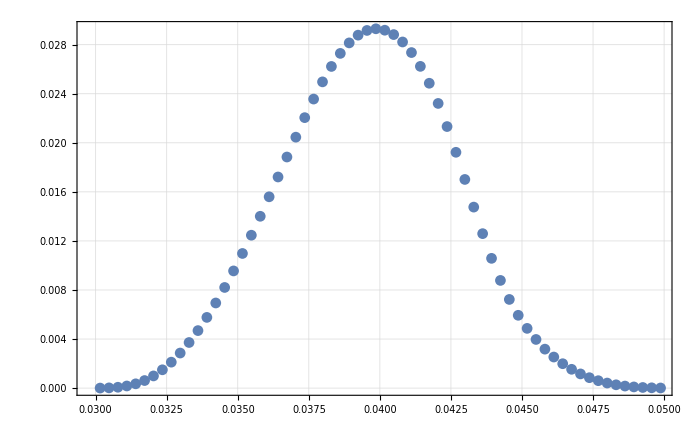

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]}]]
```

```mathematica
da0Spectrum1D2mmInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]/Total[d0Spectruma01D2mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y_2mm/a1050/"];
```

```mathematica
d0SubFileNamesa01D2mma1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_da0_64x1y_2mm_a1050_57-64.txt}

```mathematica
d0Spectruma01D2mma1050=Flatten[Table[Import[d0SubFileNamesa01D2mma1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D2mma1050]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

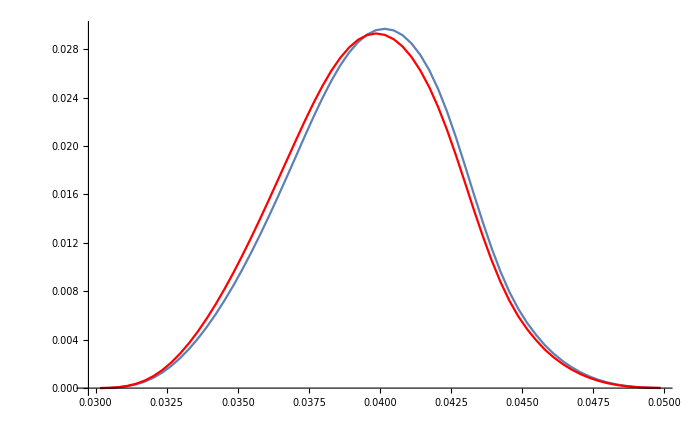

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],-d0Spectruma01D2mma1050[[All,2]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mm[[All,2]]}],PlotStyle->Red]]
```

```mathematica
da0Spectrum1D2mmIntera1050=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D2mma1050[[All,2]]/Total[d0Spectruma01D2mma1050[[All,2]]]}]];
```

## da0 Smaller 1D xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y/a-1050/"];
```

```mathematica
d0SubFileNamesa01D=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a-1050_57-64.txt}

```mathematica
d0Spectruma01D=Flatten[Table[Import[d0SubFileNamesa01D[[i]],"Table"],{i,1,Length[d0SubFileNamesa01D]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

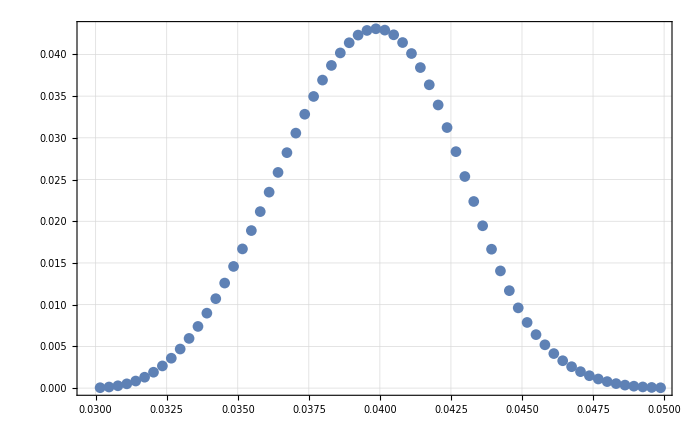

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]}]]
```

```mathematica
da0Spectrum1DInter=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]/Total[d0Spectruma01D[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_64x1y/a1050/"];
```

```mathematica
d0SubFileNamesa01Da1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_da0_64x1y_a1050_57-64.txt}

```mathematica
d0Spectruma01Da1050=Flatten[Table[Import[d0SubFileNamesa01Da1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa01Da1050]}],1];
```

```mathematica
Total[d0Spectruma01Da1050[[All,1]]]/16
```

47500.6

```mathematica
UnitConvert[Quantity[47500.5602468125,"Seconds"],"Hours"]
```

13.1946 h

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins1D=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1D=BinCenters[xyBins1D];
```

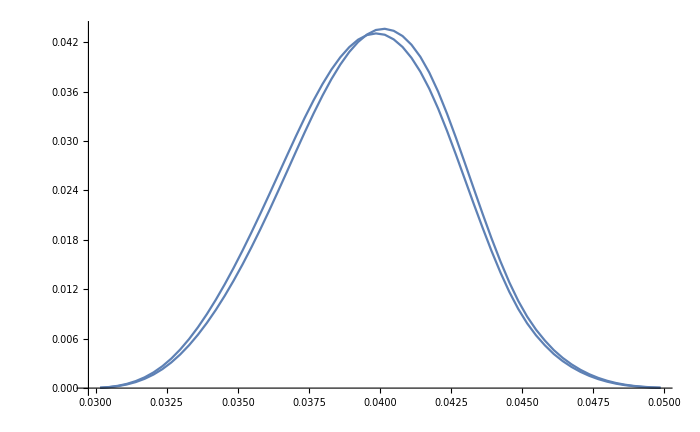

```mathematica
Show[ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da1050[[All,2]]}]],ListLinePlot[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01D[[All,2]]}]]]
```

```mathematica
da0Spectrum1DIntera1050=Interpolation[Transpose[{XYBinCentersYHalf1D[[All,1]],d0Spectruma01Da1050[[All,2]]/Total[d0Spectruma01Da1050[[All,2]]]}]];
```

## da0 Normal xAASC=7/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0small=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0small=Flatten[Table[Import[d0SubFileNamesa0small[[i]],"Table"],{i,1,Length[d0SubFileNamesa0small]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
0.05-0.03
```

0.02

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0small[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumIntersmall=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0small[[All,2]]/Total[d0Spectruma0small[[All,2]]]}]];
```

## drD Smaller Aperture, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];
Length[drDSubFileNamesa0]
```

8

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""];Length[drDSubFileNamesa1040]
```

8

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""];Length[drDSubFileNamesa1045]
```

8

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""];Length[drDSubFileNamesa1055]
```

8

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

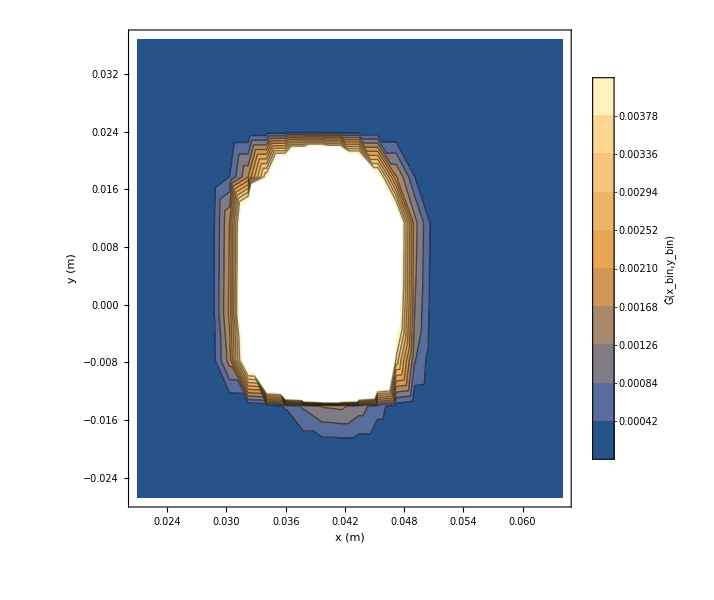

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

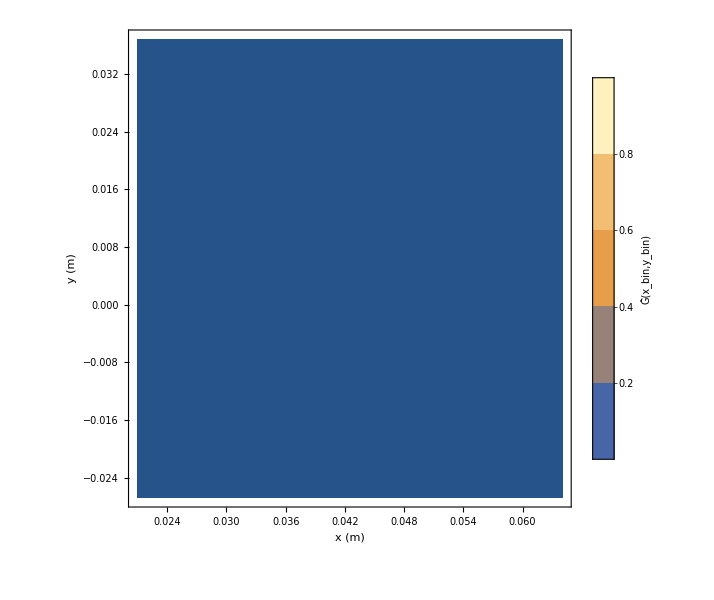

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
Length[drDSubFileNamesa1060]
```

{TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_drD_a-1060_179-264.txt}

8

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumIntersmall[x,0.]-drDSpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumIntersmall[x,0.]-drDSpectruma1040Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1045Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1055Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma1060Inter[x,0.],
d0SpectrumIntersmall[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

### manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rDDataList={drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rDInvest=TransferToRefParableFitForProtons[d0Spectruma0small[[All,2]],rDDataList,bList, 4]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

NonlinearModelFit::wts: The value of option Weights -> {100000000/((0.00247884+Symbol[]^2/Total[«1»]^2) (-0.049788+Symbol[] Power[«2»])^2+(0.00246245+Symbol[]^2/Total[«1»]^2) (-0.0496231+Symbol[] Power[«2»])^2+«47»+(2.0258×10^-6+Symbol[]^2/Total[«1»]^2) (-0.00142331+Symbol[] Power[«2»])^2+«38»),100000000/((0.00247878+Symbol[]^2/Total[«1»]^2) (-0.0497873+Symbol[] Power[«2»])^2+«49»+«38»),100000000/((0.00247871+(«1»)^2/(«1»)^2) (-«21»+«1»)^2+«49»+«38»),100000000/((0.00247865+Symbol[]^2/Total[«1»]^2) (-0.0497861+«1»)^2+«49»+«38»),100000000/((0.00247859+Symbol[]^2/Total[«1»]^2) (-0.0497854+Symbol[] Power[«2»])^2+«49»+«38»)} should be a list of real numbers or a pure function.

Part::partd: Part specification NonlinearModelFit[«1»][BestFitParameters]⟦1,2⟧ is longer than depth of object.

NonlinearModelFit::wts: The value of option Weights -> {100000000/((0.00247884+Symbol[]^2/Total[«1»]^2) (-0.049788+Symbol[] Power[«2»])^2+(0.00246245+Symbol[]^2/Total[«1»]^2) (-0.0496231+Symbol[] Power[«2»])^2+«47»+(2.0258×10^-6+Symbol[]^2/Total[«1»]^2) (-0.00142331+Symbol[] Power[«2»])^2+«38»),100000000/((0.00247878+Symbol[]^2/Total[«1»]^2) (-0.0497873+Symbol[] Power[«2»])^2+«49»+«38»),100000000/((0.00247871+(«1»)^2/(«1»)^2) (-«21»+«1»)^2+«49»+«38»),100000000/((0.00247865+Symbol[]^2/Total[«1»]^2) (-0.0497861+«1»)^2+«49»+«38»),100000000/((0.00247859+Symbol[]^2/Total[«1»]^2) (-0.0497854+Symbol[] Power[«2»])^2+«49»+«38»)} should be a list of real numbers or a pure function.

NonlinearModelFit::wts: The value of option Weights -> {(1.×10^8)/((0.00247884+Symbol[]^2/Total[«1»]^2) (-0.049788+Symbol[] Power[«2»])^2+(0.00246245+Symbol[]^2/Total[«1»]^2) (-0.0496231+Symbol[] Power[«2»])^2+«47»+(2.0258×10^-6+Symbol[]^2/Total[«1»]^2) (-0.00142331+Symbol[] Power[«2»])^2+«38»),(1.×10^8)/((0.00247878+Symbol[]^2/Total[«1»]^2) (-0.0497873+Symbol[] Power[«2»])^2+«49»+«38»),(1.×10^8)/((0.00247871+(«6»«1»«1»)^2/(«1»)^2) (-«21»+«1»)^2+«49»+«38»),(1.×10^8)/((0.00247865+Symbol[]^2/Total[«1»]^2) (-0.0497861+«1»)^2+«49»+«38»),(1.×10^8)/((0.00247859+Symbol[]^2/Total[«1»]^2) (-0.0497854+Symbol[] Power[«2»])^2+«49»+«38»)} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Part::partd: Part specification NonlinearModelFit[«1»][BestFitParameters]⟦1,2⟧ is longer than depth of object.

{1}
 |  |  |  |

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0small[[All,2]],rDDataList,bList, 4]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

NonlinearModelFit::wts: The value of option Weights -> {100000000/((0.00247884+Symbol[]^2/Total[«1»]^2) (-0.049788+Symbol[] Power[«2»])^2+(0.00246245+Symbol[]^2/Total[«1»]^2) (-0.0496231+Symbol[] Power[«2»])^2+«47»+(2.0258×10^-6+Symbol[]^2/Total[«1»]^2) (-0.00142331+Symbol[] Power[«2»])^2+«38»),100000000/((0.00247878+Symbol[]^2/Total[«1»]^2) (-0.0497873+Symbol[] Power[«2»])^2+«49»+«38»),100000000/((0.00247871+(«1»)^2/(«1»)^2) (-«21»+«1»)^2+«49»+«38»),100000000/((0.00247865+Symbol[]^2/Total[«1»]^2) (-0.0497861+«1»)^2+«49»+«38»),100000000/((0.00247859+Symbol[]^2/Total[«1»]^2) (-0.0497854+Symbol[] Power[«2»])^2+«49»+«38»)} should be a list of real numbers or a pure function.

Part::partd: Part specification NonlinearModelFit[«1»][BestFitParameters]⟦1,2⟧ is longer than depth of object.

NonlinearModelFit::wts: The value of option Weights -> {100000000/((0.00247884+Symbol[]^2/Total[«1»]^2) (-0.049788+Symbol[] Power[«2»])^2+(0.00246245+Symbol[]^2/Total[«1»]^2) (-0.0496231+Symbol[] Power[«2»])^2+«47»+(2.0258×10^-6+Symbol[]^2/Total[«1»]^2) (-0.00142331+Symbol[] Power[«2»])^2+«38»),100000000/((0.00247878+Symbol[]^2/Total[«1»]^2) (-0.0497873+Symbol[] Power[«2»])^2+«49»+«38»),100000000/((0.00247871+(«1»)^2/(«1»)^2) (-«21»+«1»)^2+«49»+«38»),100000000/((0.00247865+Symbol[]^2/Total[«1»]^2) (-0.0497861+«1»)^2+«49»+«38»),100000000/((0.00247859+Symbol[]^2/Total[«1»]^2) (-0.0497854+Symbol[] Power[«2»])^2+«49»+«38»)} should be a list of real numbers or a pure function.

NonlinearModelFit::wts: The value of option Weights -> {(1.×10^8)/((0.00247884+Symbol[]^2/Total[«1»]^2) (-0.049788+Symbol[] Power[«2»])^2+(0.00246245+Symbol[]^2/Total[«1»]^2) (-0.0496231+Symbol[] Power[«2»])^2+«47»+(2.0258×10^-6+Symbol[]^2/Total[«1»]^2) (-0.00142331+Symbol[] Power[«2»])^2+«38»),(1.×10^8)/((0.00247878+Symbol[]^2/Total[«1»]^2) (-0.0497873+Symbol[] Power[«2»])^2+«49»+«38»),(1.×10^8)/((0.00247871+(«6»«1»«1»)^2/(«1»)^2) (-«21»+«1»)^2+«49»+«38»),(1.×10^8)/((0.00247865+Symbol[]^2/Total[«1»]^2) (-0.0497861+«1»)^2+«49»+«38»),(1.×10^8)/((0.00247859+Symbol[]^2/Total[«1»]^2) (-0.0497854+Symbol[] Power[«2»])^2+«49»+«38»)} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

Part::partd: Part specification NonlinearModelFit[«1»][BestFitParameters]⟦1,2⟧ is longer than depth of object.

{1}
 |  |  |  |

```mathematica
|
```

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

NonlinearModelFit::wts: The value of option Weights -> {100000000/((0.00247884+Symbol[]^2/Total[«1»]^2) (-0.049788+Symbol[] Power[«2»])^2+(0.00246245+Symbol[]^2/Total[«1»]^2) (-0.0496231+Symbol[] Power[«2»])^2+«47»+(2.0258×10^-6+Symbol[]^2/Total[«1»]^2) (-0.00142331+Symbol[] Power[«2»])^2+«38»),100000000/((0.00247878+Symbol[]^2/Total[«1»]^2) (-0.0497873+Symbol[] Power[«2»])^2+«49»+«38»),100000000/((0.00247871+(«1»)^2/(«1»)^2) (-«21»+«1»)^2+«49»+«38»),100000000/((0.00247865+Symbol[]^2/Total[«1»]^2) (-0.0497861+«1»)^2+«49»+«38»),100000000/((0.00247859+Symbol[]^2/Total[«1»]^2) (-0.0497854+Symbol[] Power[«2»])^2+«49»+«38»)} should be a list of real numbers or a pure function.

Part::partd: Part specification NonlinearModelFit[«1»][BestFitParameters]⟦1,2⟧ is longer than depth of object.

-95238.1 (0.105+NonlinearModelFit[{{-0.104,(-0.049788+Symbol[]/Total[Symbol[]])^2+(-0.0496231+Symbol[]/Total[Symbol[]])^2+(-0.0485093+Symbol[]/Total[Symbol[]])^2+(-0.0446554+Symbol[]/Total[Symbol[]])^2+(-0.0440944+Symbol[]/Total[Symbol[]])^2+79+(-5.57402×10^-9+Symbol[]/Total[Symbol[]])^2+(-5.19125×10^-9+Symbol[]/Total[Symbol[]])^2+(-7.73958×10^-10+Symbol[]/Total[Symbol[]])^2+177 (0.+Symbol[]/Total[Symbol[]])^2},3,{-0.106,(-0.0497854+Symbol[]/Total[1])^2+(-21+1)^2+84+(1)^2+177 (0.+1/1)^2}},6,PrecisionGoal→10][BestFitParameters]⟦1,2⟧)
 |  |  |  |

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-95238.1 (0.105+NonlinearModelFit[{{-0.104,(-0.049788+Symbol[]/Total[Symbol[]])^2+(-0.0496231+Symbol[]/Total[Symbol[]])^2+(-0.0485093+Symbol[]/Total[Symbol[]])^2+(-0.0446554+Symbol[]/Total[Symbol[]])^2+(-0.0440944+Symbol[]/Total[Symbol[]])^2+79+(-5.57402×10^-9+Symbol[]/Total[Symbol[]])^2+(-5.19125×10^-9+Symbol[]/Total[Symbol[]])^2+(-7.73958×10^-10+Symbol[]/Total[Symbol[]])^2+177 (0.+Symbol[]/Total[Symbol[]])^2},3,{-0.106,(-0.0497854+Symbol[]/Total[1])^2+(-21+1)^2+84+(1)^2+177 (0.+1/1)^2}},6,PrecisionGoal→10][BestFitParameters]⟦1,2⟧)
 |  |  |  |

## da0 Smaller 44 Bins xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller44=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_a-1050_179-264.txt}

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
d0Spectruma0smaller44=Flatten[Table[Import[d0SubFileNamesa0smaller44[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller44]}],1];
```

```mathematica
XYBinCentersYHalf44=BinCenters[xyBins44];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins132=bin2DGen[xStart,xEnd,yStart,yEnd,132,2];
```

```mathematica
XYBinCentersYHalf132=BinCenters[xyBins132];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma0smaller44[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
da0Spectrum44BinsInter=Interpolation[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma0smaller44[[All,2]]/Total[d0Spectruma0smaller44[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins/a1050/"];
```

```mathematica
d0SubFileNamesa1050smaller44=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_a1050_179-264.txt}

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
d0Spectruma1050smaller44=Flatten[Table[Import[d0SubFileNamesa1050smaller44[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050smaller44]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],-d0Spectruma1050smaller44[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
da1050Spectrum44BinsInter=Interpolation[Transpose[{XYBinCentersYHalf44[[All,1]],XYBinCentersYHalf44[[All,2]],d0Spectruma1050smaller44[[All,2]]/Total[d0Spectruma1050smaller44[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

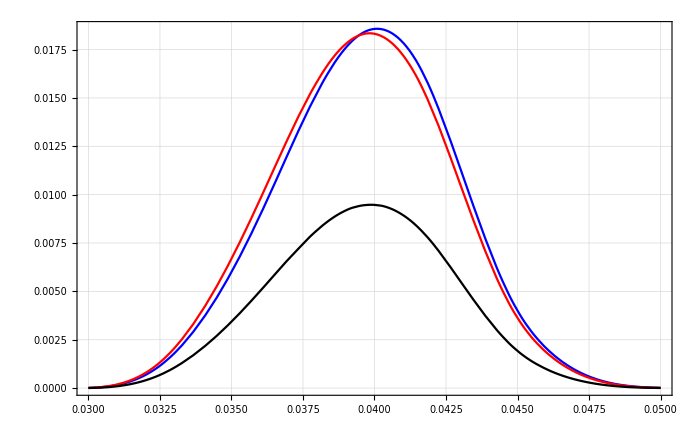

```mathematica
Show[Plot[da1050Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

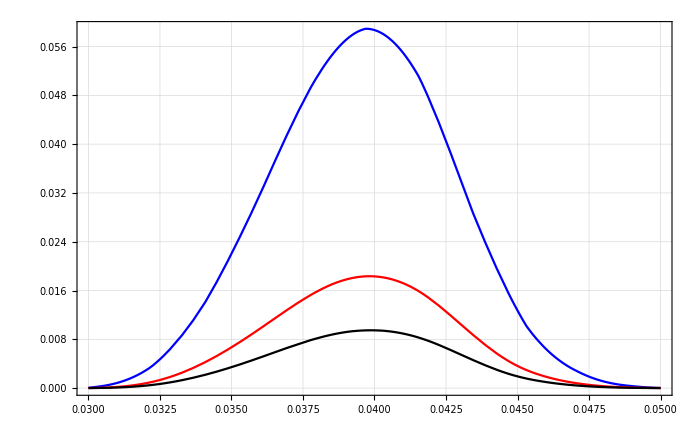

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Blue],Plot[da0Spectrum44BinsInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[da0Spectrum135BinsInter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

InterpolatingFunction::dmval: Input value {0.0300004,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

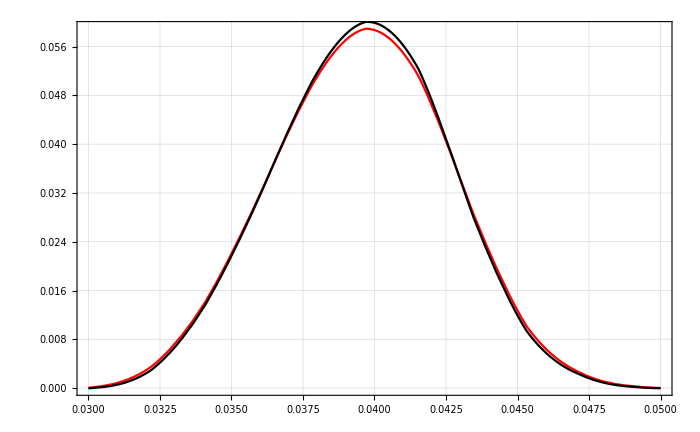

```mathematica
Show[Plot[d0Spectruma0smallerInter[x,0],{x,0.03,0.05},PlotStyle->Red],Plot[d0Spectruma0smaller2Inter[x,0],{x,0.03,0.05},PlotStyle->Black]]
```

## da0 Smaller 132 Bins xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller132Bins/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller132=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller132Bins_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller132=Flatten[Table[Import[d0SubFileNamesa0smaller132[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller132]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins132=bin2DGen[xStart,xEnd,yStart,yEnd,132,2];
```

```mathematica
XYBinCentersYHalf132=BinCenters[xyBins132];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf132[[All,1]],XYBinCentersYHalf132[[All,2]],d0Spectruma0smaller132[[All,2]]}]]
```

-Graphics3D-

```mathematica
da0Spectrum135BinsInter=Interpolation[Transpose[{XYBinCentersYHalf132[[All,1]],XYBinCentersYHalf132[[All,2]],d0Spectruma0smaller132[[All,2]]/Total[d0Spectruma0smaller132[[All,2]]]}]];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,1}.

## da0 Smaller xAASC=3/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller=Flatten[Table[Import[d0SubFileNamesa0smaller[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]}],PlotRange->{All,{-0.022,0.025}}]
```

-Graphics3D-

```mathematica
d0Spectruma0smallerInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]/Total[d0Spectruma0smaller[[All,2]]]}]];
```

## a=-0.105 2/1000 aperture

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller2/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller2=Flatten[Table[Import[d0SubFileNamesa0smaller2[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller2]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller2[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller2Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller2[[All,2]]/Total[d0Spectruma0smaller2[[All,2]]]}]];
```

## a=0.105 2/1000 aperture

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller2/a1050/"];
```

```mathematica
d0SubFileNamesa1050smaller2=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller2_a1050_179-264.txt}

```mathematica
d0Spectruma1050smaller2=Flatten[Table[Import[d0SubFileNamesa1050smaller2[[i]],"Table"],{i,1,Length[d0SubFileNamesa1050smaller2]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050smaller2[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma1050smaller2Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma1050smaller2[[All,2]]/Total[d0Spectruma1050smaller2[[All,2]]]}]];
```

## da0 Smaller4mm xAASC=4/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_4mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller4mm=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_C_da0_smaller44Bins_4mm_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller4mm=Flatten[Table[Import[d0SubFileNamesa0smaller4mm[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4mm]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller4mm[[All,1]]]/16,"Seconds"],"Hours"]
```

22.0444 h

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4mm[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4mmInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4mm[[All,2]]/Total[d0Spectruma0smaller4mm[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_4mm/a1050/"];
```

```mathematica
d0SubFileNamesa0smaller4a1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller44Bins_4mm_a1050_179-264.txt}

```mathematica
d0Spectruma0smaller4a1050=Flatten[Table[Import[d0SubFileNamesa0smaller4a1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4a1050]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
UnitConvert[Quantity[Total[d0Spectruma0smaller4a1050[[All,1]]]/4,"Seconds"],"Hours"]/24
```

3.6871 h

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4a1050[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4Intera1050=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4a1050[[All,2]]/Total[d0Spectruma0smaller4a1050[[All,2]]]}]];
```

## da0 Smaller5 xAASC=5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_5mm/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller5=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller5=Flatten[Table[Import[d0SubFileNamesa0smaller5[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller5]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller5Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5[[All,2]]/Total[d0Spectruma0smaller5[[All,2]]]}]];
```

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller44Bins_5mm/a1050/"];
```

```mathematica
d0SubFileNamesa0smaller5a1050=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_D_da0_smaller44Bins_5mm_a1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller44Bins_5mm_a1050_179-264.txt}

```mathematica
d0Spectruma0smaller5a1050=Flatten[Table[Import[d0SubFileNamesa0smaller5a1050[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller5a1050]}],1];
```

```mathematica
xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,6];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins44];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5a1050[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller5Intera1050=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller5a1050[[All,2]]/Total[d0Spectruma0smaller5a1050[[All,2]]]}]];
```

## da0 Smaller3 xAASC=1/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller3/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller3=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_G_da0_smaller3_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller3=Flatten[Table[Import[d0SubFileNamesa0smaller3[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller3]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller3[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller3Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller3[[All,2]]/Total[d0Spectruma0smaller3[[All,2]]]}]];
```

## da0 Smaller4 xAASC=2.5/1000; yAASC=25/1000;

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_smaller4/a-1050/"];
```

```mathematica
d0SubFileNamesa0smaller4=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffApt_H_da0_smaller4_a-1050_179-264.txt}

```mathematica
d0Spectruma0smaller4=Flatten[Table[Import[d0SubFileNamesa0smaller4[[i]],"Table"],{i,1,Length[d0SubFileNamesa0smaller4]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0Spectruma0smaller4Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller4[[All,2]]/Total[d0Spectruma0smaller4[[All,2]]]}]];
```

## Testing

```mathematica
oneDSumming[list_,bins_,xBins_:24]:=Block[{transList,summedList,binsToSum,normalList},
transList=Transpose[{bins[[All,1]],bins[[All,2]],list[[All,2]]/Total[list[[All,2]]]}];
binsToSum=Length[bins]/xBins;
summedList=Table[{transList[[i,1]],Total[transList[[i;;i+binsToSum-1]][[All,3]]]},{i,1,Length[bins],binsToSum}];
normalList=Transpose[{summedList[[All,1]],summedList[[All,2]]/Total[summedList[[All,2]]]}];
Return[{summedList,normalList}]
]
```

```mathematica
oneDSummingY[list_,bins_,yBins_:11]:=Block[{transList,summedList,binsToSum,normalList},
transList=Transpose[{bins[[All,1]],bins[[All,2]],list[[All,2]]/Total[list[[All,2]]]}];
binsToSum=Length[bins]/yBins;
summedList=Table[{transList[[i,2]],Total[transList[[i;;i+binsToSum-1]][[All,3]]]},{i,1,Length[bins],binsToSum}];
normalList=Transpose[{summedList[[All,1]],summedList[[All,2]]/Total[summedList[[All,2]]]}];
Return[{summedList,normalList}]
]
```

```mathematica
onedysumsmaller=oneDSummingY[d0Spectruma0smaller,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller2=oneDSummingY[d0Spectruma0smaller2,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller3=oneDSummingY[d0Spectruma0smaller3,XYBinCentersYHalf];
```

```mathematica
onedysumsmaller4=oneDSummingY[d0Spectruma0smaller4,XYBinCentersYHalf];
```

```mathematica
onedsumsmaller=oneDSumming[d0Spectruma0smaller,XYBinCentersYHalf];onedsumsmaller2=oneDSumming[d0Spectruma0smaller2,XYBinCentersYHalf];onedsumsmaller3=oneDSumming[d0Spectruma0smaller3,XYBinCentersYHalf];onedsumsmaller4=oneDSumming[d0Spectruma0smaller4,XYBinCentersYHalf];
```

```mathematica
onedsumsmaller2p1050=oneDSumming[d0Spectruma1050smaller2,XYBinCentersYHalf];
```

```mathematica
264/44.
```

6.

```mathematica
onedysumsmaller44=oneDSummingY[d0Spectruma0smaller44,XYBinCentersYHalf44,6];
```

```mathematica
onedysumsmaller44p1050=oneDSummingY[d0Spectruma1050smaller44,XYBinCentersYHalf44,6];
```

```mathematica
onedysumsmaller132=oneDSummingY[d0Spectruma0smaller132,XYBinCentersYHalf132,2];
```

```mathematica
onedsumsmaller44=oneDSumming[d0Spectruma0smaller44,XYBinCentersYHalf44,44];
```

```mathematica
onedsumsmaller44p1050=oneDSumming[d0Spectruma1050smaller44,XYBinCentersYHalf44,44];
```

```mathematica
onedsumsmaller132=oneDSumming[d0Spectruma0smaller132,XYBinCentersYHalf132,132];
```

```mathematica
onedsumsmaller4[[1]]//Length
```

24

```mathematica
onedsumsmaller44[[1]]//Length
```

44

```mathematica
onedsumsmaller132[[1]]//Length
```

132

```mathematica
intersmaller=Interpolation[onedsumsmaller[[1]]];intersmaller2=Interpolation[onedsumsmaller2[[1]]];intersmaller3=Interpolation[onedsumsmaller3[[1]]];intersmaller4=Interpolation[onedsumsmaller4[[1]]];
```

```mathematica
intersmaller2p1050=Interpolation[onedsumsmaller2p1050[[1]]];
```

```mathematica
interysmaller=Interpolation[onedysumsmaller[[1]]];interysmaller2=Interpolation[onedysumsmaller2[[1]]];interysmaller3=Interpolation[onedysumsmaller3[[1]]];interysmaller4=Interpolation[onedysumsmaller4[[1]]];
```

```mathematica
intersmaller44=Interpolation[onedsumsmaller44[[1]]];
```

```mathematica
intersmaller44p1050=Interpolation[onedsumsmaller44p1050[[1]]];
```

```mathematica
intersmaller132=Interpolation[onedsumsmaller132[[1]],ExtrapolationHandler->0];
```

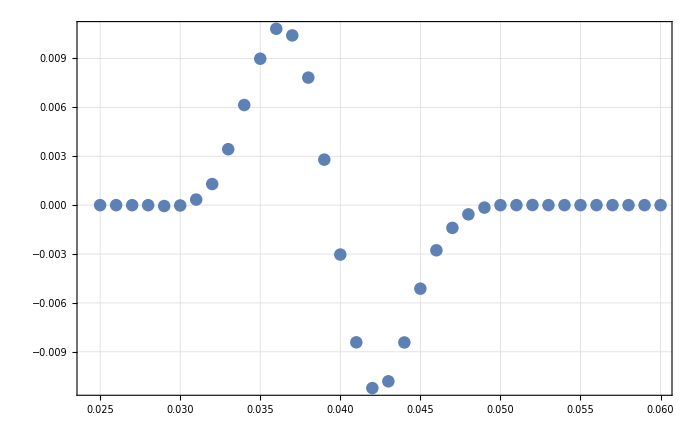

```mathematica
interdiffavalues24=ListPlot[Table[{x,intersmaller2[x]-intersmaller2p1050[x]},{x,0.025,0.06,0.001}]]
```

```mathematica
Export["~/Desktop/Images/interdiffavalues24.png",interdiffavalues24]
```

~/Desktop/Images/interdiffavalues24.png

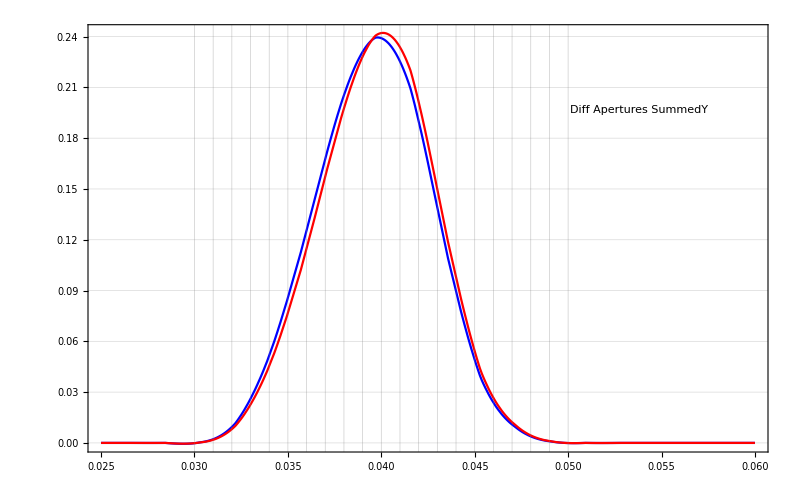

```mathematica
bins24acomparInter=Show[Plot[intersmaller2[x],{x,0.025,0.06},PlotStyle->Blue],Plot[intersmaller2p1050[x],{x,0.025,0.06},PlotStyle->Red],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Blue},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Red},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

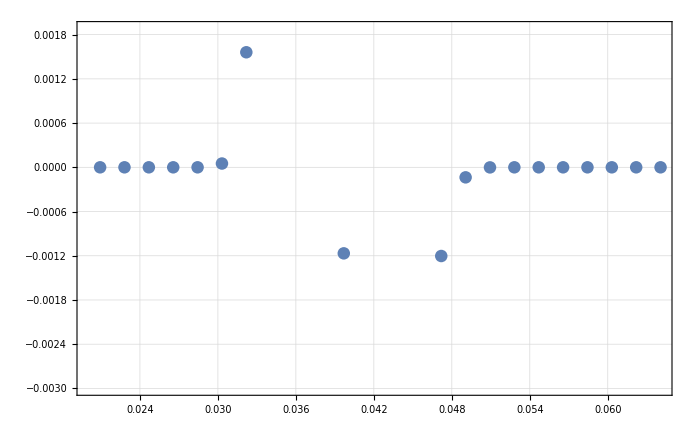

```mathematica
diffavalues24=ListPlot[Transpose[{onedsumsmaller2[[1]][[All,1]],onedsumsmaller2[[1]][[All,2]]-onedsumsmaller2p1050[[1]][[All,2]]}]]
```

```mathematica
Export["~/Desktop/Images/diffavalues24.png",diffavalues24]
```

~/Desktop/Images/diffavalues24.png

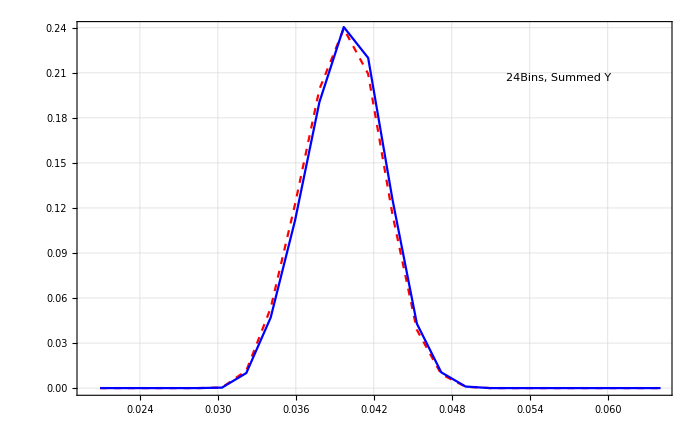

```mathematica
bins24acompar=Show[ListPlot[onedsumsmaller2[[1]],Joined->True,PlotStyle->{Red,Dashed}],ListLinePlot[onedsumsmaller2p1050[[1]],Joined->True,PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["24Bins, Summed Y",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.85}]]]
```

```mathematica
Export["~/Desktop/Images/bins24acompar.png",bins24acompar];Export["~/Desktop/Images/bins24acomparInter.png",bins24acomparInter]
```

~/Desktop/Images/bins24acomparInter.png

```mathematica
|
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

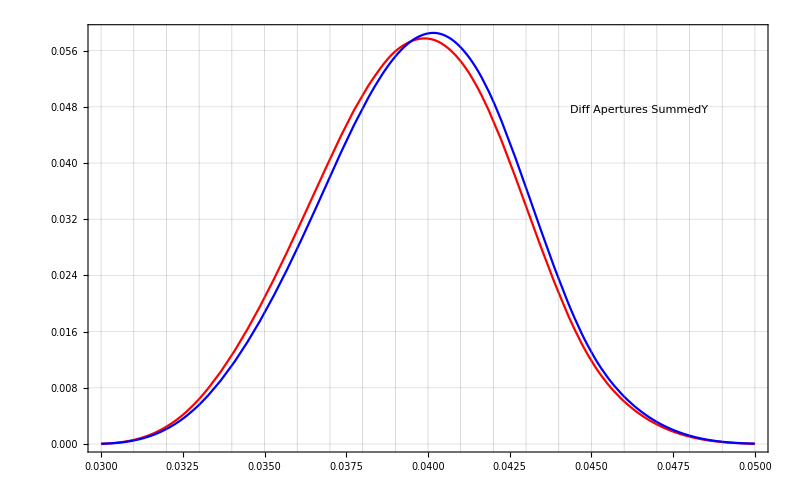

```mathematica
bins44acomparInter=Show[Plot[intersmaller44[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller44p1050[x],{x,0.03,0.05},PlotStyle->Blue],ImageSize->800,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

```mathematica
Export["~/Desktop/Images/bins44acomparInter.png",bins44acomparInter]
```

~/Desktop/Images/bins44acomparInter.png

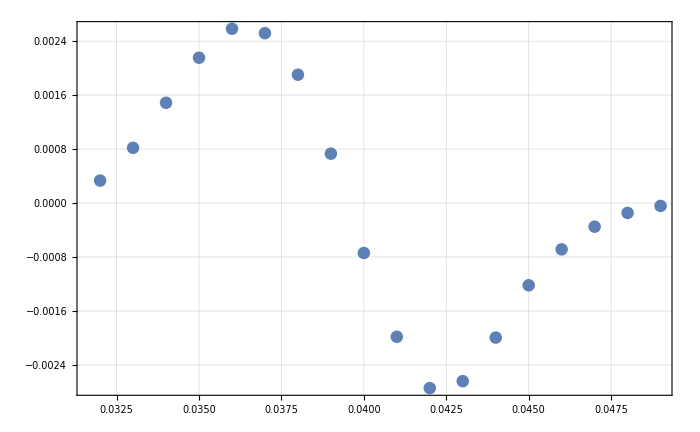

```mathematica
interdiffbwavalues44bins=ListPlot[Table[{x,intersmaller44[x]-intersmaller44p1050[x]},{x,0.032,0.049,0.001}]]
```

```mathematica
Export["~/Desktop/Images/interdiffbwavalues44bins.png",interdiffbwavalues44bins]
```

~/Desktop/Images/interdiffbwavalues44bins.png

```mathematica
?rG
```

```mathematica
rG[pmax,Pi/4,0.976]
```

0.00286926

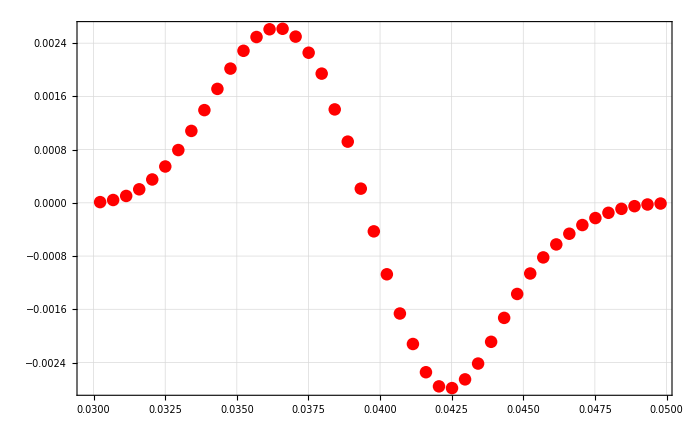

```mathematica
diffbwavalues44bins=ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]-onedsumsmaller44p1050[[1]][[All,2]]}],PlotStyle->{Red,Dashed}]
```

```mathematica
Export["~/Desktop/Images/diffbwavalues44bins.png",diffbwavalues44bins]
```

~/Desktop/Images/diffbwavalues44bins.png

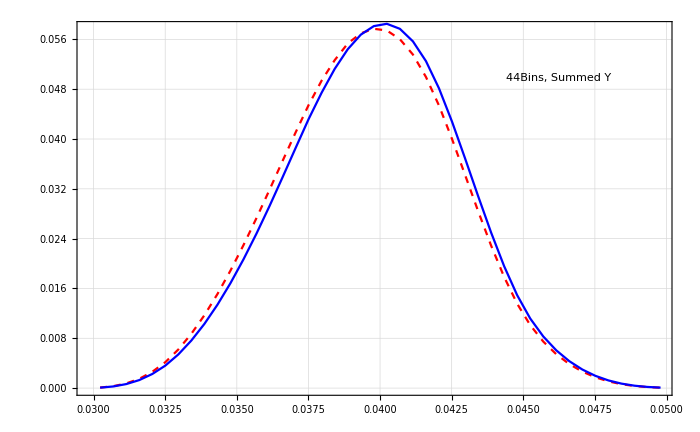

```mathematica
bins44acompar=Show[ListPlot[onedsumsmaller44[[1]],Joined->True,PlotStyle->{Red,Dashed}],ListLinePlot[onedsumsmaller44p1050[[1]],Joined->True,PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["44Bins, Summed Y",Bold,16],LineLegend[{Red},{"-0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Blue},{"0.105"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.85}]]]
```

```mathematica
Max[onedsumsmaller44[[1]][[All,2]]]
```

0.0577003

```mathematica
24/132.
```

0.181818

```mathematica
264/44
```

6

```mathematica
44/132.
```

0.333333

```mathematica
6/132.
```

0.0454545

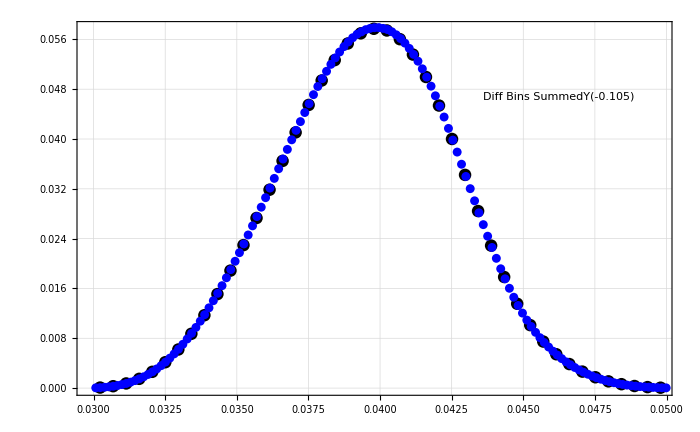

```mathematica
Show[ListPlot[onedsumsmaller44[[1]],PlotStyle->Black],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]/0.333}],PlotStyle->Blue],
Epilog->Inset[
Framed[Column[
{Style["Diff Bins SummedY(-0.105)",Bold,16],PointLegend[{Red},{"24Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Black},{"44Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Blue},{"132Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

```mathematica
onedsumsmaller132[[1]]
```

```mathematica
24/44.
```

0.545455

```mathematica
0.55
```

```mathematica
11/6.
```

1.83333

```mathematica
1.8333/0.5454545454545454
```

3.36105

```mathematica
264/44
```

6

```mathematica
24+11
```

35

```mathematica
50*35.
```

1750.

```mathematica
6+44
```

50

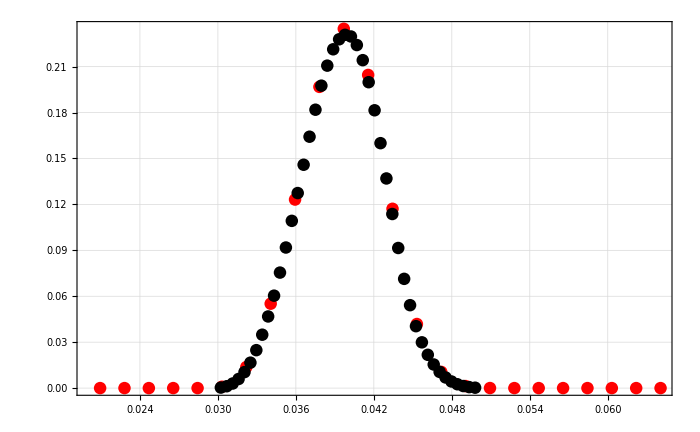

```mathematica
compar24and44=Show[ListPlot[onedsumsmaller[[1]],PlotStyle->Red],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]/0.25}],PlotStyle->Black]]
```

```mathematica
Export["~/Desktop/Images/compar24and44.png",compar24and44]
```

~/Desktop/Images/compar24and44.png

```mathematica
0.18181818181818182+0.25
```

0.431818

```mathematica
44*.25
```

11.

```mathematica
11/132.
```

0.0833333

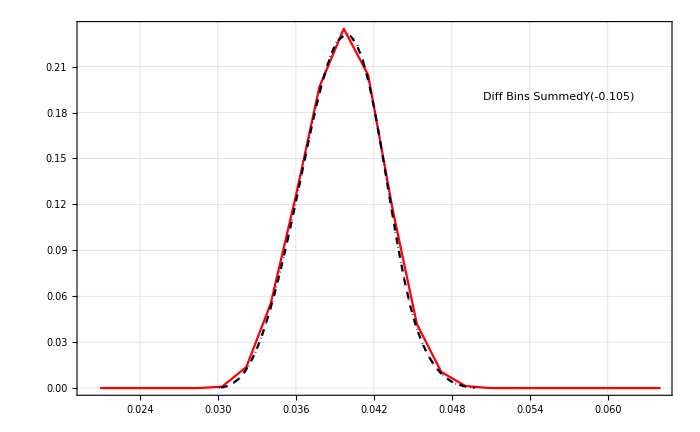

```mathematica
binCompar2=Show[ListPlot[onedsumsmaller[[1]],PlotStyle->Red,Joined->True],ListPlot[Transpose[{onedsumsmaller44[[1]][[All,1]],onedsumsmaller44[[1]][[All,2]]/0.25}],PlotStyle->{Black,Dashed},Joined->True],ListPlot[Transpose[{onedsumsmaller132[[1]][[All,1]],onedsumsmaller132[[1]][[All,2]]/0.08333}],PlotStyle->{Blue,Dotted},Joined->True],
Epilog->Inset[
Framed[Column[
{Style["Diff Bins SummedY(-0.105)",Bold,16],PointLegend[{Red},{"24Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Black},{"44Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{Blue},{"132Bins"},LegendMarkers->{●,12.96},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

```mathematica
Export["~/Desktop/Images/binComparison2.png",binCompar2]
```

~/Desktop/Images/binComparison2.png

```mathematica
Export["~/Desktop/Images/binComparison.png",binCompar];Export["~/Desktop/Images/aComparison.png",bins44acompar]
```

~/Desktop/Images/aComparison.png

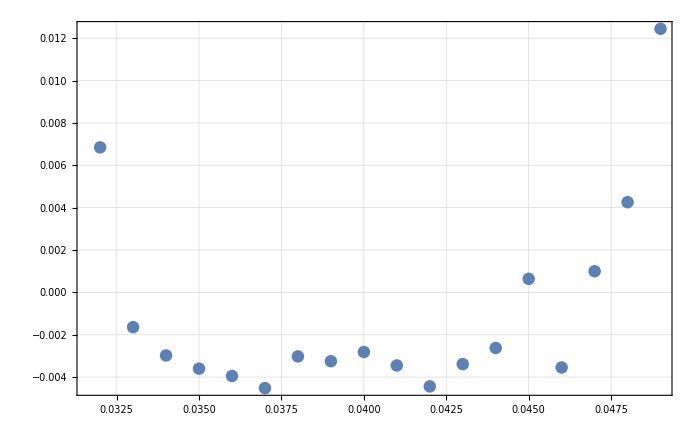

0.00286926

```mathematica
diff132and44=ListPlot[Table[{x,(intersmaller44[x]-intersmaller132[x]/0.333)/intersmaller44[x]},{x,0.032,0.049,0.001}]]
```

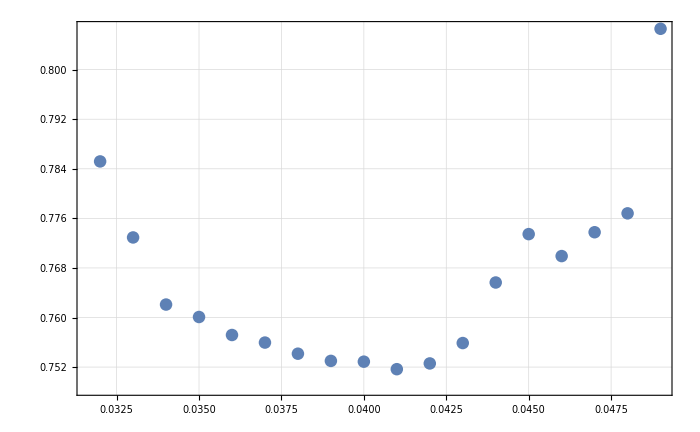

```mathematica
diff132and24=ListPlot[Table[{x,(intersmaller[x]-intersmaller132[x]/0.333)/intersmaller[x]},{x,0.032,0.049,0.001}]]
```

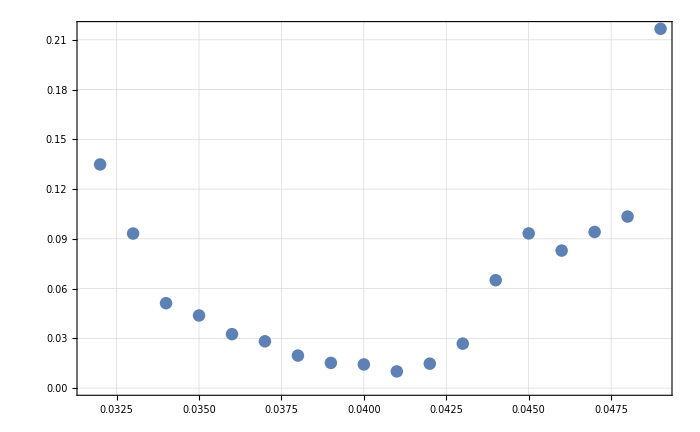

```mathematica
diff44and24=ListPlot[Table[{x,(intersmaller[x]-intersmaller44[x]/0.25)/intersmaller[x]},{x,0.032,0.049,0.001}]]
```

```mathematica
Export["~/Desktop/Images/diff132and44.png",diff132and44];
```

```mathematica
Export["~/Desktop/Images/diff132and24.png",diff132and24];Export["~/Desktop/Images/diff44and24.png",diff44and24];
```

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

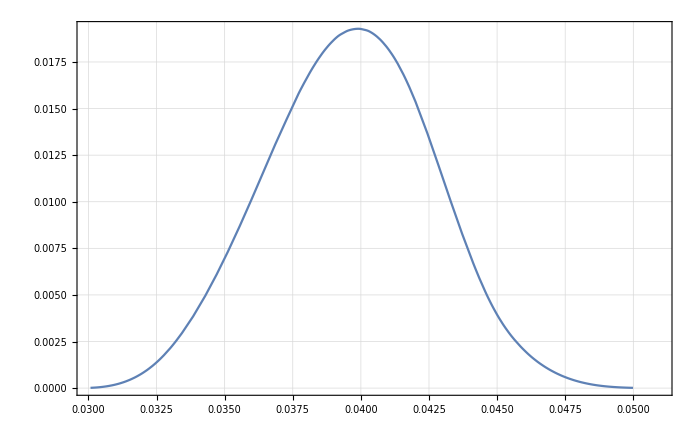

```mathematica
Plot[intersmaller132[x],{x,0.03,0.051}]
```

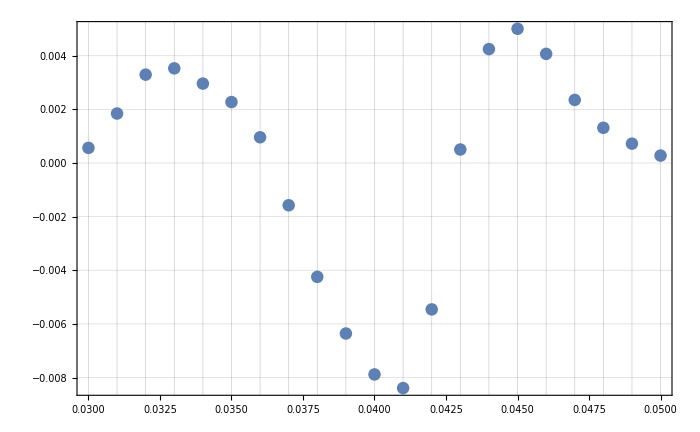

```mathematica
diffbwApts1vs3=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller3[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

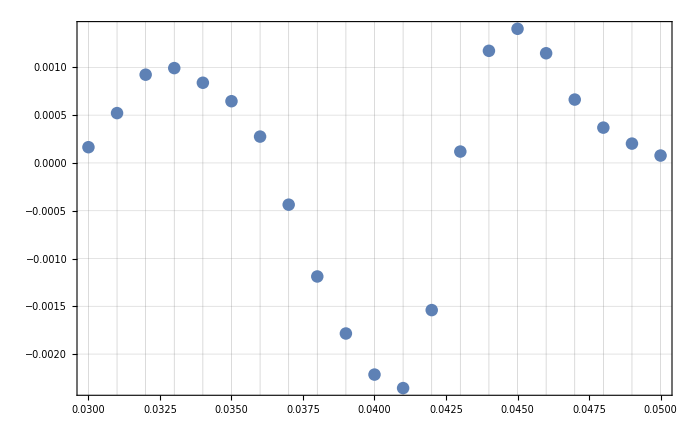

```mathematica
diffbwApts2and4=Show[ListPlot[Table[{x,intersmaller4[x]-intersmaller2[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

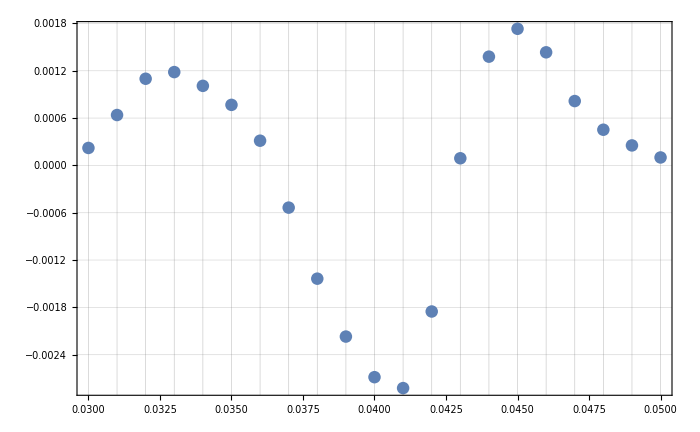

```mathematica
diffbwApts1and4=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller4[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

```mathematica
Export["~/Desktop/Images/diffbwApts1and4.png",diffbwApts1and4];Export["~/Desktop/Images/diffbwApts2and4.png",diffbwApts2and4];
```

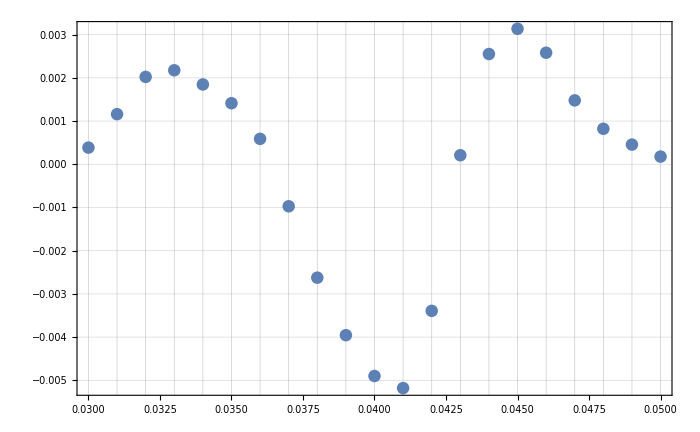

```mathematica
diffbwApts=Show[ListPlot[Table[{x,intersmaller[x]-intersmaller2[x]},{x,0.03,0.05,0.001}]],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

```mathematica
Export["~/Desktop/Images/diffbwApts.png.1c
```

```mathematica
UnitConvert[Quantity[3/1000,"Meters"],"Millimeters"]
```

3 mm

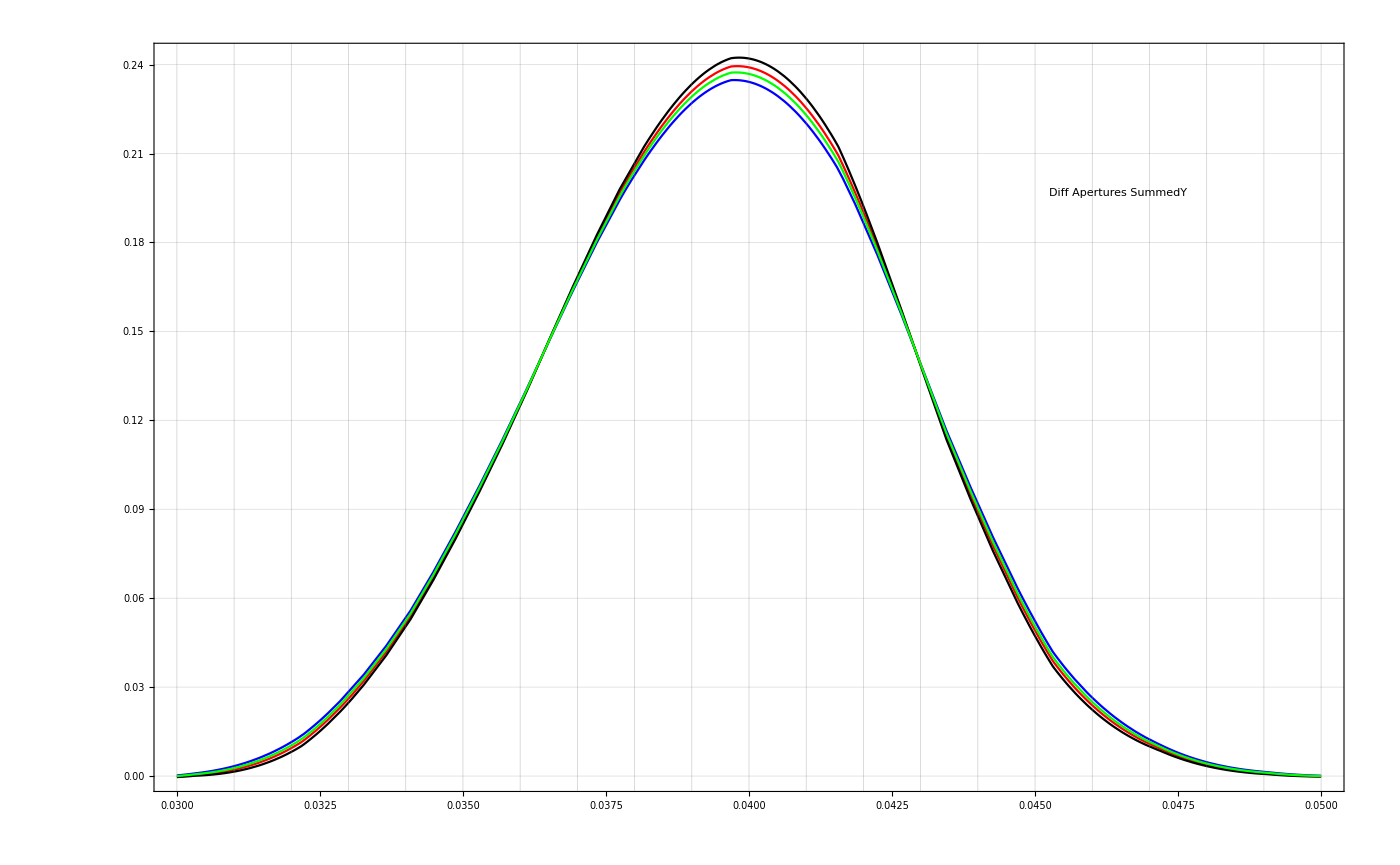

```mathematica
aptsCompar=Show[Plot[intersmaller[x],{x,0.03,0.05},PlotStyle->Blue],Plot[intersmaller2[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller3[x],{x,0.03,0.05},PlotStyle->Black],Plot[intersmaller4[x],{x,0.03,0.05},PlotStyle->Green],ImageSize->1400,PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic},
Epilog->Inset[
Framed[Column[
{Style["Diff Apertures SummedY",Bold,16],LineLegend[{Blue},{"3mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Red},{"2mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],LineLegend[{Black},{"1mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]],
LineLegend[{Black},{"2.5mm"},LabelStyle->Directive[FontSize->14,Bold],"BaseStyle"->Thickness[.1]]}],Background->White
]
,Scaled[{0.81,0.80}]]]
```

```mathematica
Export["~/Desktop/Images/diffbwApts1vs3.png",diffbwApts1vs3]
```

~/Desktop/Images/diffbwApts1vs3.png

```mathematica
Export["~/Desktop/Images/aptsCompar.png",aptsCompar];Export["~/Desktop/Images/diffbwApts.png",diffbwApts]
```

~/Desktop/Images/diffbwApts.png

```mathematica
0.019280963113476567
```

```mathematica
Max[Table[intersmaller44[x],{x,0.03,0.05,0.0001}]]
```

InterpolatingFunction::dmval: Input value {0.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0301} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0302} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.0577311

InterpolatingFunction::dmval: Input value {0.0300004} lies outside the range of data in the interpolating function. Extrapolation will be used.

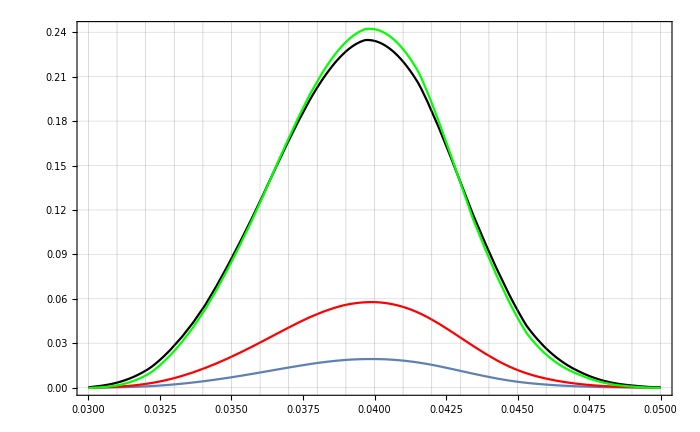

```mathematica
Show[Plot[intersmaller132[x],{x,0.03,0.05}],Plot[intersmaller44[x],{x,0.03,0.05},PlotStyle->Red],Plot[intersmaller[x],{x,0.03,0.05},PlotStyle->Black],Plot[intersmaller3[x],{x,0.03,0.05},PlotStyle->Green],PlotRange->All,GridLines->{Table[i,{i,0.03,0.05,0.001}],Automatic}]
```

```mathematica
Show[Plot[intersmaller[x],{x,0.027,0.051}]
```

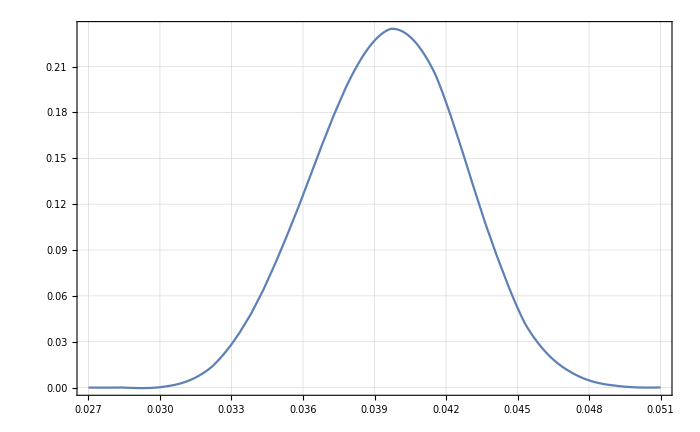

```mathematica
Plot[intersmaller[x],{x,0.027,0.051}]
```

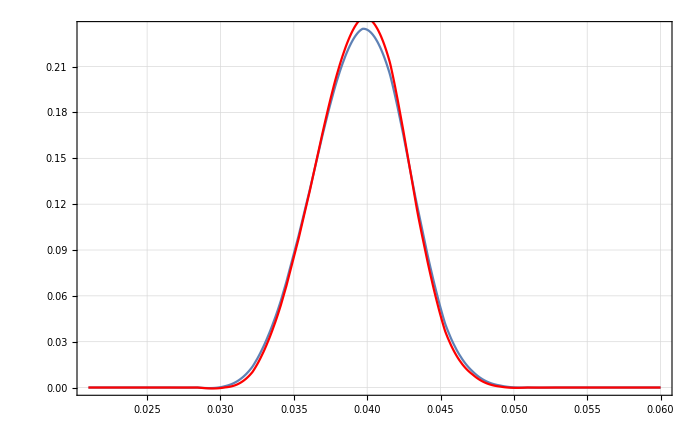

```mathematica
Show[Plot[intersmaller[x],{x,0.021,0.06}],Plot[intersmaller3[x],{x,0.021,0.06},PlotStyle->Red]]
```

```mathematica
FactorInteger[264]
```

{{2,3},{3,1},{11,1}}

```mathematica
264/44
```

6

```mathematica
42*11
```

462

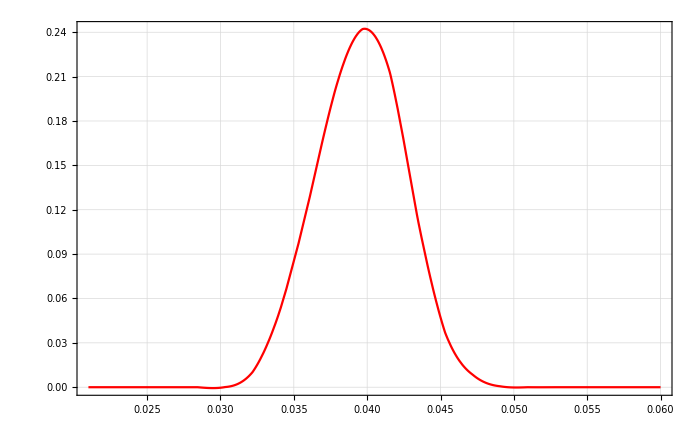

```mathematica
Plot[intersmaller3[x],{x,0.021,0.06},PlotStyle->Red]
```

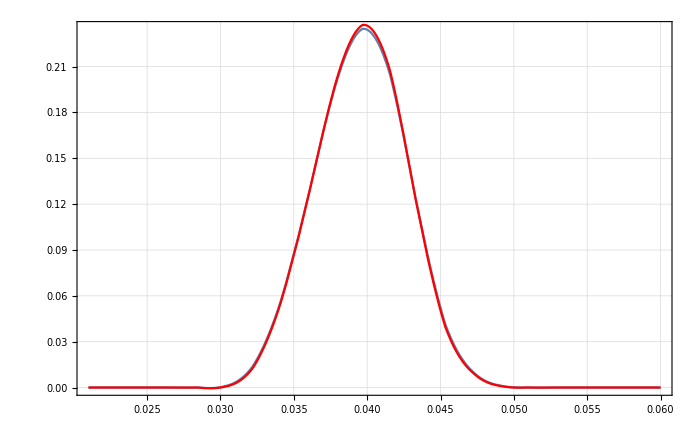

```mathematica
Show[Plot[intersmaller[x],{x,0.021,0.06}],Plot[intersmaller4[x],{x,0.021,0.06},PlotStyle->Red]]
```

```mathematica
Show[Plot[Intert5[x]-Intert6[x],{x,0.021,0.06}]]
```

-Graphics-

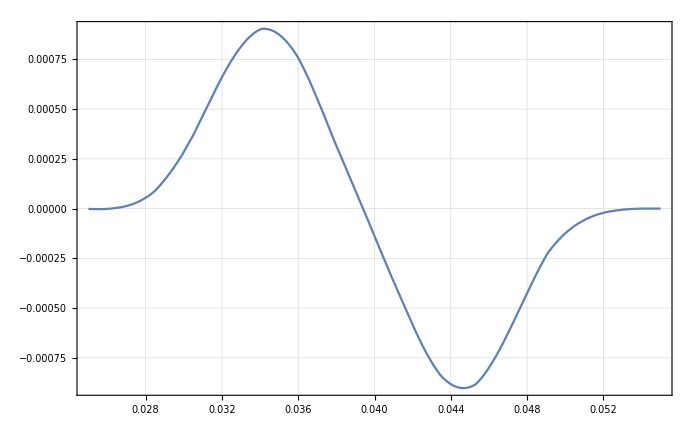

```mathematica
Show[Plot[d0SpectrumInter[x,0]-d1050PSpectrumInter[x,0],{x,0.025,0.055}]]
```

```mathematica
d0SpectrumInterSmaller=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0smaller[[All,2]]/Total[d0Spectruma0smaller[[All,2]]]}]];
```

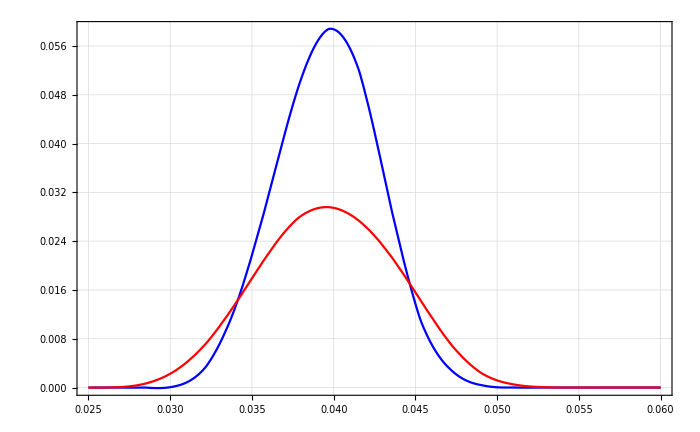

```mathematica
Show[Plot[d0SpectrumInterSmaller[x,0.01],{x,0.025,0.06},PlotStyle->Blue],Plot[d0SpectrumInter[x,0.01],{x,0.025,0.06},PlotStyle->Red]]
```

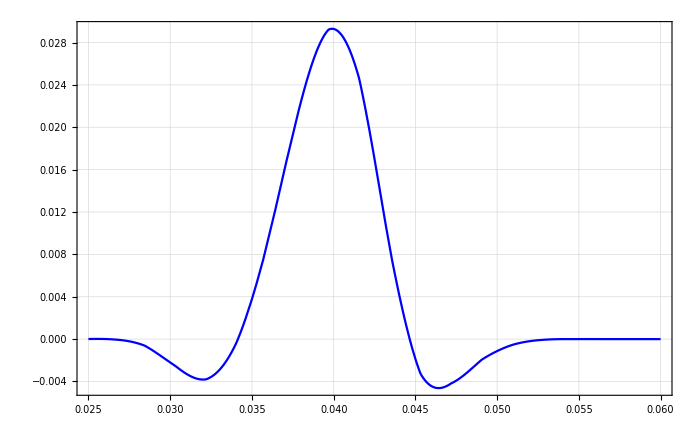

```mathematica
Show[Plot[d0SpectrumInterSmaller[x,0.01]-d0SpectrumInter[x,0.01],{x,0.025,0.06},PlotStyle->Blue]]
```

# Diff Ratios2

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_da02/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_da02_a-1050_179-264.txt}

```mathematica
d0Spectruma0=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]/Total[d0Spectruma0[[All,2]]]}]];
```

## drD Normal, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];Length[drDSubFileNamesa0]
```

8

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""];Length[drDSubFileNamesa1040]
```

8

```mathematica
drDSpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""];Length[drDSubFileNamesa1045]
```

8

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""];Length[drDSubFileNamesa1055]
```

8

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

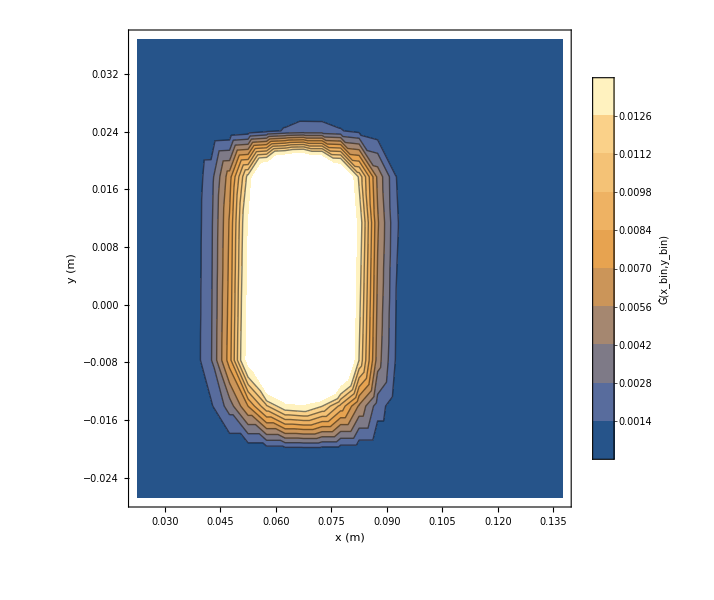

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

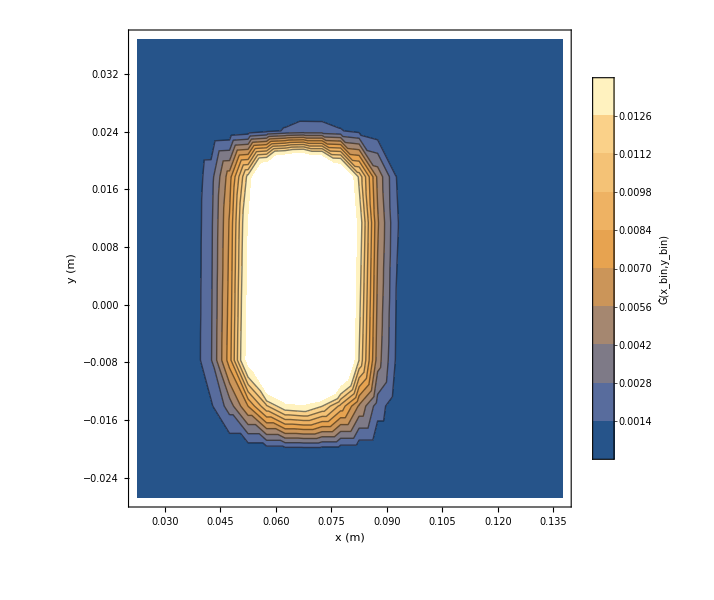

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drD2/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""];Length[drDSubFileNamesa1060]
```

8

#### in future, just do map so total length of list is not necessary

```mathematica
drDSpectruma1060=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drDSpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]]}]];
```

```mathematica
drDSpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]]}]];
drDSpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]]}]];
drDSpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]]}]];
drDSpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]}]];
```

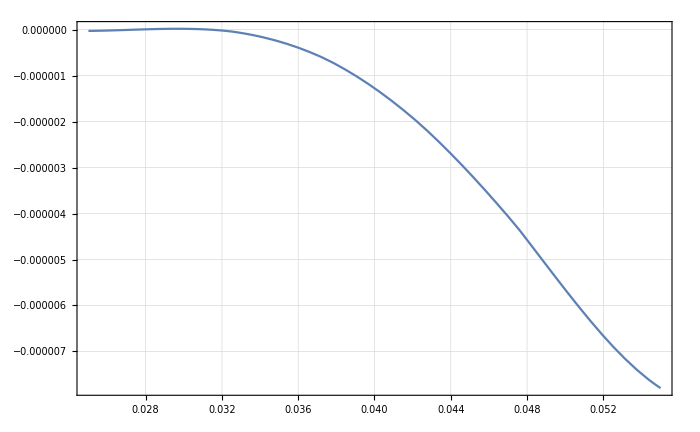

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

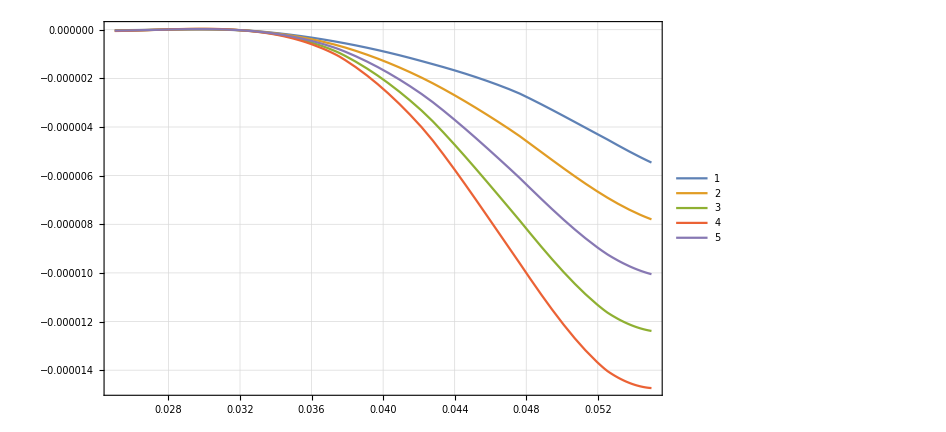

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drDSpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drDSpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rDDataList={drDSpectruma1040[[All,2]]/Total[drDSpectruma1040[[All,2]]],drDSpectruma1045[[All,2]]/Total[drDSpectruma1045[[All,2]]],drDSpectruma0[[All,2]]/Total[drDSpectruma0[[All,2]]],drDSpectruma1055[[All,2]]/Total[drDSpectruma1055[[All,2]]],drDSpectruma1060[[All,2]]/Total[drDSpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

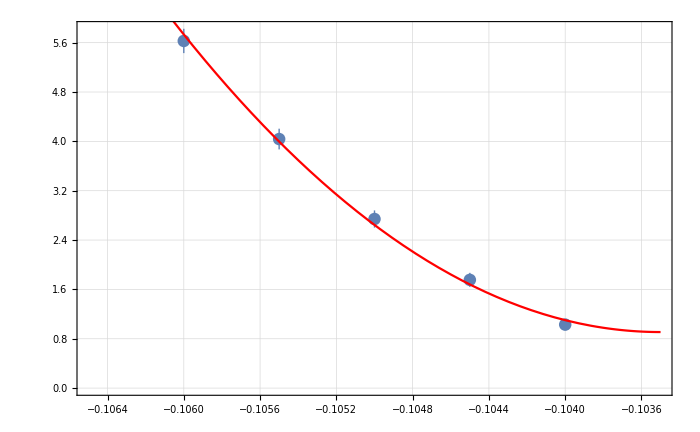
{{{1.0293×10^-9,1.75444×10^-9,2.74106×10^-9,4.0374×10^-9,5.62773×10^-9},{9.00245×10^-11,1.13785×10^-10,1.39475×10^-10,1.67778×10^-10,1.9721×10^-10}},a0 =  | -0.1035
FittedModel[9.08555×10^-10+0.000772066 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000266218 | -388.78 | 6.61589×10^-6
scale | 0.000772066 | 0.000147233 | 5.24385 | 0.0344956
yoffset | 9.08555×10^-10 | 2.3229×10^-10 | 3.9113 | 0.0595844 | 
 | DF | SS | MS
Model | 3 | 2146.23 | 715.409
Error | 2 | 1.88653 | 0.943267
Uncorrected Total | 5 | 2148.11 | 
Corrected Total | 4 | 621.509 |  | ,-Graphics-}

```mathematica
rDInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rDDataList,bList, 4]
```

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0[[All,2]],rDDataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.0293×10^-9,1.75444×10^-9,2.74106×10^-9,4.0374×10^-9,5.62773×10^-9},{9.00245×10^-11,1.13785×10^-10,1.39475×10^-10,1.67778×10^-10,1.9721×10^-10}},a0 =  | -0.103083
FittedModel[5.31764×10^-10+0.000598908 (0.103083+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103083 | 0.000443949 | -232.196 | 0.0000185472
scale | 0.000598908 | 0.000147233 | 4.06777 | 0.0554555
yoffset | 5.31764×10^-10 | 4.22114×10^-10 | 1.25976 | 0.334845 | 
 | DF | SS | MS
Model | 3 | 2148.07 | 716.023
Error | 2 | 0.0426508 | 0.0213254
Uncorrected Total | 5 | 2148.11 | 
Corrected Total | 4 | 621.509 |  | ,-Graphics-}

```mathematica
((rDInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-142.824

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

-182.552

# Diff Ratios drA k=138.9

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]/Total[d0Spectruma0[[All,2]]]}]];
```

## drA Normal, k=95.24

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1040/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_1-49.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_50-98.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_99-106.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_107-122.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_123-138.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_139-154.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_155-178.txt,TransferResult_08-09-20_SC_diffRatio_G_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_1-49.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_50-98.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_99-106.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_107-122.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_123-138.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_139-154.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_155-178.txt,TransferResult_08-09-20_SC_diffRatio_H_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffRatio_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_50-98.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_SC_diffRatio_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.94452×10^-9,2.72923×10^-9,1.77068×10^-9,1.07905×10^-9,6.49406×10^-10},{1.41684×10^-10,1.15784×10^-10,9.04344×10^-11,6.63659×10^-11,4.5621×10^-11}},a0 =  | -0.106459
FittedModel[5.52455×10^-10+0.000558718 (0.106459+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106459 | 0.000216386 | -491.986 | 4.13135×10^-6
scale | 0.000558718 | 0.0000928505 | 6.0174 | 0.0265236
yoffset | 5.52455×10^-10 | 1.21719×10^-10 | 4.53878 | 0.0452716 | 
 | DF | SS | MS
Model | 3 | 2180.62 | 726.872
Error | 2 | 0.44086 | 0.22043
Uncorrected Total | 5 | 2181.06 | 
Corrected Total | 4 | 737.61 |  | ,-Graphics-}

```mathematica
rAInvest2=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.94452×10^-9,2.72923×10^-9,1.77068×10^-9,1.07905×10^-9,6.49406×10^-10},{1.41684×10^-10,1.15784×10^-10,9.04344×10^-11,6.63659×10^-11,4.5621×10^-11}},a0 =  | -0.106562
FittedModel[4.80273×10^-10+0.000528361 (0.106562+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106562 | 0.000246528 | -432.252 | 5.35209×10^-6
scale | 0.000528361 | 0.0000928505 | 5.69045 | 0.0295214
yoffset | 4.80273×10^-10 | 1.46344×10^-10 | 3.28181 | 0.0816394 | 
 | DF | SS | MS
Model | 3 | 2181.05 | 727.017
Error | 2 | 0.00581495 | 0.00290748
Uncorrected Total | 5 | 2181.06 | 
Corrected Total | 4 | 737.61 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

138.926

```mathematica
((rAInvest2[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

148.758

# Normal

## da0 Normal

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_da0/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_da0_a-1050_1-49.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_50-98.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_99-106.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_107-122.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_123-138.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_139-154.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_155-178.txt,TransferResult_08-09-20_NC_opt_G_da0_a-1050_179-264.txt}

```mathematica
d0Spectruma0Normal=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=0.02;
xEnd=0.14;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0Normal[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],d0Spectruma0[[All,2]]/Total[d0Spectruma0[[All,2]]]}]];
```

## drD Normal, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1050/"];
```

```mathematica
drDSubFileNamesa0=FileSorter[""];
```

```mathematica
drDSpectruma0=Flatten[Table[Import[drDSubFileNamesa0[[i]],"Table"],{i,1,Length[drDSubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1040/"];
```

```mathematica
drDSubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drD_a-1040_1-49.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_50-98.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_99-106.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_107-122.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_123-138.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_139-154.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_155-178.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1045/"];
```

```mathematica
drDSubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drD_a-1045_1-49.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_50-98.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_99-106.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_107-122.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_123-138.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_139-154.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_155-178.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1045_179-264.txt}

```mathematica
drDSpectruma1045=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1055/"];
```

```mathematica
drDSubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drD_a-1055_1-49.txt,TransferResult_08-09-20_NC_opt_H_drD_a-1055_50-98.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_99-106.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_107-122.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_123-138.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_139-154.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_155-178.txt,TransferResult_08-09-20_NC_opt_C_drD_a-1055_179-264.txt}

```mathematica
drDSpectruma1055=Flatten[Import[#,"Table"]&/@drDSubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
drDSpectruma1055//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drDSpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drD/a-1060/"];
```

```mathematica
drDSubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drD_a-1060_1-49.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1060_50-98.txt,TransferResult_08-09-20_NC_opt_G_drD_a-1060_99-106.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.35521×10^-9,1.33752×10^-9,7.8325×10^-10,6.60844×10^-10,9.60287×10^-10},{9.12699×10^-11,6.60112×10^-11,4.79813×10^-11,4.40051×10^-11,5.6678×10^-11}},a0 =  | -0.105396
FittedModel[6.4678×10^-10+0.000871254 (0.105396+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105396 | 0.0000339757 | -3102.12 | 1.03916×10^-7
scale | 0.000871254 | 0.000066918 | 13.0197 | 0.00584755
yoffset | 6.4678×10^-10 | 3.14428×10^-11 | 20.5701 | 0.00235501 | 
 | DF | SS | MS
Model | 3 | 1855.45 | 618.484
Error | 2 | 0.0472826 | 0.0236413
Uncorrected Total | 5 | 1855.5 | 
Corrected Total | 4 | 325.846 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

37.7579

```mathematica
0.000106*10^3
```

0.106

```mathematica
0.000161*37.76
```

0.00607936

```mathematica
0.000106*157.04
```

0.0166462

## drA Normal, k=95.24

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1050/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1050_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1050_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1050_179-264.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1040/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_drA_a-1040_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_50-98.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_99-106.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_107-122.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_123-138.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_139-154.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_155-178.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1040_179-264.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1045/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1045_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1045_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1045_179-264.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1055/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1055_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1055_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1055_179-264.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

```mathematica
ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[d0Spectruma0[[All,2]]]}],BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

-Graphics-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/NC_Prot_opt_drA/a-1060/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_drA_a-1060_1-49.txt,TransferResult_08-09-20_NC_opt_G_drA_a-1060_50-98.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_99-106.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_107-122.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_123-138.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_139-154.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_155-178.txt,TransferResult_08-09-20_NC_opt_C_drA_a-1060_179-264.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
XYBinCentersYHalf[[All,2]]//Length
```

264

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{

d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.]}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Plot[{
d0SpectrumInter[x,0.]-drASpectruma1040Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1045Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1055Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma1060Inter[x,0.],
d0SpectrumInter[x,0.]-drASpectruma0Inter[x,0.]
}
,{x,0.025,0.055},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-.105,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.35521×10^-9,1.33752×10^-9,7.8325×10^-10,6.60844×10^-10,9.60287×10^-10},{9.12699×10^-11,6.60112×10^-11,4.79813×10^-11,4.40051×10^-11,5.6678×10^-11}},a0 =  | -0.105396
FittedModel[6.4678×10^-10+0.000871254 (0.105396+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105396 | 0.0000339757 | -3102.12 | 1.03916×10^-7
scale | 0.000871254 | 0.000066918 | 13.0197 | 0.00584755
yoffset | 6.4678×10^-10 | 3.14428×10^-11 | 20.5701 | 0.00235501 | 
 | DF | SS | MS
Model | 3 | 1855.45 | 618.484
Error | 2 | 0.0472826 | 0.0236413
Uncorrected Total | 5 | 1855.5 | 
Corrected Total | 4 | 325.846 |  | ,-Graphics-}

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(10^-4)
```

37.7579

```mathematica
0.000106*10^3
```

0.106

```mathematica
0.000161*37.76
```

0.00607936

```mathematica
0.000106*157.04
```

0.0166462

# Testing

```mathematica
bin2DGenOld[xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY},binLengthX=Round[(xEnd-xStart)/binNoX,1/10^6.];binLengthY=Round[(yEnd-yStart)/binNoY,1/10^6.];binsX=Table[{xStart+(i-1) binLengthX,xStart+i binLengthX},{i,binNoX}];binsY=Table[{yStart+(i-1) binLengthY,yStart+i binLengthY},{i,binNoY}];binList=Flatten[Table[{binsX⟦i⟧,binsY⟦j⟧},{i,Length[binsX]},{j,Length[binsY]}],1];Return[binList];]
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/TransferResult_08-09-20_SC_opt_D_da0_a-1050_179-264.txt}

```mathematica
RefSpectrumNew=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
SubFileNames0=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_1-49.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_50-98.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_99-106.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_107-122.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_123-138.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_139-154.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_155-178.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_opt_da0/a-1050/Cluster/TransferResult_08-09-20_SC_opt_C_da0_a-1050_179-264.txt}

```mathematica
RefSpectrumOld=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,Length[SubFileNames0]}],1];
```

```mathematica
ListPlot[-RefSpectrumNew[[All,2]]]
```

-Graphics-

```mathematica
ListPlot[RefSpectrumOld[[All,2]]]
```

-Graphics-

```mathematica
d0SpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBinsOld=bin2DGenOld[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
xStart=0.02;
xEnd=0.065;
yStart=-0.03;
yEnd=0.04;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,24,11];
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(xyBins[[i,1,1]]+xyBins[[i,1,2]])/2,(xyBins[[i,2,1]]+xyBins[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
XYBinCentersYHalfOld=BinCenters[xyBinsOld];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalfOld[[All,1]],XYBinCentersYHalfOld[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

```mathematica
old=Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}];
```

```mathematica
new=Transpose[{XYBinCentersYHalfOld[[All,1]],XYBinCentersYHalfOld[[All,2]],RefSpectrumOld[[All,2]]/Total[RefSpectrumOld[[All,2]]]}];
```

```mathematica
Transfer3DPlot2=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrumNew[[All,2]]/Total[RefSpectrumNew[[All,2]]]}],BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

```mathematica
|
```

```mathematica
rFSC=2.036;
rASC=0.937;
rRxBSC=0.902;
bRxBSC=0.976;
g1SC=1.29;
g2SC=1.792;
alphaSC=180.03*Pi/180;
rDSC=0.88;
xAShiftSC=0;
yAShiftSC=2.873/1000;
yRxBShiftSC=1.518/1000;
xDShiftSC=0;
yDShiftSC=6.234/1000;
xAASC=3/1000;
yAASC=25/1000;
xAOffSC=30/1000;
yAOffSC=0;
wnxSC=10/100;
wnySC=6/100;
pnxSC=9/100;
pnySC=5/100;
kx1SC=0.9;
ky1SC=0.9;
kx2SC=0;
ky2SC=0;
kx3SC=-0.9;
ky3SC=-0.9;

xStart=0.03;
xEnd=0.05;
yStart=-0.022;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];

IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};

Print["Run started at ",DateString[],", Bins: ",Bins];
```

Run started at Thu 31 Mar 2022 11:39:06, Bins: {1,5}

$Aborted

```mathematica
Table[i,{i,1,64,8}]
```

{1,9,17,25,33,41,49,57}

```mathematica
64/8
```

8

```mathematica
x
```

```mathematica
xyBins[[50.;;98.]]
```

Part::take: Cannot take positions 50 through 98 in {{{0.03,0.030313},{0.025,-0.022}},{{0.030313,0.030626},{0.025,-0.022}},{{0.030626,0.030939},{0.025,-0.022}},{{0.030939,0.031252},{0.025,-0.022}},{{0.031252,0.031565},{0.025,-0.022}},{{0.031565,0.031878},{0.025,-0.022}},{{0.031878,0.032191},{0.025,-0.022}},{{0.032191,0.032504},{0.025,-0.022}},«35»,{{0.043459,0.043772},{0.025,-0.022}},{{0.043772,0.044085},{0.025,-0.022}},{{0.044085,0.044398},{0.025,-0.022}},{{0.044398,0.044711},{0.025,-0.022}},{{0.044711,0.045024},{0.025,-0.022}},{{0.045024,0.045337},{0.025,-0.022}},{{0.045337,0.04565},{0.025,-0.022}},«14»}.

{{{0.03,0.030313},{0.025,-0.022}},{{0.030313,0.030626},{0.025,-0.022}},{{0.030626,0.030939},{0.025,-0.022}},{{0.030939,0.031252},{0.025,-0.022}},{{0.031252,0.031565},{0.025,-0.022}},{{0.031565,0.031878},{0.025,-0.022}},{{0.031878,0.032191},{0.025,-0.022}},{{0.032191,0.032504},{0.025,-0.022}},{{0.032504,0.032817},{0.025,-0.022}},{{0.032817,0.03313},{0.025,-0.022}},{{0.03313,0.033443},{0.025,-0.022}},{{0.033443,0.033756},{0.025,-0.022}},{{0.033756,0.034069},{0.025,-0.022}},{{0.034069,0.034382},{0.025,-0.022}},{{0.034382,0.034695},{0.025,-0.022}},{{0.034695,0.035008},{0.025,-0.022}},{{0.035008,0.035321},{0.025,-0.022}},{{0.035321,0.035634},{0.025,-0.022}},{{0.035634,0.035947},{0.025,-0.022}},{{0.035947,0.03626},{0.025,-0.022}},{{0.03626,0.036573},{0.025,-0.022}},{{0.036573,0.036886},{0.025,-0.022}},{{0.036886,0.037199},{0.025,-0.022}},{{0.037199,0.037512},{0.025,-0.022}},{{0.037512,0.037825},{0.025,-0.022}},{{0.037825,0.038138},{0.025,-0.022}},{{0.038138,0.038451},{0.025,-0.022}},{{0.038451,0.038764},{0.025,-0.022}},{{0.038764,0.039077},{0.025,-0.022}},{{0.039077,0.03939},{0.025,-0.022}},{{0.03939,0.039703},{0.025,-0.022}},{{0.039703,0.040016},{0.025,-0.022}},{{0.040016,0.040329},{0.025,-0.022}},{{0.040329,0.040642},{0.025,-0.022}},{{0.040642,0.040955},{0.025,-0.022}},{{0.040955,0.041268},{0.025,-0.022}},{{0.041268,0.041581},{0.025,-0.022}},{{0.041581,0.041894},{0.025,-0.022}},{{0.041894,0.042207},{0.025,-0.022}},{{0.042207,0.04252},{0.025,-0.022}},{{0.04252,0.042833},{0.025,-0.022}},{{0.042833,0.043146},{0.025,-0.022}},{{0.043146,0.043459},{0.025,-0.022}},{{0.043459,0.043772},{0.025,-0.022}},{{0.043772,0.044085},{0.025,-0.022}},{{0.044085,0.044398},{0.025,-0.022}},{{0.044398,0.044711},{0.025,-0.022}},{{0.044711,0.045024},{0.025,-0.022}},{{0.045024,0.045337},{0.025,-0.022}},{{0.045337,0.04565},{0.025,-0.022}},{{0.04565,0.045963},{0.025,-0.022}},{{0.045963,0.046276},{0.025,-0.022}},{{0.046276,0.046589},{0.025,-0.022}},{{0.046589,0.046902},{0.025,-0.022}},{{0.046902,0.047215},{0.025,-0.022}},{{0.047215,0.047528},{0.025,-0.022}},{{0.047528,0.047841},{0.025,-0.022}},{{0.047841,0.048154},{0.025,-0.022}},{{0.048154,0.048467},{0.025,-0.022}},{{0.048467,0.04878},{0.025,-0.022}},{{0.04878,0.049093},{0.025,-0.022}},{{0.049093,0.049406},{0.025,-0.022}},{{0.049406,0.049719},{0.025,-0.022}},{{0.049719,0.050032},{0.025,-0.022}}}⟦50.;;98.⟧

```mathematica
BinwYShiftPrec44OriginalBinsb0NewBGrad=ParallelMap[AbsoluteTiming[BinIntShift[a,#,{alphaSC,bRxBSC,rFSC,rRxBSC,rASC,rDSC,g1SC,g2SC},{xAShiftSC,yAShiftSC,yRxBShiftSC,xDShiftSC,yDShiftSC},{wnxSC,pnxSC,kx1SC,kx2SC,kx3SC,wnySC,pnySC,ky1SC,ky2SC,ky3SC},{xAASC,yAASC,xAOffSC,yAOffSC},{IntMethod,4,2,0,2},{IntMethod,4,2,0,2},{IntMethod,3,6,0,1}]]&,xyBins[[50.;;98.]],Method->"FinestGrained"];
```